## myPackage

```mathematica
CloudGet[
 CloudObject[
  "https://www.wolframcloud.com/obj/firlecarl/myPackageWL.wl"]]

myFontSize=23
myFontStandard="Lucida Sans Unicode"; myStyle[myFontStandard,myFontSize,myFontStandard]

myStyle["Wolfram Mathematica Version 14.2",22,Background->Yellow]

myColors=ColorData[61]
myColorForGradient=ColorData["DarkRainbow"]

myCMYKColors[]
myBAUAColors[]
myPlotColors={3->RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],2->RGBColor[0.9450980392156862, 0.7019607843137254, 0.],1->RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],.5->RGBColor[0.9254901960784314, 0.4, 0.09019607843137255]}(*equivalent to myBAUAColors[][[{5,4,3,2}]]*)

myExportFigureList={};
myExportEquationList={};

impPath= NotebookDirectory[](*StringJoin[Riffle[StringSplit[NotebookDirectory[],"\\"][[1;;-2]],"\\",{2,-1,2}]]*)
exPath=NotebookDirectory[]~~"output\\"(*impPath~~"Ausgabe\\"*)

pathSaveVersions = 
 Directory[] ~~ "\\Desktop\\backup\\" (*path of backup*)
NotebookOpen[
 CloudObject[
  "https://www.wolframcloud.com/obj/firlecarl/myBackup.nb"]]

myPackageInputPrint[]
```

23

Lucida Sans Unicode

Wolfram Mathematica Version 14.2

ColorDataFunction[…]

ColorDataFunction[…]

{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]}

{RGBColor[0.4588235294117647, 0.7450980392156863, 0.9176470588235294],RGBColor[0.9254901960784314, 0.4, 0.09019607843137255],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.9450980392156862, 0.7019607843137254, 0.],RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.8117647058823529, 0.8980392156862745, 0.9725490196078431],RGBColor[0.06666666666666667, 0.3058823529411765, 0.5058823529411764]}

{3→RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],2→RGBColor[0.9450980392156862, 0.7019607843137254, 0.],1→RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],0.5→RGBColor[0.9254901960784314, 0.4, 0.09019607843137255]}

C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\

C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\output\

C:\Users\mona_\Desktop\backup\

myAroundString[l_List/;Dimensions[l]⟦2⟧==2]:=Module[{},(StringJoin[ToString[#1⟦1⟧]~~ ± ~~ToString[#1⟦-1⟧]]&)/@l]
myBAUAColors[a_Integer:5]:=Module[{bauaMainColors,bauaHighlightColors,bauaBlueColors,bauaAllColors,bauaDesignColors,bauaCMYKColors},{bauaMainColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F]},bauaHighlightColors→{RGBColor[#EC6617],RGBColor[#75BEEA],RGBColor[#ABD18F],RGBColor[#F1B300]},bauaBlueColors→{{RGBColor[#114e81],RGBColor[#015c93],RGBColor[#1770b8],RGBColor[#74bdea],RGBColor[#a6d1f1],RGBColor[#cfe5f8]}},bauaAllColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F],RGBColor[#75BEEA],RGBColor[#EC6617],RGBColor[#F1B300],RGBColor[#ABD18F],RGBColor[#114e81],RGBColor[#015c93],RGBColor[#a6d1f1],RGBColor[#cfe5f8]},bauaDesignColors→{RGBColor[0.4588235294117647, 0.7450980392156863, 0.9176470588235294],RGBColor[0.9254901960784314, 0.4, 0.09019607843137255],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.9450980392156862, 0.7019607843137254, 0.],RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.8117647058823529, 0.8980392156862745, 0.9725490196078431],RGBColor[0.06666666666666667, 0.3058823529411765, 0.5058823529411764]},bauaCMYKColors→{CMYKColor[0.85, 0.5, 0, 0],CMYKColor[0.85, 0.5, 0, 0, 0.7],CMYKColor[0.85, 0.5, 0, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3],CMYKColor[0.85, 0.5, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3, 0.7],CMYKColor[0.85, 0.45, 0, 0.3, 0.5],CMYKColor[0.85, 0.45, 0, 0.3, 0.3],CMYKColor[0., 0., 0, 0.75],CMYKColor[0., 0., 0.05, 0.06],CMYKColor[0.08, 0.03, 0.12, 0.07],CMYKColor[0.62, 0.27, 0.92, 0.7],CMYKColor[0.55, 0.1, 0, 0],CMYKColor[0., 0.75, 1, 0],CMYKColor[0., 0.3, 1, 0.05],CMYKColor[0.4, 0., 0.55, 0]}}⟦a,2⟧]
myCMYKColors[a_Integer:1]:=Module[{},{{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]},{Leuchtgelb→CMYKColor[{0, 0, 1, 0}],Zitronengelb→CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],Orange→CMYKColor[{0, Rational[11, 20], 1, 0}],Hellrosa→CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],Altrosa→CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],Feuerrot→CMYKColor[{0, 1, 1, Rational[1, 5]}],Signalrot→CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],Korallenrot→CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],Leuchtrot→CMYKColor[{0, Rational[9, 10], 1, 0}],Reines Rot→CMYKColor[{0, 1, Rational[9, 10], 0}],Weinrot→CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],Pink→CMYKColor[{0, 1, 0, 0}],Lila→CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],Violett→CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],Azurblau→CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],Himmelblau→CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],Reines Blau→CMYKColor[{1, Rational[7, 10], 0, 0}],Nachtblau→CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],Pastelltürkis→CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],Minttürkis→CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],Türkis→CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}],Leuchtgrün/Gelbgrün→CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],Grün→CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],Grasgrün→CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],Maigrün→CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}],Rotbraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Kastanienbraun→CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],Schokobraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Cremeweiß→CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],Beige→CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],Silbergrau→CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}],Steingrau→CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],Tiefschwarz→CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}]},{Leuchtgelb→{CMYKColor[{0, 0, 1, 0}]},Zitronengelb→{CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}]},Orange→{CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{0, Rational[1, 2], 1, 0}],CMYKColor[{0, Rational[11, 20], 1, 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{0, Rational[13, 20], 1, 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}]},Hellrosa→{CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], Rational[1, 10]}]},Altrosa→{CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[7, 10], Rational[3, 10], Rational[1, 10]}],CMYKColor[{0, Rational[13, 20], Rational[2, 5], Rational[1, 10]}]},Feuerrot→{CMYKColor[{0, 1, 1, Rational[1, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}]},Signalrot→{CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[1, 5], 1, Rational[9, 10], Rational[1, 10]}]},Korallenrot→{CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[3, 10]}]},Leuchtrot→{CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[{0, 1, 1, 0}]},Reines Rot→{CMYKColor[{0, 1, Rational[9, 10], 0}],CMYKColor[{0, 1, Rational[7, 10], 0}]},Weinrot→{CMYKColor[{Rational[1, 5], 1, Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[2, 5], 1, Rational[3, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],CMYKColor[{Rational[3, 5], 1, Rational[4, 5], 0}]},Pink→{CMYKColor[{0, 1, 0, 0}]},Lila→{CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],CMYKColor[{Rational[3, 5], Rational[7, 10], Rational[1, 20], Rational[1, 10]}]},Violett→{CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[9, 10], 1, 0, 0}]},Azurblau→{CMYKColor[{Rational[9, 10], Rational[3, 10], Rational[1, 10], Rational[2, 5]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, Rational[3, 10]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}]},Himmelblau→{CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[9, 10], Rational[1, 2], 0, 0}],CMYKColor[{1, Rational[3, 10], 0, Rational[1, 10]}],CMYKColor[{1, Rational[2, 5], 0, 0}]},Reines Blau→{CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{1, Rational[7, 10], 0, 0}],CMYKColor[{1, Rational[4, 5], 0, 0}],CMYKColor[{Rational[19, 20], Rational[3, 5], 0, Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, Rational[2, 5]}]},Nachtblau→{CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{1, 1, Rational[2, 5], Rational[2, 5]}]},Pastelltürkis→{CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], Rational[1, 5]}]},Minttürkis→{CMYKColor[{Rational[4, 5], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{Rational[7, 10], Rational[3, 20], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}]},Türkis→{CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[7, 20], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}]},Leuchtgrün/Gelbgrün→{CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{Rational[3, 5], 0, Rational[19, 20], 0}],CMYKColor[{Rational[7, 10], 0, Rational[9, 10], 0}]},Grün→{CMYKColor[{Rational[13, 20], 0, Rational[4, 5], 0}],CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],CMYKColor[{Rational[17, 20], 0, 1, 0}],CMYKColor[{Rational[17, 20], 0, 1, Rational[1, 10]}]},Grasgrün→{CMYKColor[{Rational[3, 5], 0, Rational[9, 10], Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[21, 25], 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],CMYKColor[{Rational[7, 10], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}]},Maigrün→{CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}]},Rotbraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[1, 20], 1, 1, Rational[4, 5]}]},Kastanienbraun→{CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],CMYKColor[{Rational[1, 2], 1, 1, Rational[1, 2]}],CMYKColor[{0, Rational[9, 10], 1, Rational[4, 5]}]},Schokobraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{0, Rational[3, 5], Rational[9, 10], Rational[4, 5]}],CMYKColor[{Rational[2, 5], Rational[7, 10], Rational[3, 5], Rational[4, 5]}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{Rational[3, 5], Rational[4, 5], Rational[4, 5], Rational[4, 5]}]},Cremeweiß→{CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}]},Beige→{CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}]},Silbergrau→{CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}]},Steingrau→{CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}]},Tiefschwarz→{CMYKColor[{1, Rational[2, 5], Rational[2, 5], Rational[9, 10]}],CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}],CMYKColor[{Rational[3, 10], 0, 0, 1}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], 1}]}}}⟦a⟧]
myExportEquations[l_List]:=Module[{id,eq},((id=#1⟦2⟧;eq=#1⟦1⟧;Export[exPath~~\equations\~~id~~.txt,ExportString[eq,{MathML,Expression}]];If[MemberQ[myExportEquationList⟦All,1⟧,id],myExportEquationList=ReplacePart[myExportEquationList,FirstPosition[myExportEquationList⟦All,1⟧,id]⟦1⟧→{id,eq}];,AppendTo[myExportEquationList,{id,eq}]];)&)/@l Export[exPath~~\equations\##1 equation IDs and equations.pdf,Column[(Row[Riffle[{#1⟦1⟧,#1⟦2⟧},	]]&)/@myExportEquationList]];Export[exPath~~\equations\##2 equation IDs.rtf,StringRiffle[Prepend[myExportEquationList⟦All,1⟧,exPath~~\equations\],
]];]
myExportF[l_List]:=Module[{r,g,nameID,name,icon},((g=#1⟦1⟧;nameID=#1⟦2⟧;name=#1⟦3⟧;If[#1⟦5⟧==True,r=600;Table[Export[exPath~~CMYK ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi CMYK~~i,ColorConvert[Rasterize[g,ImageResolution→r],CMYK]],{i,{.eps,.png}}],Nothing];r=72;icon=Rasterize[g,ImageResolution→r];Table[Export[exPath~~StringReplace[ToString[i],.→]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,icon],{i,{.png}}];r=150;Table[Export[exPath~~StringReplace[ToString[i],.→]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}];r=#1⟦4⟧;Table[Export[exPath~~StringReplace[ToString[i],.→]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}];(Table[Export[exPath~~StringReplace[ToString[i],.→]~~\~~nameID~~i,g],{i,{.svg,.eps,.pdf}}]&)/@#1;If[MemberQ[myExportFigureList⟦All,1⟧,nameID],myExportFigureList=ReplacePart[myExportFigureList,FirstPosition[myExportFigureList⟦All,1⟧,nameID]⟦1⟧→{nameID,name,icon}];,AppendTo[myExportFigureList,{nameID,name,icon}]];)&)/@l;Export[exPath~~##1 full names of figure IDs.pdf,Grid[Prepend[myExportFigureList,{ID ,figure name,preview}]]];myExportFigureList>>exPath~~myExportFigureList.m;Export[exPath~~##2 figure IDs.rtf,StringRiffle[myExportFigureList⟦All,1⟧,
]];]
myExportFPNG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;r=#1⟦3⟧;Table[Export[exPath~~name~~ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}])&)/@l]
myExportFSVG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;(Table[Export[exPath~~name~~i,g],{i,{.svg}}]&)/@#1)&)/@l]
myFlatten[l_List,level_Integer]:=Module[{},Map[Flatten[#1]&,l,{level}]]
myFrameStyle[fontsize_Integer:myFontSize,fontfamily_String:myFontStandard,color_:GrayLevel[0]]:=Module[{},FrameStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myFrameTickStyle[fontsize_Integer:myFontSize,fontfamily_String:myFontStandard,color_:GrayLevel[0]]:=Module[{},FrameTicksStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myLabelStyle[fontsize_Integer:myFontSize,fontfamily_String:myFontStandard,color_:GrayLevel[0]]:=Module[{},LabelStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myLegendAppearance[markersize_Integer:myFontSize,fontfamily_String:myFontStandard,color_:GrayLevel[0]]:=Module[{},LegendAppearance→{LegendMarkerSize→markersize,FontFamily→fontfamily,color}]
myPackageInputPrint[]:=Module[{l},l=ToExpression/@(Select[Names[Global`*],StringContainsQ[my~~__]]/.{myExportFunctionList→Nothing,myExportFigureList→Nothing,myExportEquationList→Nothing,myFontSize→Nothing,myFontStandard→Nothing,myColors→Nothing,myFigureIDs→Nothing,myColorForGradient→Nothing,myPlotColors→Nothing});TableForm[Definition/@l]]
myPlotSequence[]:=Sequence[ImageSize→Large,Frame→True,myFrameStyle[],myFrameTickStyle[]]
myPlotStyle[opacity_:1,colorList_List:myPlotColors]:=Module[{},PlotStyle→(Directive[Opacity[opacity],#1]&)/@colorList]
myPureColors[]:={Red,Blue,Green,Orange,Cyan,Magenta,Yellow,Black}
myReplaceList[lTarget_List,fReplace_]:=Module[{},(#1→fReplace&)/@lTarget]
myStringJoin[l_List,deli_String:,start_Integer:2,end_Integer:-2,step_Integer:2]:=Module[{},StringJoin[Riffle[ToString/@l,deli,{start,end,step}]]]
myStringSplit[s_String,deli_List]:=Module[{i,out,j},i=1;out=StringSplit[s,deli⟦i⟧,All];For[j=1,j<Length[deli],j++,i++;out=Map[StringSplit[#1,deli⟦i⟧,All]&,out,{i-1}]];out]
myStringSplit202507[s_String,deli_List]:=Module[{i,out,j},i=1;out=StringSplit[s,deli⟦i⟧];For[j=1,j<Length[deli],j++,i++;out=Map[StringSplit[#1,deli⟦i⟧]&,out,{i-1}]];out]
myStyle[s_,fontsize_Integer:myFontSize,fontfamily_String:myFontStandard,color_:GrayLevel[0]]:=Module[{},Style[If[StringQ[s],s,ToString[s]],FontSize→fontsize,FontFamily→fontfamily,color]]
mySubJoin[lTarget_List,lInsert_List,pos_Integer:1]:=Module[{},(Insert[lTarget⟦#1⟦2⟧⟧,#1⟦1⟧,pos]&)/@lInsert]
myT[l1_List,l2_List]:=Module[{},Transpose[{l1,l2}]]
myTake[lData_List,lSort_List]:=Module[{outList,dimensionQ},If[Length[Dimensions[lData]]>1,dimensionQ=True,dimensionQ=False];outList=If[dimensionQ===True,(If[Head[#1]===Span,lData⟦All,#1⟧,{lData⟦All,#1⟧}]&)/@lSort,(If[Head[#1]===Span,lData⟦#1⟧,{lData⟦#1⟧}]&)/@lSort];outList=(If[Length[#1]>1,Transpose[#1],#1]&)/@outList;outList=Transpose[Flatten[outList,1]]]
myTickStyle[fontsize_Integer:myFontSize,fontfamily_String:myFontStandard,color_:GrayLevel[0]]:=Module[{},TicksStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myTranspose[lLong_List,lShort_List]:=Module[{},Transpose[{lLong,Table[lShort,Length[lLong]]}]]

```mathematica
myFigureIDs={"063"};
```

## Data import

```mathematica
dimport=.
dimport=Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/evaluated%20Pexa%20measurements.m"]

dimport[[All,1,2]]=Rest/@dimport[[All,1,2]];

drespimport=Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/lung%20function%20testing%20with%20GLI%20references.m"];

idRuleParticleD=ToExpression[StringTake[#[[1]],2]]->#[[2]]&/@Flatten[dimport,1];
idRuleRespD = Round[#[[1]]]->#&/@Rest@drespimport;
dAll=GatherBy[Join[idRuleParticleD,idRuleRespD],#[[1]]&];

min=.
min=0.5;
max=.

dAll[[All, 1, 2]]=Map[If[#[[6]]==0.5 && (#[[1]]==3000||#[[1]]===max||#[[2]]>3000),Nothing,#]&,dAll[[All, 1, 2]] ,{2}];
(*
Es können physiologischerweise nicht mehr als 3000 ml pro 0.5 sec eingeatmet werden. Die vorhandenen Werte werden gelöscht

(Select[#1,#1[[6]]==0.5&&#1[[2]]>3000&]&)/@dAll[[All,1,2]]*)


dAll[[All,1,2]]=Map[Select[#,#[[5]]<100&]&,dAll[[All,1,2]]];
(*bei einer Messung ist das Einatemvolumen 2000 und das Ausatemvolumen 1000 ml, Ziel war 1000 ml, das Ergebnis ist fälschlicherweise als gewertet markiert worden (vgl. Accuracy variance)*)

(*Exclude Smokers*)
d=Select[dAll,#[[2,2,4,2]]=="0"&];

Row[{Length@d," data without smokers"}]

(*nur gültige Messungen einschließen*)
dincl=d;
dincl[[All,1,2]]=Select[#[[1,2]],#[[10]]==0&]&/@d;(*nur gültige Messungen einschließen*)

Row[{Length@dincl," dincl with valid measurements, no smokers"}]


dwithSmokers=dAll;
dwithSmokers[[All,1,2]]=Select[#[[1,2]],#[[10]]==0&]&/@dAll;
(*Messungen mit guter Equality einschließen*)
(*Messungen mit V exp zu groß, V exp zu gering... einschließen*)

Row[{Length@dwithSmokers," data with Smokers"}]
```

30 data without smokers

30 dincl with valid measurements, no smokers

31 data with Smokers

## Distribution Respiratory Data

{vital capacity - closing volume with 2 Std Dev [from Buis & Ross: Predicted Values for Closing Volumes(...). Amer Rev of Resp Dis 1973],{3.65673,0.16766},{4.46491,0.231155},{4.50715,0.20584},{2.96364,0.166},{2.37071,0.15092},{5.19414,0.258545},{5.53108,0.271825},{4.01797,0.20086},{2.67839,0.14896},{2.70934,0.15533},{3.85448,0.200445},{3.33915,0.19894},{3.76821,0.181355},{2.56354,0.1421},{4.09502,0.195465},{4.63834,0.218705},{2.57837,0.14442},{3.99116,0.22197},{3.43385,0.19355},{2.88256,0.17297},{3.32572,0.1862},{3.49086,0.17679},{2.54457,0.15435},{4.89753,0.232815},{2.94437,0.17542},{2.99557,0.1666},{4.49851,0.210405},{3.43002,0.17679},{2.77612,0.14847},{3.79862,0.19754},{3.69538,0.191315}}

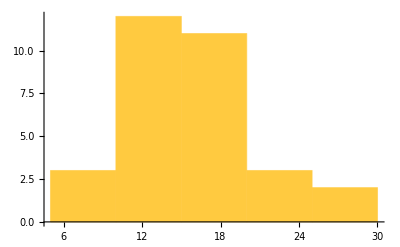

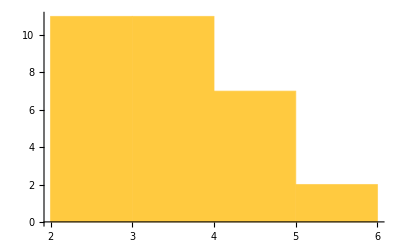

```mathematica
drespimport[[All,-1]]
Histogram[Rest[drespimport[[All,-2]]][[All,1]]](*closing volume as % of vital capacity*)
Histogram[Rest[drespimport[[All,-1]]][[All,1]]](*non-closing volume in liter*)
```

## Visualizing graphs for particle data

#### Data preparation

```mathematica
(*axes descriptions*)
descrPartpB="Particles per Breath \!\(\*StyleBox[\"P\",FontSlant->\"Italic\"]\) [1]";
descrInspV="Inspiratory Volume \!\(\*StyleBox[\"V\",FontSlant->\"Italic\"]\)\!\(\*StyleBox[\" \",FontSlant->\"Italic\"]\)[ml]";
descrInspDur="\n\nInspiratory\nDuration Δ\!\(\*StyleBox[\"t\",FontSlant->\"Italic\"]\)\n";
descrClosV="Closing Volume\nRange [ml]";

closingvolumerange=closingvolumerangeAll=Sort@dincl[[All,-1,2,-1]][[All,1]];
closingvolumerange=1000*Round[#,.1]&/@myTake[closingvolumerange,{1,-1}];

plotlegends=StringJoin[ToString@#," s\n"]&/@Flatten[Union/@GatherBy[Flatten[dincl[[All,1,2]],1],#[[6]]&][[All,All,6]]];

dinclWO0=Function[e,Select[e,#[[-1,1]]!=0.&]][#]&/@dincl[[All,1,2]];
(*no zeros in particle emssion*)

particleswithCI=Map[Around[#[[1]],#[[2]]]&,GatherBy[Flatten[dinclWO0,1],#[[6]]&][[All,All,-1]],{2}];
Print[Row[{"total data points\t",Length@Flatten[particleswithCI][[All,1]]}]];
vinsp=GatherBy[Flatten[dinclWO0,1],#[[6]]&][[All,All,2]];
vinspKat=GatherBy[Flatten[dinclWO0,1],#[[6]]&][[All,All,1]]; (*kategorial for statistics*)

replaceIntegerIndexToInspDur={1->"3 s",2->"2 s",3->"1 s",4->"0.5 s"};
particleswithCI=Map[Around[#["Value"],√((1.0+0.1)#["Value"]+1.0)]&,particleswithCI,{2}];
(*y error: The OPC datasheet specifies an error of around σ=10% for particle counts (not differentiated by particle size and ignoring additional high concentration count errors)*)
(* As particleswithCI already is an Around with Poisson error √(n+1), we need to correct this to √((1+σ)n+1) to consider the relative count error prior to the Poisson error

-Graphics-
Entscheidend sind die kleinen Durchmesser (also Datenpunkte 1-6,da>10 µm keine Partikel in meinen Messungen vorkommen).Hier ergibt sich meines Erachtens ein Fehler von 100-90 %=10 % 
-Graphics-

this error will be ignored, since:
Die Konzentration der Ausatemluft war maximal 15000 P/l.Der Fehler wäre also mit maximal 10% konservativ geschätzt. 
*) 


plotDataParVnoXerr=Map[Transpose,Transpose[{vinsp,particleswithCI}],{1}];
plotDataParVnoXerr=Map[Function[e,Select[e,(#[[2]]=!=0.Null)&]][#]&,plotDataParVnoXerr,{1}] (*0 as particle count is invalid and must be removed for log10-transformation*);
plotDataParVKat=Map[Function[e,Select[e,(#[[2]]=!=0.Null)&]][#]&,Map[Transpose,Transpose[{vinspKat,particleswithCI}],{1}],{1}];

flowMeterFlowAccuracyBelow150slm=0.04;
plotDataParV=Map[{Around[#[[1]],flowMeterFlowAccuracyBelow150slm#[[1]]],#[[2]]}&,plotDataParVnoXerr,{2}];
(** Add x Error Model if Mathematica Version 14.1 is available for 2D Error Fitting 

-Graphics-
-Graphics-
… ich würde 4 % als Fehler nehmen,da Flussraten 240 l/min beim Menschen nicht möglich sind (maximal 72 l/min).

**)

Table[
dataXLog10Y[i]=Transpose[{plotDataParV[[i,All,1]],Log10[plotDataParV[[i,All,2,1]]]}] (*log10 transformation of particle counts*);
dataLog10Yerrs[i]=Log10[plotDataParV[[i,All,2,2]]] (*from Sqr[n+1]*);
,{i,4}];
```

total data points	1610

#### Plots

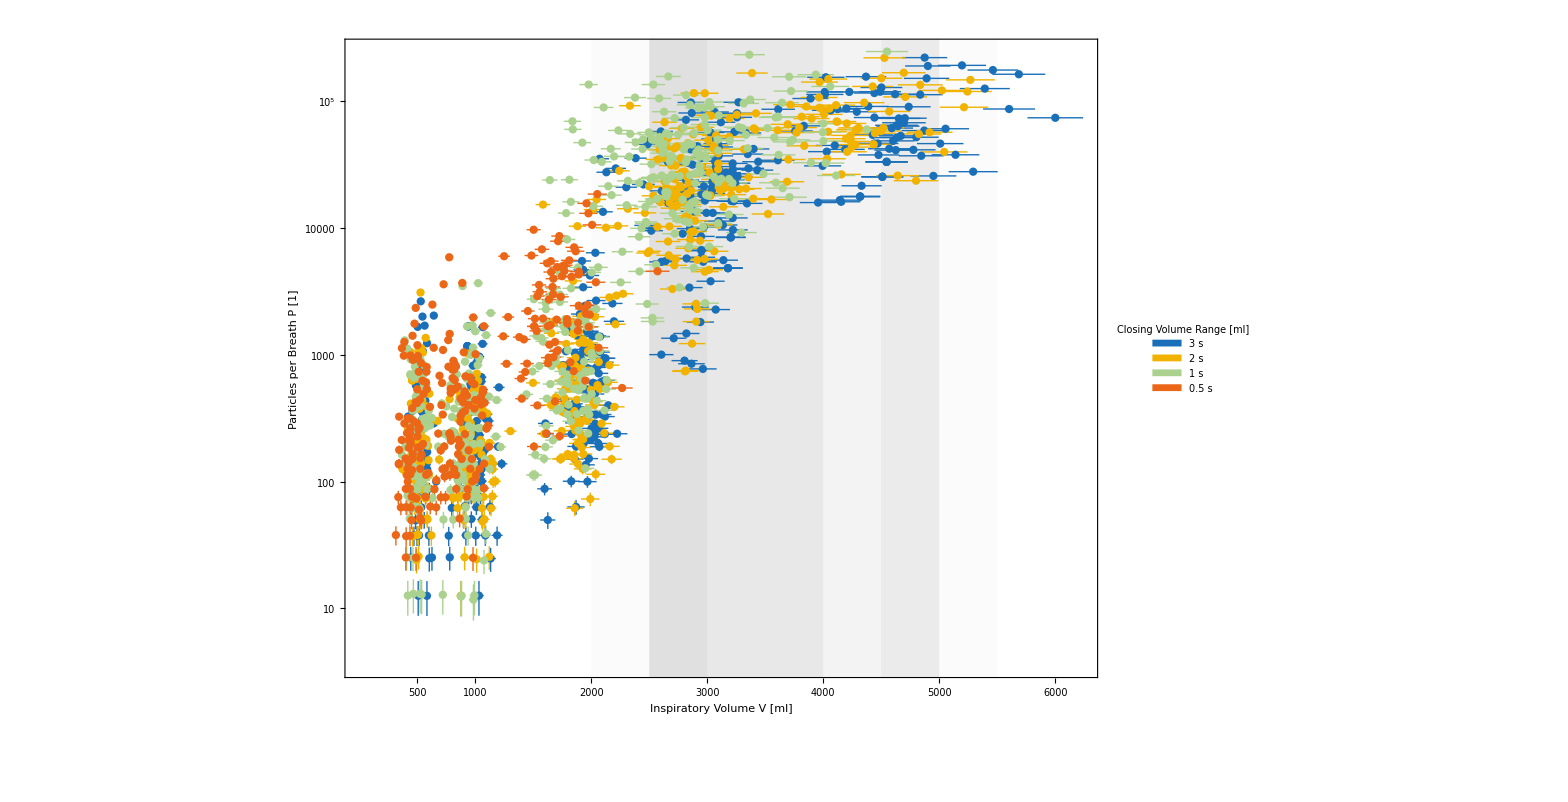

```mathematica
{closingvolumerangeHistoDataBins,closingvolumerangeHistoDataValues}=HistogramList[#,8]&@(1000*Round[#,.1]&/@closingvolumerangeAll);
closingvolumeHistogramRectangles={#[[1]],Rectangle@@#[[2]]}&/@({SetAlphaChannel[Lighter[Gray,.4],.4 #/Max[closingvolumerangeHistoDataValues]]&/@closingvolumerangeHistoDataValues,Map[Transpose,{Partition[closingvolumerangeHistoDataBins,2,1]
,ConstantArray[{0,10^5},Length@Partition[closingvolumerangeHistoDataBins,2,1]]}ᵀ,{1}]}ᵀ);

nFontSize=23;
nYCoor=12.75;

plotParticlesPerVolumeSubInspDur=ListPlot[plotDataParV,myPlotStyle[1,myPlotColors[[All,2]] ],PlotLegends->SwatchLegend[myStyle/@plotlegends,LegendMarkerSize->myFontSize,LegendMarkers->"Bubble",LegendLabel->Column[{Framed[Row[{myStyle[descrClosV]}],Background->Lighter[Gray,.75],FrameStyle->None],myStyle[descrInspDur]},Center]],ScalingFunctions->"Log",ImageSize->1300,Frame->True,FrameTicks->{Automatic,{{500,1000,2000,3000,4000,5000,6000},None}},myFrameStyle[],myFrameTickStyle[],FrameLabel->myStyle/@{descrInspV,descrPartpB},Prolog->{Flatten@closingvolumeHistogramRectangles,Text[myStyle["1",nFontSize],{2250,nYCoor}],Text[myStyle["8",nFontSize],{2750,nYCoor}],Text[myStyle["6",nFontSize],{3250,nYCoor}],Text[myStyle["6",nFontSize],{3750,nYCoor}],Text[myStyle["3",nFontSize],{4250,nYCoor}],Text[myStyle["5",nFontSize],{4750,nYCoor}],Text[myStyle["1",nFontSize],{5250,nYCoor}]}]
```

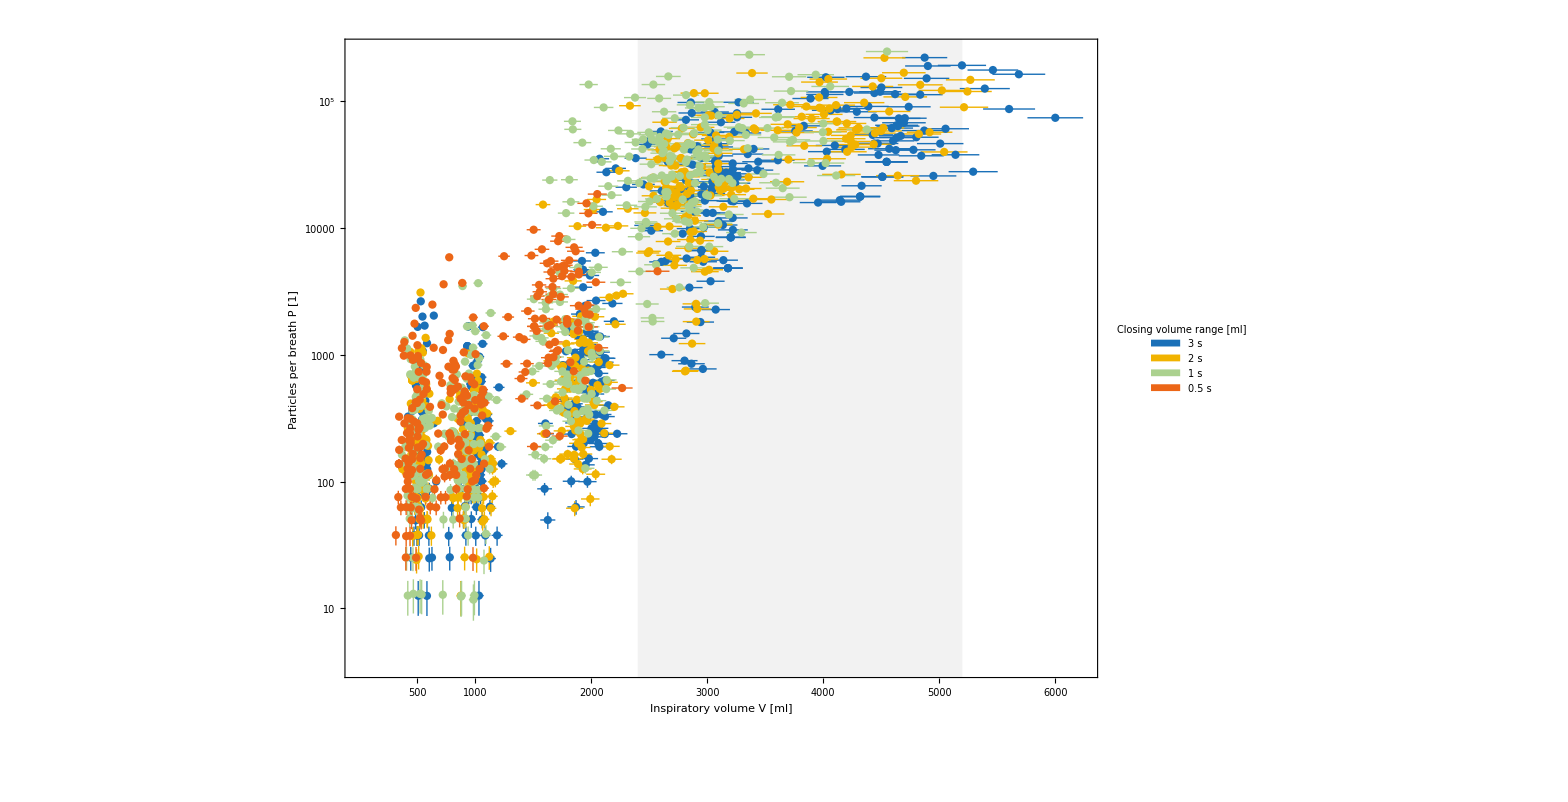
```mathematica
(* 
plotParticlesPerVolumeSubInspDur=ListPlot[plotDataParV,myPlotStyle[1,myPlotColors[[All,2]] ],PlotLegends->SwatchLegend[myStyle/@plotlegends,LegendMarkerSize->myFontSize,LegendMarkers->"Bubble",LegendLabel->Column[{Framed[myStyle[descrClosV],Background->Lighter[Gray,.9],FrameStyle->None],myStyle[descrInspDur]},Center]],ScalingFunctions->"Log",ImageSize->1300,Frame->True,FrameTicks->{{Automatic,Automatic},{{500,1000,2000,3000,4000,5000,6000},None}},myFrameStyle[],myFrameTickStyle[],FrameLabel->myStyle/@{descrInspV,descrPartpB},Prolog->{Lighter[Gray,.9],Rectangle[{closingvolumerange[[1]],0},{closingvolumerange[[2]],10^5}]}]



-Graphics-
*)
```

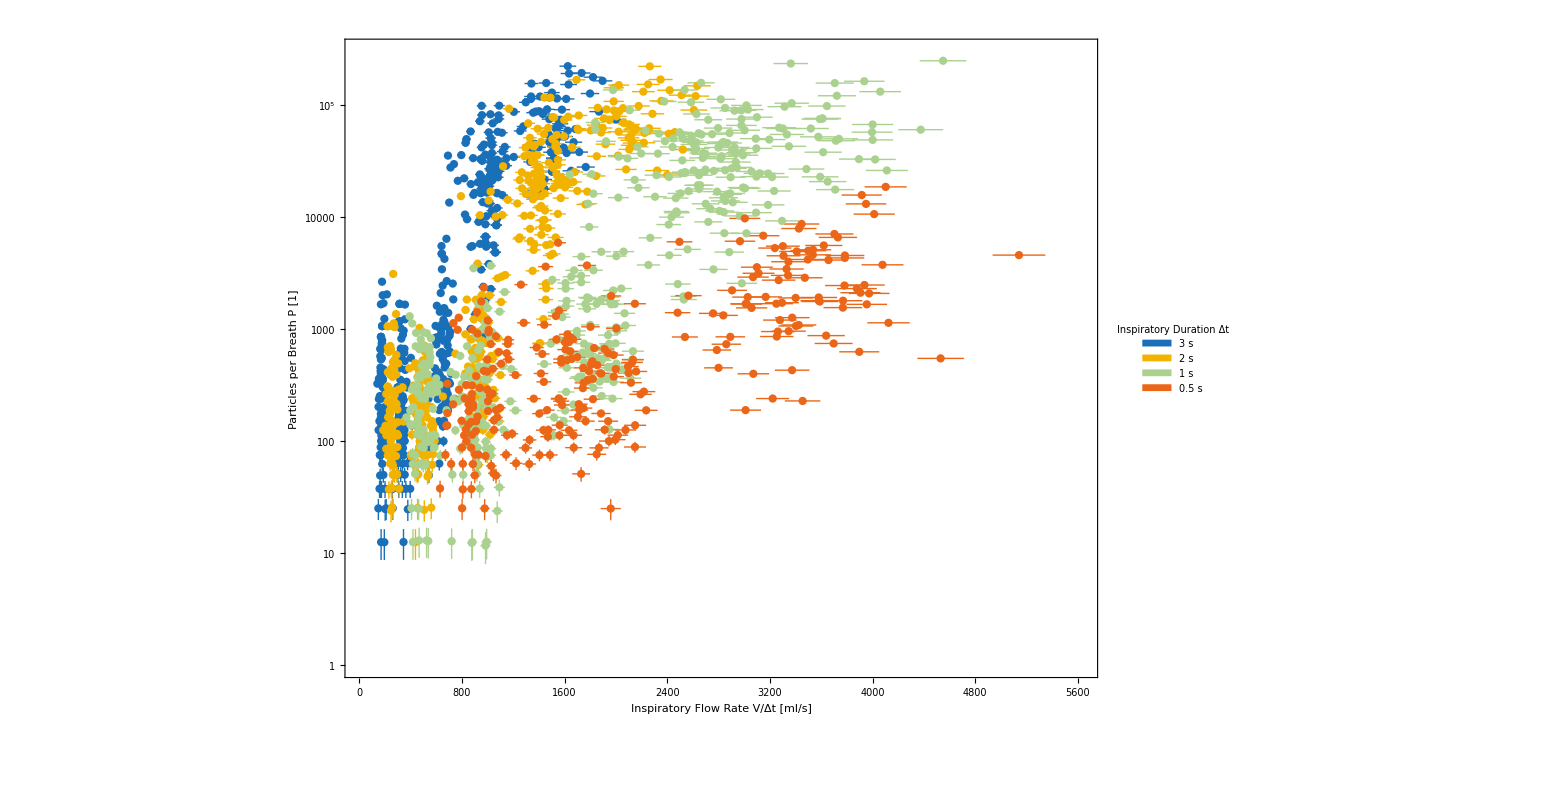

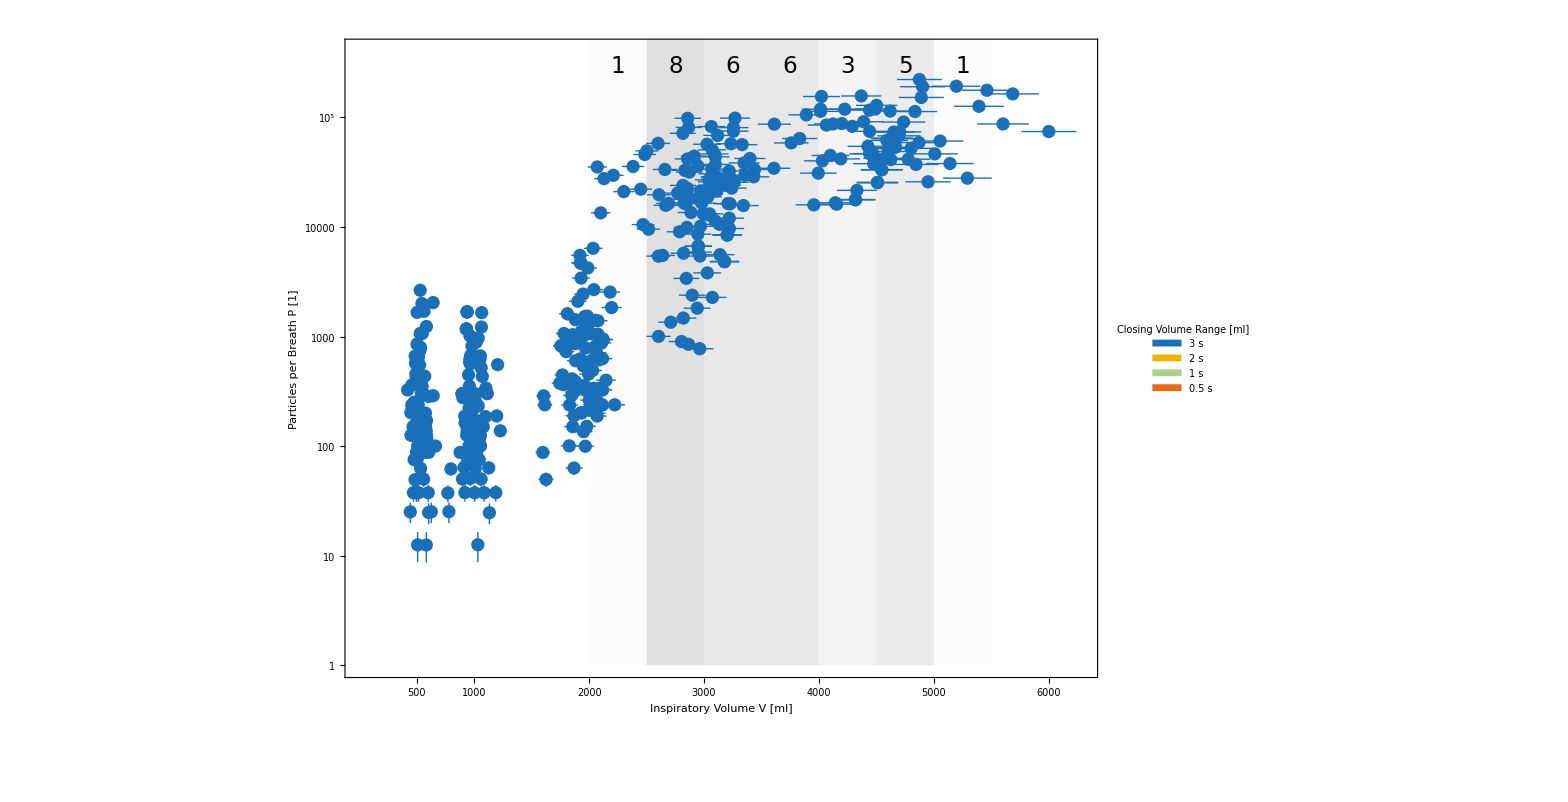
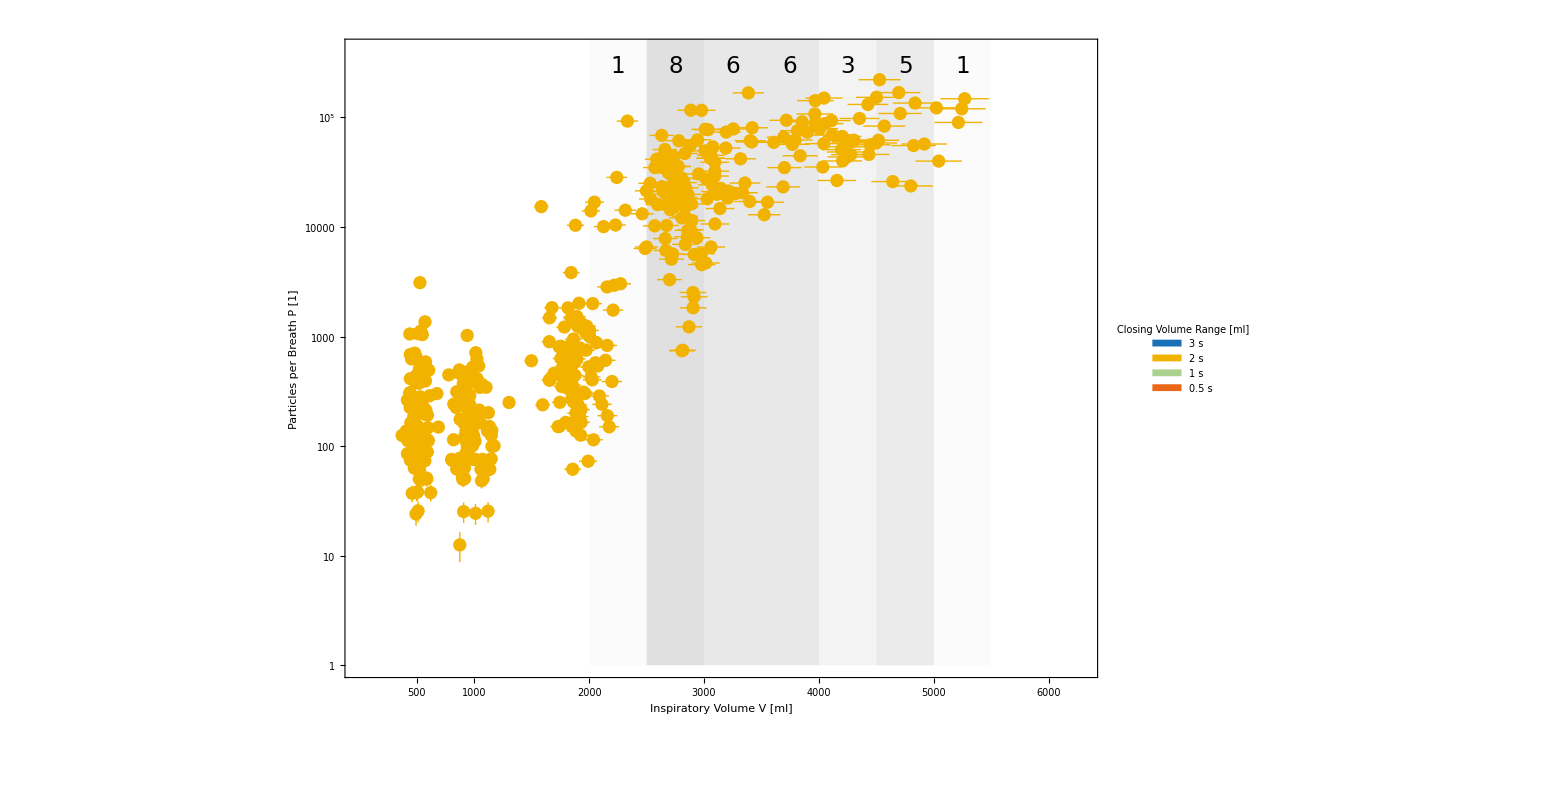
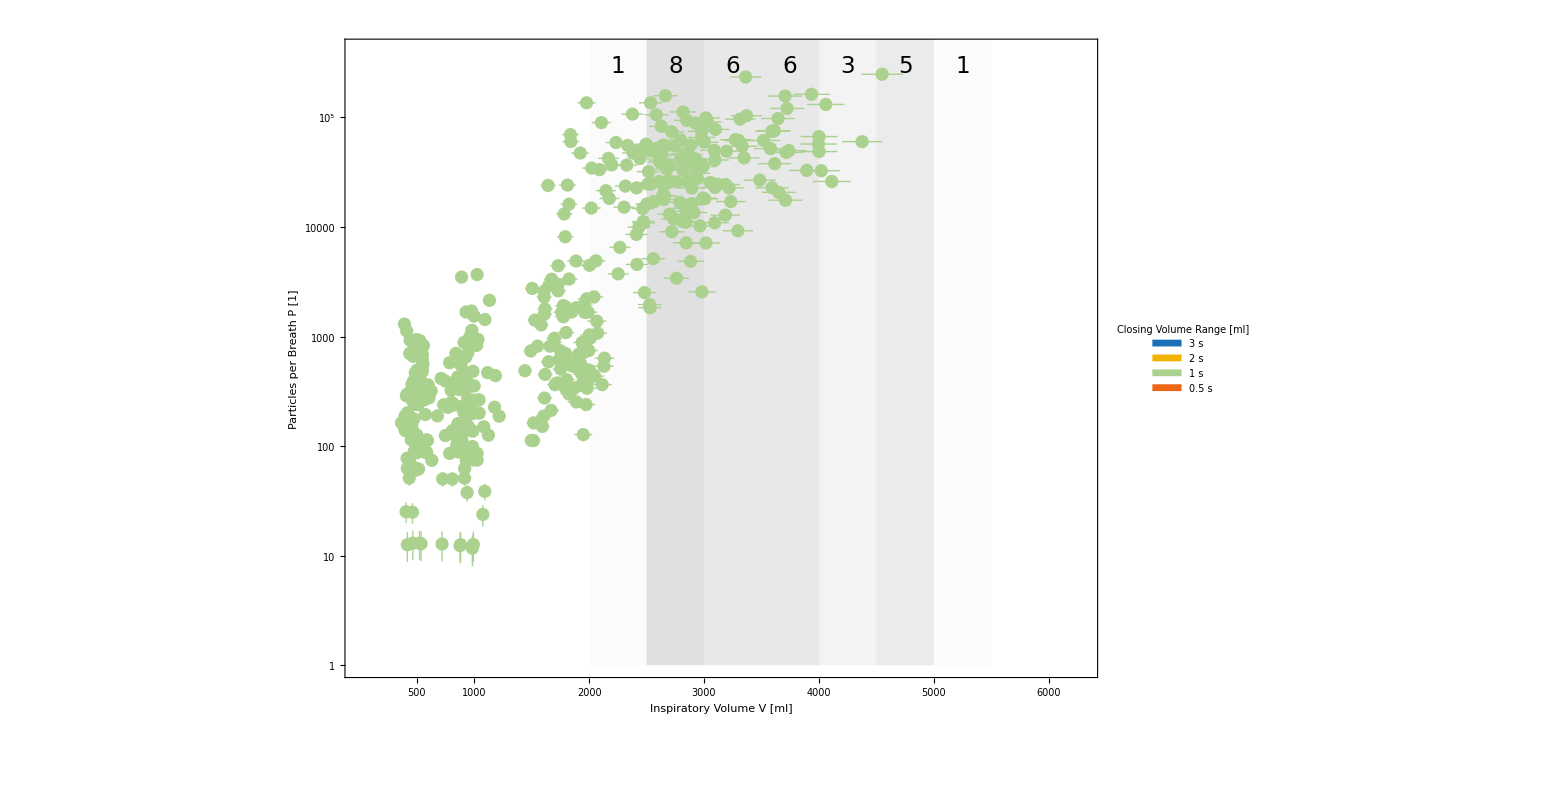
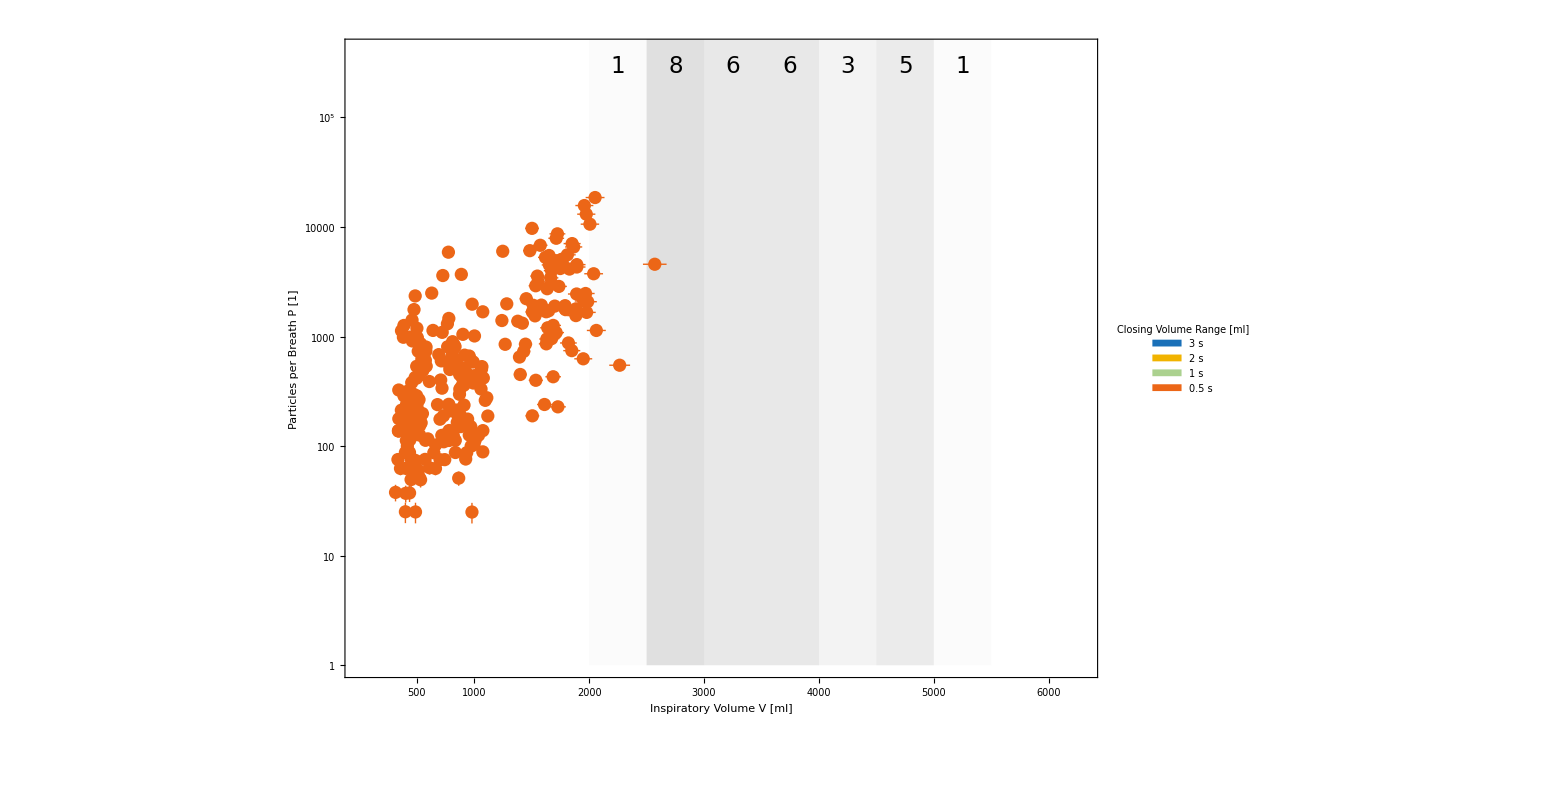

```mathematica
plotParticlesPerFlowRate=ListPlot[Transpose/@Transpose[{plotDataParV[[All,All,1]]/{3,2,1,.5},plotDataParV[[All,All,2]]}],myPlotStyle[1,myPlotColors[[All,2]]],PlotRange->{{0,500+Max[Flatten[(plotDataParV[[All,All,1]]/{3,2,1,.5})]]["Value"]},{1,3*10^5}},PlotLegends->SwatchLegend[myStyle/@plotlegends,LegendMarkerSize->myFontSize,LegendMarkers->"Bubble",LegendLabel->Column[{myStyle[descrInspDur]},Center]],ScalingFunctions->{Automatic,"Log"},ImageSize->1300,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,None}},myFrameStyle[],myFrameTickStyle[],FrameLabel->myStyle/@{"Inspiratory Flow Rate StyleBox[\"V\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"Δ\",FontSlant->\"Plain\"]StyleBox[\"t\",FontSlant->\"Italic\"] [ml/s]",descrPartpB}]

nYCoor=12.6;

plotParticlesPerVolumeSubInspDurSingle=ListPlot[ReplacePart[plotDataParV,#],myPlotStyle[1,myPlotColors[[All,2]]],PlotRange->{{0,6300},{1,4*10^5}},PlotLegends->SwatchLegend[myStyle/@plotlegends,LegendMarkerSize->myFontSize,LegendMarkers->"Bubble",LegendLabel->Column[{Framed[Row[{myStyle[descrClosV]}],Background->Lighter[Gray,.75],FrameStyle->None],myStyle[descrInspDur]},Center]],ScalingFunctions->"Log",ImageSize->1300,Frame->True,FrameTicks->{{Automatic,Automatic},{{500,1000,2000,3000,4000,5000,6000},None}},myFrameStyle[],myFrameTickStyle[],FrameLabel->myStyle/@{descrInspV,descrPartpB},Prolog->{Flatten@closingvolumeHistogramRectangles,Text[myStyle["1",nFontSize],{2250,nYCoor}],Text[myStyle["8",nFontSize],{2750,nYCoor}],Text[myStyle["6",nFontSize],{3250,nYCoor}],Text[myStyle["6",nFontSize],{3750,nYCoor}],Text[myStyle["3",nFontSize],{4250,nYCoor}],Text[myStyle["5",nFontSize],{4750,nYCoor}],Text[myStyle["1",nFontSize],{5250,nYCoor}]}]&/@Reverse@Map[#->{Null}&,Subsets[{1,2,3,4},{3}],{2}]
```

```mathematica
myExportF[{{plotParticlesPerVolumeSubInspDur,"001","plot particles per volume with subgroup inspiratory duration",600,False},{plotParticlesPerFlowRate,"002","plot particles per flow rate with subgroup inspiratory duration",600,False}}]
```

```mathematica
(*what is the range of particle emission from maximal breathing volume*)
maxPData=Select[#,#[[1]]==max&]&/@dincl[[All,1,2]];
MinMaxOfmaxPData=MinMax/@maxPData[[All,All,-1,1]];
SortBy[MinMaxOfmaxPData,First]
SortBy[MinMaxOfmaxPData,#[[2]]&]
```

{{10075.2,34476.6},{11199.5,33334.2},{11847.9,23232.7},{16624.6,90698.2},{17052.4,42175.7},{17545.2,61579.5},{19189.1,52468.1},{20678.7,58432.6},{21587.6,60083.2},{23958.9,32841.5},{24079.2,45123.1},{24406.9,126273.},{26560.8,66856.3},{26757.5,62212.9},{27692.5,69387.},{27944.4,57926.7},{34794.3,67863.},{36003.9,74916.3},{37228.7,74758.2},{40745.4,131296.},{40903.8,89142.7},{41692.4,87866.6},{45725.5,118889.},{46637.,192569.},{58512.6,90854.8},{61886.3,120673.},{75637.,167447.},{77672.5,156582.},{80663.5,135876.},{152072.,247580.}}

{{11847.9,23232.7},{23958.9,32841.5},{11199.5,33334.2},{10075.2,34476.6},{17052.4,42175.7},{24079.2,45123.1},{19189.1,52468.1},{27944.4,57926.7},{20678.7,58432.6},{21587.6,60083.2},{17545.2,61579.5},{26757.5,62212.9},{26560.8,66856.3},{34794.3,67863.},{27692.5,69387.},{37228.7,74758.2},{36003.9,74916.3},{41692.4,87866.6},{40903.8,89142.7},{16624.6,90698.2},{58512.6,90854.8},{45725.5,118889.},{61886.3,120673.},{24406.9,126273.},{40745.4,131296.},{80663.5,135876.},{77672.5,156582.},{75637.,167447.},{46637.,192569.},{152072.,247580.}}

## Function fitting

1st: Fit for the pooling of the first three data sets (without 0.5 sec insp duration)

4.69564	L from the fitting of the first 3 data sets (without .5 sec insp duration)

{L→4.69564,x0→2277.32,k→379.082,b→2.00568}

2.00568+2.68997/(1+ⅇ^(0.00263795 (2277.32-x)))

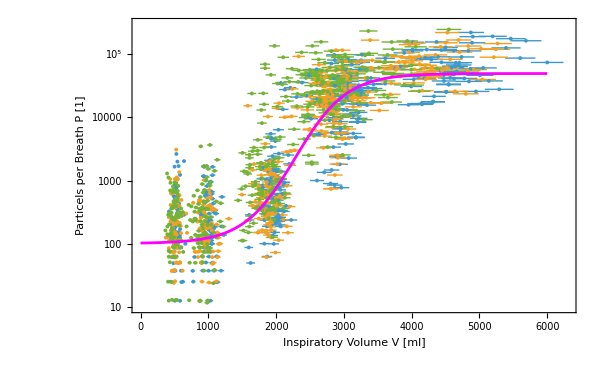

2nd: apply L from this first fit to all 4 data sets

Wenn Offset b freigegeben wird, führt das in Datenreihe 4 zu einer deutlichen Abweichung

3 s→{x0→2432.85,b→2.02006,k→425.648}

2 s→{x0→2352.66,b→2.0581,k→345.163}

1 s→{x0→2049.62,b→1.96693,k→353.844}

0.5 s→{x0→1719.59,b→1.69322,k→723.408}

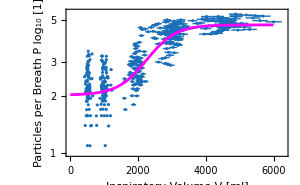
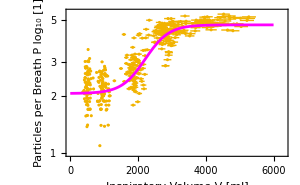
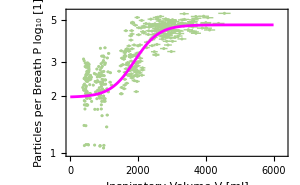
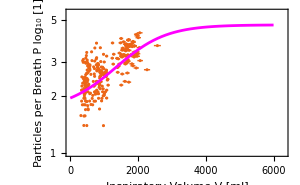

Die Inspirationsdauer von .5 Sekunden lässt physiologischerweise maximal 2-3 l Atemvolumen zu. Deshalb kann die Amplitude -b+L besser aus den ersten drei Messreihen bestimmt werden. b und L werden von dort übernommen und festgelegt.

b = 2.00568
L = 4.69564

3 s→{x0→2427.54,k→434.123}

2 s→{x0→2336.4,k→371.808}

1 s→{x0→2061.63,k→334.595}

0.5 s→{x0→1832.73,k→520.909}

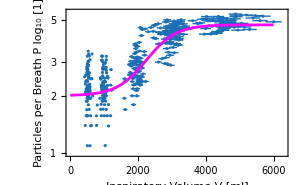
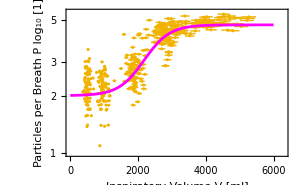
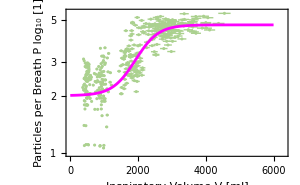
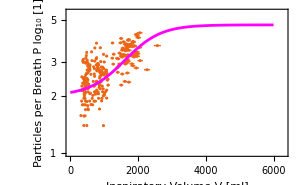

Dass sich für Datenreihe 4 die 'Zeitkonstante' k zu größeren Werten verschiebt, legt nahe, dass die gemeinsame Fitfunktion der 3 ersten Datenreihen eventuell für alle angewendet könnte.
Bzw. andersherum: wegen fehlender Datenpunkte > 2-3 l ist ein Fitting der Steilheit mit dem 4. Datenset nicht möglich
k wird aus dataXLog10YFitFirst3['BestFitParameters'] übernommen

b = 2.00568
L = 4.69564
k = 379.082

3 s→{x0→2395.16}

2 s→{x0→2339.83}

1 s→{x0→2080.79}

0.5 s→{x0→1716.8}

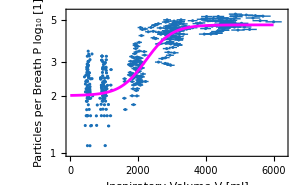
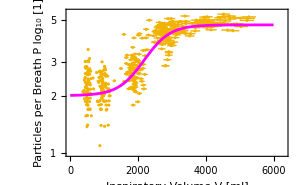
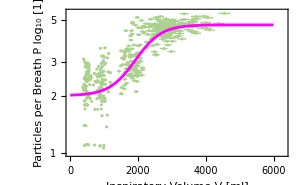
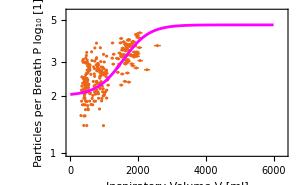

3 s→{x0→2395.16}

2 s→{x0→2339.83}

1 s→{x0→2080.79}

0.5 s→{x0→1716.8}

2.68997
2.00568 + -------------------------
               0.00263795 (-x + x0)
          1 + E

 x0 als Wendepunkt bleibt als einzige Variable frei für das Fitting und ist damit abhängig von der Inspirationsdauer

b = 2.00568
L = 4.69564
k = 379.082

3rd: 95 % confidence intervals (CI) are calculated from all combinations of the BestFit Parameters' CI and theirs MinMax values of the function combinations

General::munfl: Exp[-981.091] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-975.157] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1239.76] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

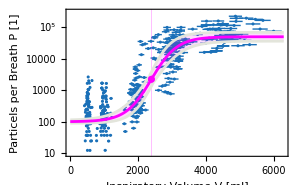
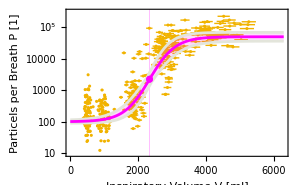
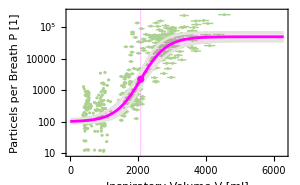
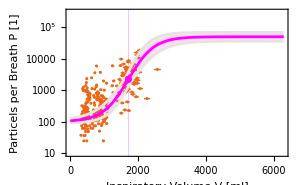

4th: midpoint values from all 4 data sets can be plotted and fitted by function A (1-Exp[-x/τ])

FittedModel[…]
{A→2356.96,τ→0.40444}

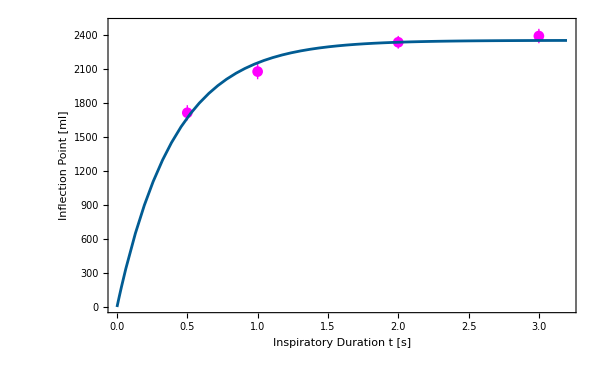

```mathematica
appendToExcelExportForWord=.;
appendToExcelExportForWord[in_]:=Module[{},AppendTo[excelExportForWord[[1,2]],If[NumberQ[#],Which[#>1,Round[#],#<1,Round[#,0.001],True,#],#]&//@(If[ListQ[in],Flatten[(If[(#[[1]]===L||#[[1]]===b),#[[1]]->10^#[[2]],#]&/@in)/. Rule->List],{in}])]]

Clear[dataFit,data,errs];
all4data=Join@@Map[Transpose[{#[[All,1]],Log10[#[[All,2,1]]]}]&,plotDataParV];

(*alle Datensätze mit log10-transformierter Partikelanzahl*)
first3data=Join@@Map[Transpose[{#[[All,1]],Log10[#[[All,2,1]]]}]&,plotDataParV[[1;;3]]];

(* nur die ersten 3 Datensätze mit log10-transformierter Partikelanzahl werden zusammengeworfen*)
first3dataYs=first3data[[All,2]];(* nur die ersten 3 log10-transformierten Partikelemissionsraten*)

(*based on the sigmoid logistic function we conduct a fitting

https://en.wikipedia.org/wiki/Logistic_function
Verhulst,Pierre-François (1847):Deuxième mémoire sur la loi d'accroissement de la population.In:Mémoires de l'académie impériale et royale des sciences et belles-lettres de bruxelles (20),S.1–32. Online verfügbar unter https://www.digizeitschriften.de/id/129323659_0020.

Cramer Mars (2002):The origins of logistic regression.In:Timbergen Institute Discussion Paper.Online verfügbar unter https://doi.org/10.2139%2Fssrn.360300.*)

(*Fitting with the first three data sets and wihtout 0.5 inspiratory duration*)
dataXLog10YFitFirst3=NonlinearModelFit[first3data,fitFunctionForFirst3data=b+(-b+L)/(1+ⅇ^((-x+x0)/k)),{{L,Max[first3data[[All,2]]]},{x0,2000.},{k,2000.},{b,Min[all4data[[All,2]]]}},x,Weights->1.0/(first3dataYs^2)];




excelExportForWord={"Fitting output for V & dt"->{{"1st: Fit for the pooling of the first three data sets (without 0.5 sec insp duration)"}}};

Print[myStyle["1st: Fit for the pooling of the first three data sets (without 0.5 sec insp duration)",myBAUAColors[1][[1]]]];

dataXLog10YFitFirst3BestFitParameters=Association[dataXLog10YFitFirst3["BestFitParameters"]];



Print[dataXLog10YFitFirst3BestFitParameters[L],"\tL from the fitting of the first 3 data sets (without .5 sec insp duration)"];
Print[dataXLog10YFitFirst3["BestFitParameters"]];
Print[dataXLog10YFitFirst3["BestFit"]];

myExportEquations[{{10^(dataXLog10YFitFirst3["BestFit"]/.x->Δt),"BestFit of pooled data for particles versus breathing volume, subgroup inspiratory duration"}}];

appendToExcelExportForWord[dataXLog10YFitFirst3["BestFitParameters"]];

frameLabel={"Inspiratory Volume StyleBox[\"V\",FontSlant->\"Italic\"] [ml]","Particels per Breath StyleBox[\"P\",FontSlant->\"Italic\"] [1]"};
xLabel="Inspiratory Volume StyleBox[\"V\",FontSlant->\"Italic\"] [ml]";

dataXLog10YFitFirst3Plot=Show[ListPlot[Transpose/@myT[plotDataParV[[All,All,1]],plotDataParV[[All,All,2,1]]][[1;;3]],PlotStyle->myPlotColors[[1;;3]],ScalingFunctions->"Log",FrameLabel->frameLabel,Frame->True,ImageSize->600,PlotRange->{{0,6300},{10.0,3.0 10^5}},myFrameStyle[],myFrameTickStyle[]],LogPlot[10^dataXLog10YFitFirst3[x],{x,0,6000},PlotStyle->Magenta]]

(*first fitting with all variables open except L

wheight = 1/σ^2 that is equal to 1/variance and equal to 1/Sqr[n+1]
*)
Print[myStyle["2nd: apply L from this first fit to all 4 data sets",myBAUAColors[1][[1]]]];
appendToExcelExportForWord["2nd: apply L from this first fit to all 4 data sets"];

replaceIntegerIndexToInspDur={1->"3 s",2->"2 s",3->"1 s",4->"0.5 s"};


Clear[dataXLog10Y,dataXLog10YFit,dataLog10Yerrs];

Print[Style["Wenn Offset b freigegeben wird, führt das in Datenreihe 4 zu einer deutlichen Abweichung",Bold,Larger]];
Print[Table[
dataXLog10Y[i]=Transpose[{plotDataParV[[i,All,1]],Log10[plotDataParV[[i,All,2,1]]]}] (*log10 transformation of particle counts*);dataLog10Yerrs[i]=Log10[plotDataParV[[i,All,2,2]]] (*from Sqr[n+1]*);dataXLog10YFit[i]=NonlinearModelFit[dataXLog10Y[i],{fitFunction=b+1/(1+ⅇ^((-x+x0)/k))(-b+dataXLog10YFitFirst3BestFitParameters[L]),0<k,0<b,0<x0<If[i==4,6000,6000]},{{x0,2000.},b,{k,20.}},x,Weights->1.0/(dataLog10Yerrs[i]^2)];


Print[(i/.replaceIntegerIndexToInspDur)->dataXLog10YFit[i]["BestFitParameters"]];
(*appendToExcelExportForWord[Join[{i/.replaceIntegerIndexToInspDur},{{"x0",dataXLog10YFit[i]},{"k",dataXLog10YFit[i]},{"b",10^dataXLog10YFit[i]}}]];*)
appendToExcelExportForWord[Prepend[dataXLog10YFit[i]["BestFitParameters"],(i/.replaceIntegerIndexToInspDur)->"->"]];

Show[ListLogPlot[dataXLog10Y[i],FrameLabel->{xLabel,StringReplace[descrPartpB  ,"[1]"->""]~~"log_10 [1]"},PlotStyle-> myPlotColors[[i,2]],Frame->True,ImageSize->300,PlotRange->{{0,6300},Log10/@{10.0,3.0 10^5}},myFrameStyle[14],myFrameTickStyle[14]],LogPlot[dataXLog10YFit[i][x],{x,0,6000},PlotStyle->Magenta]]

,{i,4}]]



(*second fitting with defined offset b and amplitude L*)
Print[Style["Die Inspirationsdauer von .5 Sekunden lässt physiologischerweise maximal 2-3 l Atemvolumen zu. Deshalb kann die Amplitude -b+L besser aus den ersten drei Messreihen bestimmt werden. b und L werden von dort übernommen und festgelegt.\n\n"~~"b = "~~ToString@dataXLog10YFitFirst3BestFitParameters[b]~~"\nL = "~~ToString@dataXLog10YFitFirst3BestFitParameters[L],Bold,Larger]];

appendToExcelExportForWord/@{"Physiologically, breathing volumes of > 2-3 l can not be breathed in 0.5 seconds. Thus, the amplitude -b+L will be taken from the pooled data fit from 1, 2, and 3 seconds.",{"b*"->10^dataXLog10YFitFirst3BestFitParameters[b]},{"L*"->10^dataXLog10YFitFirst3BestFitParameters[L]}};


Print[Table[
dataXLog10YFit[i]=NonlinearModelFit[dataXLog10Y[i],{fitFunction=dataXLog10YFitFirst3BestFitParameters[b]+1/(1+ⅇ^((-x+x0)/k))(-dataXLog10YFitFirst3BestFitParameters[b]+dataXLog10YFitFirst3BestFitParameters[L]),0<k,0<x0<If[i==4,6000,6000]},{{x0,2000.},{k,20.}},x,Weights->1.0/(dataLog10Yerrs[i]^2)];
Print[(i/.replaceIntegerIndexToInspDur)->dataXLog10YFit[i]["BestFitParameters"]];
appendToExcelExportForWord[Prepend[dataXLog10YFit[i]["BestFitParameters"],(i/. replaceIntegerIndexToInspDur)->"->"]];

Show[ListLogPlot[dataXLog10Y[i],FrameLabel->{xLabel,StringReplace[descrPartpB  ,"[1]"->""]~~"log_10 [1]"},PlotStyle-> myPlotColors[[i,2]],Frame->True,ImageSize->300,PlotRange->{{0,6300},Log10/@{10.0,3.0 10^5}},myFrameStyle[14],myFrameTickStyle[14]],LogPlot[dataXLog10YFit[i][x],{x,0,6000},PlotStyle->Magenta]]

,{i,4}]]



(*constraining of steepness k*)
Print[Style["Dass sich für Datenreihe 4 die 'Zeitkonstante' k zu größeren Werten verschiebt, legt nahe, dass die gemeinsame Fitfunktion der 3 ersten Datenreihen eventuell für alle angewendet könnte.
Bzw. andersherum: wegen fehlender Datenpunkte > 2-3 l ist ein Fitting der Steilheit mit dem 4. Datenset nicht möglich
k wird aus dataXLog10YFitFirst3['BestFitParameters'] übernommen"~~"\n\nb = "~~ToString@dataXLog10YFitFirst3BestFitParameters[b]~~"\nL = "~~ToString@dataXLog10YFitFirst3BestFitParameters[L]~~"\nk = "~~ToString@dataXLog10YFitFirst3BestFitParameters[k],Bold,Larger]];

appendToExcelExportForWord/@{"Since data points of >2 l are missing for 0.5 s, calculation of k is not reliable. All other three values of k are very close. k will be drawn form the pooled data fit.",{"k*"->dataXLog10YFitFirst3BestFitParameters[k]}};

Print[
Table[dataXLog10YFit[i]=NonlinearModelFit[dataXLog10Y[i],{fitFunction=dataXLog10YFitFirst3BestFitParameters[b]+(-dataXLog10YFitFirst3BestFitParameters[b]+dataXLog10YFitFirst3BestFitParameters[L])/(1+ⅇ^((-x+x0)/dataXLog10YFitFirst3BestFitParameters[k])),0<x0<6000},{{x0,2000.}},x,Weights->1.0/(dataLog10Yerrs[i]^2)];
Print[(i/.replaceIntegerIndexToInspDur)->dataXLog10YFit[i]["BestFitParameters"]];

appendToExcelExportForWord[Prepend[dataXLog10YFit[i]["BestFitParameters"],(i/. replaceIntegerIndexToInspDur)->"->"]];

Show[ListLogPlot[dataXLog10Y[i],FrameLabel->{xLabel,StringReplace[descrPartpB  ,"[1]"->""]~~"log_10 [1]"},PlotStyle-> myPlotColors[[i,2]],Frame->True,ImageSize->300,PlotRange->{{0,6300},Log10/@{10.0,3.0 10^5}},myFrameStyle[14],myFrameTickStyle[14]],LogPlot[dataXLog10YFit[i][x],{x,0,6000},PlotStyle->Magenta]]

,{i,4}]]




Style["only x0 as midpoint is free now, fit without constraints leads to the same result as the last fitFunction: see now, ConfidenceLevel→.95",Bold,Large];

appendToExcelExportForWord["only x0 as midpoint is free now, the following fit without constraints leads to the same result as the last fit"];

Table[
dataXY[i]=Transpose[{plotDataParV[[i,All,1]],plotDataParV[[i,All,2,1]]}];

dataXLog10YFitX0[i]=NonlinearModelFit[dataXLog10Y[i],fitFunction=dataXLog10YFitFirst3BestFitParameters[b]+(-dataXLog10YFitFirst3BestFitParameters[b]+dataXLog10YFitFirst3BestFitParameters[L])/(1+ⅇ^((-x+x0)/dataXLog10YFitFirst3BestFitParameters[k])),{{x0,2000.}},x,Weights->1.0/(dataLog10Yerrs[i]^2),ConfidenceLevel->.95];

Print[(i/. replaceIntegerIndexToInspDur)->dataXLog10YFitX0[i]["BestFitParameters"]];

appendToExcelExportForWord[Prepend[dataXLog10YFit[i]["BestFitParameters"],(i/. replaceIntegerIndexToInspDur)->"->"]];

,{i,4}];



Print[Style[ToString@fitFunction~~"\n\n x0 als Wendepunkt bleibt als einzige Variable frei für das Fitting und ist damit abhängig von der Inspirationsdauer"~~"\n\nb = "~~ToString@dataXLog10YFitFirst3BestFitParameters[b]~~"\nL = "~~ToString@dataXLog10YFitFirst3BestFitParameters[L]~~"\nk = "~~ToString@dataXLog10YFitFirst3BestFitParameters[k],Bold,Larger]];

appendToExcelExportForWord/@{"x0 as inflection point remains the free parameter depending on the inspiratory duration",
{"L*"->10^dataXLog10YFitFirst3BestFitParameters[L],"b*"->10^dataXLog10YFitFirst3BestFitParameters[b],
"k*"->dataXLog10YFitFirst3BestFitParameters[k]}};

Print[myStyle["3rd: 95 % confidence intervals (CI) are calculated from all combinations of the BestFit Parameters' CI and theirs MinMax values of the function combinations",myBAUAColors[1][[1]]]];


appendToExcelExportForWord["3rd: 95 % confidence intervals (CI) are calculated from all combinations of the BestFit Parameters' CI and theirs MinMax values of the function combinations"];


(*show confidence intervals, ConfidenceLevel->.95*)

(*Confidence Interval (CI) for each parameter is extracted from BestFit, then all combinations of CI-parameters are composed, from those only MinMax are extracted*)
dataXLog10YFitFirst3PCIwoX0=Select[MapThread[#1->#2&,{dataXLog10YFitFirst3["BestFitParameters"]⟦All,1⟧,dataXLog10YFitFirst3["ParameterConfidenceIntervals"]}],#[[1]]=!=x0&];
dataXLog10YFitX0PCI=Map[x0->#&,Table[First@dataXLog10YFitX0[i]["ParameterConfidenceIntervals"],{i,4}]];
dataXLog10YFitKeys=Join[Select[dataXLog10YFitFirst3["BestFitParameters"]⟦All,1⟧,#=!=x0&],{x0}];
dataXLog10YFitPCI=Map[Join[dataXLog10YFitFirst3PCIwoX0,{#}]&,dataXLog10YFitX0PCI];
allExtremeCombinationsForDataXLog10YFit=Map[Map[MapThread[#1->#2&,{dataXLog10YFitKeys,#}]&,Tuples[#[[All,2]]]]&,dataXLog10YFitPCI];
minMaxXLog10YFitCIFunctions[i]=Table[MinMax[fitFunctionForFirst3data/. allExtremeCombinationsForDataXLog10YFit[[i]]],{i,4}];

particleFitFunction={};
particleFitFunctionsCI={};
particleFitFunctionCIPlot={};

Table[
AppendTo[particleFitFunction,10^dataXLog10YFitX0[i]];
myExportEquations[{{10^(dataXLog10YFitX0[i]["BestFit"])/.x->V,"BestFit for " ~~ ToString[i/.replaceIntegerIndexToInspDur]~~" with L, k, b constrained, CI fit"}}];

AppendTo[particleFitFunctionsCI,Map[10^#&,MinMax[fitFunctionForFirst3data/.allExtremeCombinationsForDataXLog10YFit[[i]]]]];
appendToExcelExportForWord[{(i/.replaceIntegerIndexToInspDur)->#/.x->V}]&/@particleFitFunctionsCI[[i]];


AppendTo[particleFitFunctionCIPlot,Show[
ListLogPlot[dataXY[i],FrameLabel->{xLabel,frameLabel[[2]]},GridLines->{{{x0 /. dataXLog10YFitX0[i]["BestFitParameters"],Directive[Magenta,Thickness[.003/2]]}},None},PlotStyle->myPlotColors[[i,2]],Frame->True,ImageSize->600/2,PlotRange->{{0,6300},Identity/@{10.0,3.0 10^5}},myFrameStyle[myFontSize/2],myFrameTickStyle[myFontSize/2]]
,
LogPlot[Evaluate@Map[10^#&,MinMax[fitFunctionForFirst3data/.allExtremeCombinationsForDataXLog10YFit[[i]]]],{x,0,6300},Filling->{1->{2}},PlotStyle->myBAUAColors[4][[4]],FillingStyle->Directive[Opacity[0.15],Magenta]]
,
LogPlot[10^(dataXLog10YFitX0[i][x]),{x,0,6300},PlotStyle->Magenta]
,
ListLogPlot[{{x0 /. dataXLog10YFitX0[i]["BestFitParameters"],10^dataXLog10YFitX0[i]["Function"][x0 /. dataXLog10YFitX0[i]["BestFitParameters"]]}},PlotStyle->Magenta,PlotMarkers->{Automatic,Small(*Medium*)}]]]

,{i,4}];





Print[particleFitFunctionCIPlot];

particleFitFunctionCIPlotInGrid=Grid[{particleFitFunctionCIPlot[[1;;2]],particleFitFunctionCIPlot[[3;;4]]},Spacings->{2,2}];


Print[myStyle["4th: midpoint values from all 4 data sets can be plotted and fitted by function A (1-Exp[-x/τ])",myBAUAColors[1][[1]]]];

appendToExcelExportForWord["4th: midpoint values from all 4 data sets can be plotted and fitted by function A (1-Exp[-x/τ])"];

inspirationDuration={3,2,1,0.5};
x0Errors=Table[First@dataXLog10YFitX0[i]["ParameterConfidenceIntervals"],{i,4}];
x0s=Table[Association[dataXLog10YFitX0[i]["BestFitParameters"]][x0],{i,4}];
x0Physics=Transpose[{inspirationDuration,x0s}];
x0PhysicsAround=Transpose[{inspirationDuration,MapThread[Around[#1,#2]&,{x0s,x0Errors-x0s}]}];

x0Fit=NonlinearModelFit[x0Physics,{A (1-Exp[-x/τ]),0<A,0<τ},{{A,2354},{τ,0.392}},x];
myExportEquations[{{x0Fit["BestFit"]/.x->Δt,"BestFit for inflection points (charging function)"}}];


Print[x0Fit,"\n",x0Fit["BestFitParameters"]];
appendToExcelExportForWord[x0Fit["BestFitParameters"]];

Print[x0FitPlot=Show[ListPlot[x0PhysicsAround,PlotRange->{{0,3.2},{0,2500}},PlotStyle->Magenta,FrameLabel->{"Inspiratory Duration t [s]","Inflection Point [ml]"},Frame->True,myFrameStyle[],myFrameTickStyle[],ImageSize->600],Plot[x0Fit[x],{x,0,3.2},PlotStyle->myBAUAColors[4][[-3]],PlotRange->All]]];



parameterValueReplace=Replace[#, <|x0->x_|>-><|x0->x0Fit["BestFit"]|>]&/@Association/@Normal@dataXLog10YFitFirst3BestFitParameters;

P[V_,Δt_]:=10^fitFunctionForFirst3data/.x->V/.Flatten@Normal[parameterValueReplace]/.x->Δt

myExportEquations[{{10^fitFunctionForFirst3data/.x->V/.Flatten@Normal[parameterValueReplace]/.x->Δt,"unified equation for particle emission with parameteres V and dt"}}]
```

```mathematica
myExportF[{{dataXLog10YFitFirst3Plot,"003","best fit from pooled data V and dt",600,False},{particleFitFunctionCIPlotInGrid,"004","fit Function with CI for dt",600,False},{x0FitPlot,"005","fit Function with CI for dt",600,False}}]
```

## Overall data fit with unified function 10^(b+(L-b)/(1+ⅇ^((-Vinsp+A(1-Exp[-tinsp/τ]))/k))) including x and y errors

```mathematica
(*overallDataFit=Get[NotebookDirectory[]<>"Datenfit Ergebnis mit x und y Fehlern Gesamtformel.wl"] *)
```

```mathematica
overallDataFit=FittedModel[…];
```

### this result is calculated by the following fit. Attention: long computation process!

```mathematica
tinspValues={3,2,1,.5};
tinspDataXYErrorsH10=Join@@MapThread[Transpose[{#1[[All,1]],ConstantArray[#2,Length[#1]],#1[[All,2]]}]&,{plotDataParV,tinspValues}];

If[ChoiceDialog[TextCell["Soll der Datenfit gestartet werden?\n\nDies ist ein rechenintensiver Prozess!"],WindowTitle->"Lange Berechnung starten?"]===True

,Print[AbsoluteTiming[dataXLog10YAllDataAllAndAllParametersXYErrors=NonlinearModelFit[tinspDataXYErrorsH10,{fitFunctionForAllDataAllAndAllParameters=10^(b+(L-b)/(1+ⅇ^((-Vinsp+A(1-Exp[-tinsp/τ]))/k))),1.5<b<3.0,4.0<L,6.0<k<1500,1500<A<2600,0.1<τ<2},{{L,4.75},{k,390.},{b,2.2},{A,2300},{τ,0.4}},{Vinsp,tinsp}]]];
Print@dataXLog10YAllDataAllAndAllParametersXYErrors;
Print@dataXLog10YAllDataAllAndAllParametersXYErrors["ParameterEstimates"];

Save[exPath<>"overall data fit result with x and y errors.wl",dataXLog10YAllDataAllAndAllParametersXYErrors]
]
```

```mathematica
(* excelExportForWord[[1,2]]=excelExportForWord[[1,2]]/. (#->Nothing&/@excelExportForWord[[1,2]][[39;;67]]) *)
```

```mathematica
appendToExcelExportForWord["overall data fit result with x and y errors"];
excelExportForWord[[1,2]]=Join[excelExportForWord[[1,2]],If[NumberQ[#],Round[#,0.001],#]&//@(Flatten/@(Normal/@Normal[overallDataFit["ParameterEstimates"]]/. Rule->List))];
appendToExcelExportForWord[{{"r squared of overall fit result with x and y errors",Round[#,0.001]&@overallDataFit["RSquared"],"estimate of the error variance of overall fit result with x and y errors",Round[#,0.001]&@overallDataFit["EstimatedVariance"]}}];
```

FittedModel::constr: The property values {ParameterEstimates} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-3409.83] is too small to represent as a normalized machine number; precision may be lost.

FittedModel::constr: The property values {EstimatedVariance} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

```mathematica
xRange=Sequence[0,6300];
yRange=Sequence[0.,3.25];

tinspValues=ToExpression[(StringSplit[#," "]&/@replaceIntegerIndexToInspDur[[All,2]])[[All,1]]];
volumeTimeParticlesDataWithError=Join@@MapThread[Transpose[{#1[[All,1]],ConstantArray[#2,Length[#1]],#1[[All,2]]}]&,{plotDataParV,tinspValues}];

Column[{myStyle["Fit with x- and y-errors",Bold],overallDataFit["BestFitParameters"]},Center]

overallDataFitPlot3D=Show[
ListPointPlot3D[volumeTimeParticlesDataWithError,PlotStyle->{PointSize[0.015/3 2],Directive[Opacity[0.5]]},ColorFunction->"Rainbow",IntervalMarkers->"Bars", IntervalMarkersStyle->Directive[Opacity[0.75],Black],AxesLabel->{descrInspV,"Inspiratory Duration t [s]",descrPartpB},myLabelStyle[16],PlotRange->{{xRange},{yRange},Full},ScalingFunctions->"Log10"]
,Plot3D[overallDataFit[Vinsp,tinsp],{Vinsp,xRange},{tinsp,yRange},
PlotStyle->Directive[Opacity[0.7],Gray,Specularity[White,25]](*,ColorFunction->"Rainbow"*),Mesh->{Range[0,6000,500],{0.5,1,2,3}},Lighting->"Accent",ScalingFunctions->"Log10"],ImageSize->1000,ViewPoint->(vp={-5,10,3}+0{-10,5,3})]
```

Fit with x- and y-errors
{L→4.99252,k→627.131,b→1.66727,A→1906.68,τ→0.364895}

-Graphics3D-

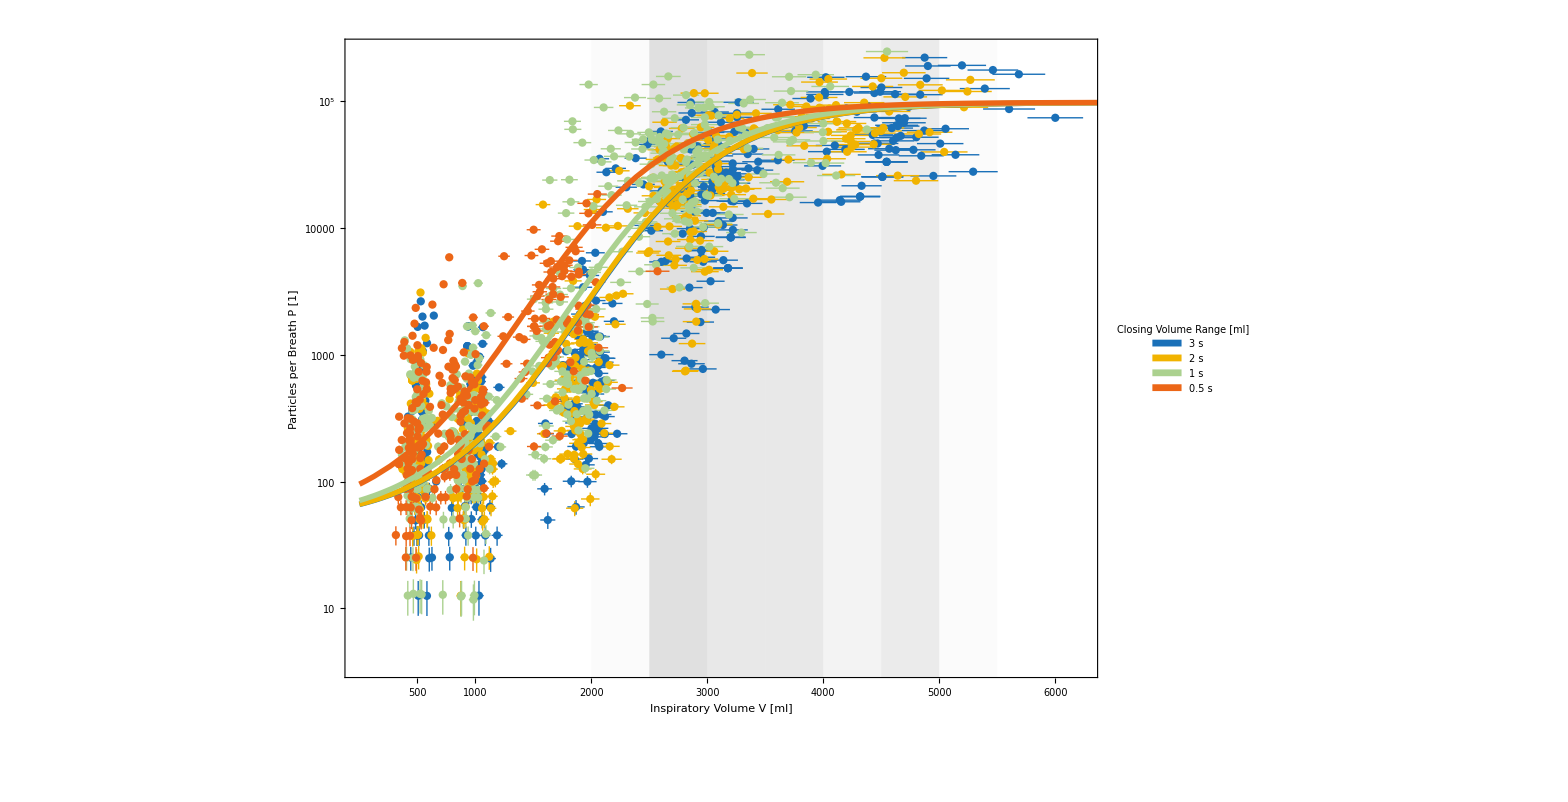

```mathematica
plotParVΔtwithFunc=Show[Join[{plotParticlesPerVolumeSubInspDur},Table[LogPlot[overallDataFit[Vinsp,i],{Vinsp,0,6500},PlotStyle->Directive[(i/.myPlotColors),Thickness[.003]]],{i,{3,2,1,0.5}}]]]
```

```mathematica
myExportF[{{overallDataFitPlot3D,"046","3d plot with inspiratory volume and inspiratory duration data and overall fit result including errors",600,False},{plotParVΔtwithFunc,"006","scatter plot of particle emission versus breathing volume, subgroup inspiratory duration, including fit curves",600,False}}]
```

```mathematica
(* CloudPublish[overallDataFitPlot3D] *)
online3dPlotOverallFit=CloudObject[["https://www.wolframcloud.com/obj/34f7c6c2-dfca-460f-9edf-157c55e00f8d"](https://www.wolframcloud.com/obj/34f7c6c2-dfca-460f-9edf-157c55e00f8d)];
appendToExcelExportForWord[{{"URL for online 3D plot of overall fit",online3dPlotOverallFit[[1]]}}];


Export[exPath~~"parameters' value output for word.xlsx",excelExportForWord]
```

D:\Daten\b1464\Desktop\Ausgabe\parameters' value output for word.xlsx

## Propagation of uncertainty

```mathematica
masterFormel=.
masterFormel[A_,b_,k_,L_,τ_,tinsp_,Vinsp_]:=10^(b+(L-b)/(1+ⅇ^((-Vinsp+A(1-Exp[-tinsp/τ]))/k)))
```

```mathematica
overallDataFit["ParameterEstimates"]
```

FittedModel::constr: The property values {ParameterEstimates} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-3409.83] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
p=overallDataFit["ParameterEstimates"][All,"Parameter"]//Normal//Quiet
v=overallDataFit["ParameterEstimates"][All,"BestFitValue"]//Normal//Quiet
σ=overallDataFit["ParameterEstimates"][All,"StandardError"]//Normal//Quiet
twoσonvalue={v-σ*2,σ*2+v}ᵀ
ci=overallDataFit["ParameterEstimates"][All,"ConfidenceInterval"]//Normal//Quiet
σFactor=2;
MapThread[#1->#2&,{p,MapThread[Around[#1,#2]&,{v,σFactor σ}]}]
```

{L,k,b,A,τ}

{4.99252,627.131,1.66727,1906.68,0.364895}

{0.0150355,43.0665,0.110654,76.2525,0.0271817}

{{4.96245,5.02259},{540.998,713.264},{1.44597,1.88858},{1754.18,2059.19},{0.310532,0.419259}}

{{4.96303,5.02201},{542.659,711.604},{1.45023,1.88432},{1757.12,2056.25},{0.31158,0.418211}}

{L→4.9930.030,k→627.86.,b→1.670.22,A→1907.153.,τ→0.360.05}

```mathematica
σFactor=Subscript[n, "σ"];
masterFormelNσ=masterFormel@@({A,b,k,L,τ,tinsp,Vinsp}/.MapThread[#1->#2&,{p,MapThread[Around[#1,#2]&,{v, σFactor σ}]}])

masterFormelNσF=.
masterFormelNσF=masterFormel@@({A,b,k,L,τ,tinsp,Vinsp}/.MapThread[#1->#2&,{p,MapThread[Around[#1,#2]&,{v, σFactor σ}]}])

σFactor=2;
masterFormel2σ=masterFormel@@({A,b,k,L,τ,tinsp,Vinsp}/.MapThread[#1->#2&,{p,MapThread[Around[#1,#2]&,{v, σFactor σ}]}])

firleequation=.
firleequation[Vinsp_,tinsp_]:=masterFormel@@({A,b,k,L,τ,tinsp,Vinsp}/.MapThread[#1->#2&,{p,MapThread[Around[#1,#2]&,{v, 2σ}]}])

onlineCalculator= CloudObject[["https://www.wolframcloud.com/obj/191029e2-e2d4-402b-8473-64d35f196ca7"](https://www.wolframcloud.com/obj/191029e2-e2d4-402b-8473-64d35f196ca7)]
(*
CloudPublish[FormFunction[{"v"->"Real","t"->"Real"},Style[Column[{Row[{ToString[NumberForm[Round@firleequation[#v,#t]["Value"],DigitBlock->3]]," particles per breath"}],Row[{"95% CI: ",ToString[NumberForm[Round[firleequation[#v,#t]["Value"]-firleequation[#v,#t]["Uncertainty"]],DigitBlock->3]]," - ",ToString[NumberForm[Round[firleequation[#v,#t]["Value"]+firleequation[#v,#t]["Uncertainty"]],DigitBlock->3]]}]}],FontFamily->"Lucida Sans Unicode",FontSize->20]&,AppearanceRules-><|"Title"->myStyle["Calculate the human aerosol emission per breath with 95% confidence interval",20],"Description"->myStyle["Enter\nthe inspiratory volume [ml] as v and<br>the inspiratory duration [s] as t<br>use real numbers",16]|>]] 

*)


appendToExcelExportForWord[{{"URL for online calculator",onlineCalculator[[1]]}}];
Export[exPath~~"parameters' value output for word.xlsx",excelExportForWord]
```

10^((1.667270.110654 n_σ)+(3.325240.111671 √(n_σ^2))/(1+ⅇ^((0.001594560.000109502 Abs[n_σ]) (-Vinsp+(1-ⅇ^(tinsp (-2.740510.204145 Abs[n_σ]))) (1906.6876.2525 n_σ)))))

10^((1.667270.110654 n_σ)+(3.325240.111671 √(n_σ^2))/(1+ⅇ^((0.001594560.000109502 Abs[n_σ]) (-Vinsp+(1-ⅇ^(tinsp (-2.740510.204145 Abs[n_σ]))) (1906.6876.2525 n_σ)))))

10^((1.670.22)+(3.330.22)/(1+ⅇ^((0.001590.00022) (-Vinsp+(1-ⅇ^(tinsp (-2.70.4))) (1907.153.)))))

CloudObject[https://www.wolframcloud.com/obj/191029e2-e2d4-402b-8473-64d35f196ca7]

C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\output\parameters' value output for word.xlsx

```mathematica
myExportEquations[{{10^(b+(L-b)/(1+ⅇ^((-Vinsp+A(1-Exp[-tinsp/τ]))/k))),"overall data fit equation with variables"},{masterFormelNσ,"overall data fit equation with n x Sigma to choose"},{masterFormel2σ,"overall data fit equation with 95-CI"}}];
```

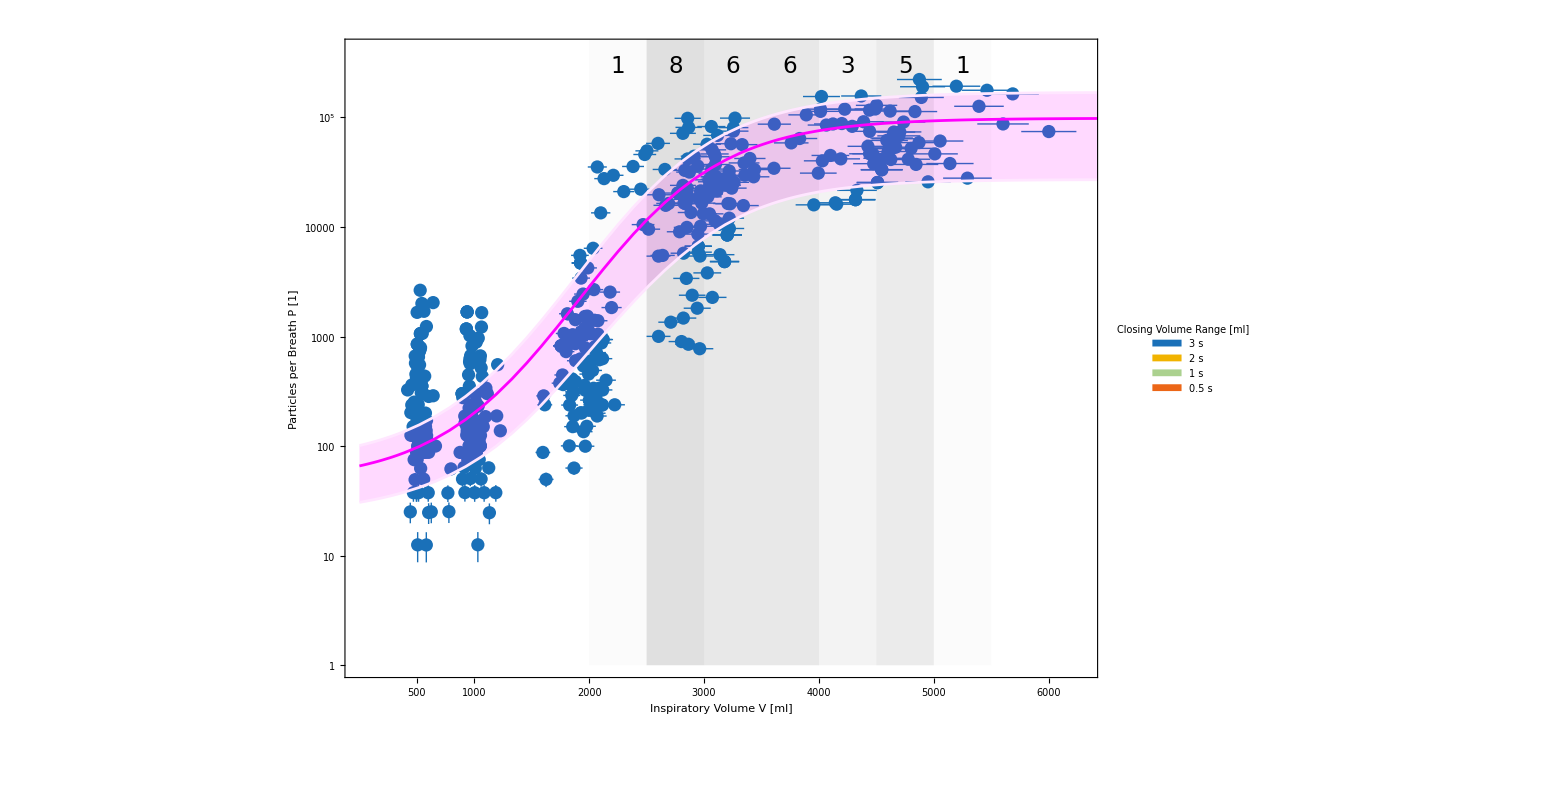
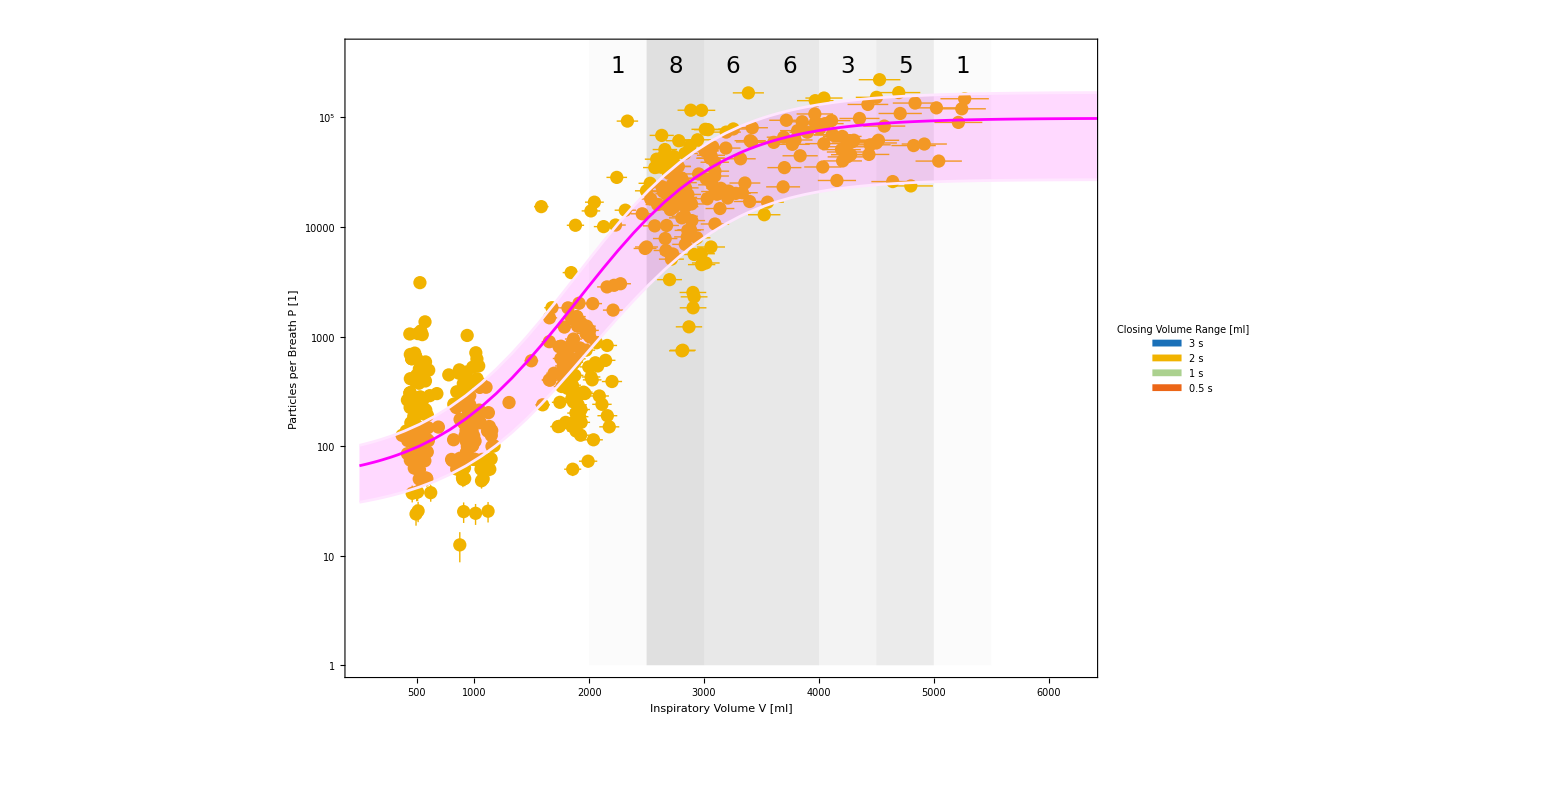
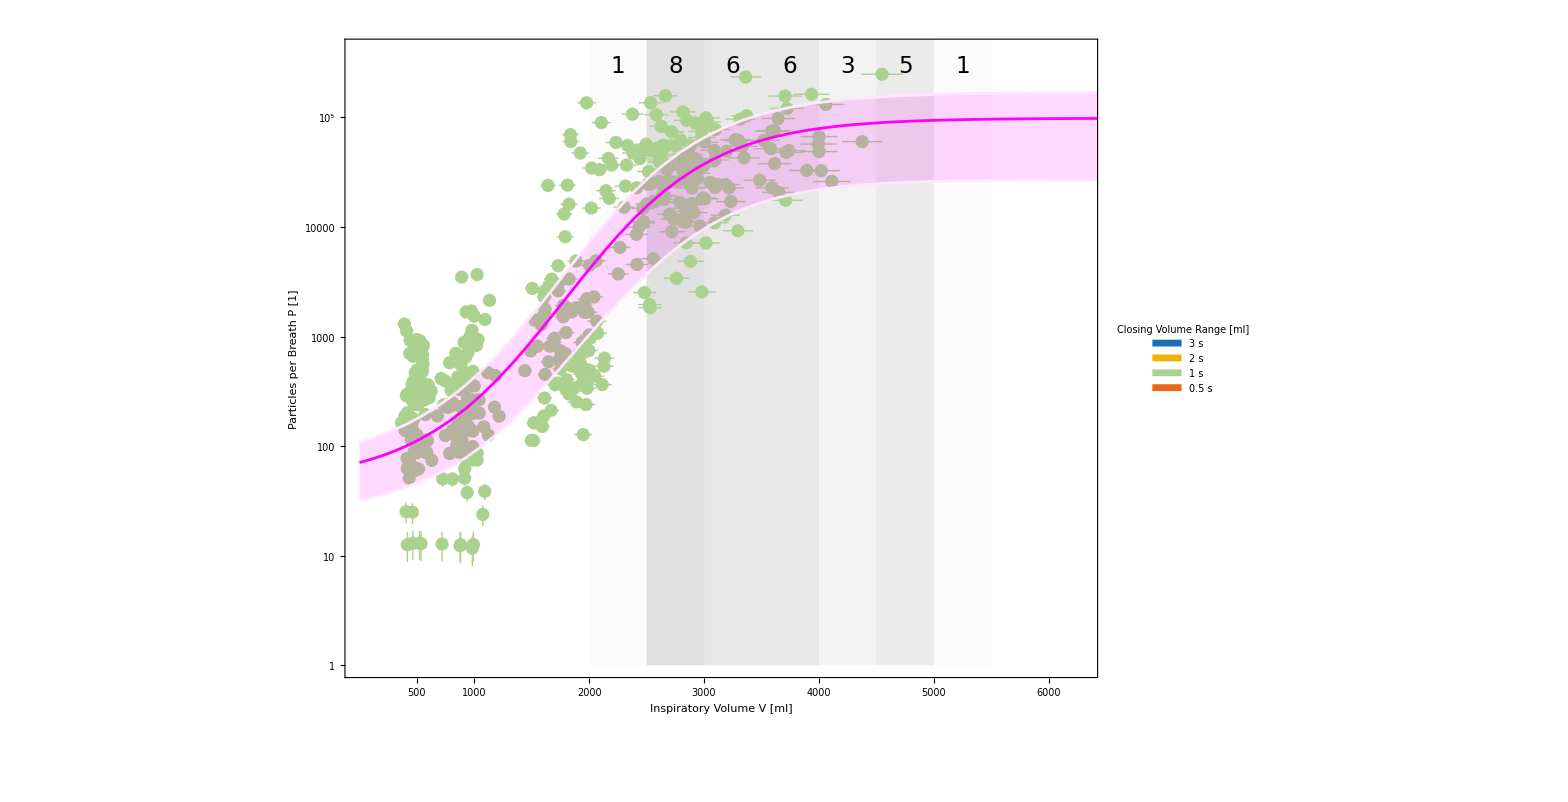
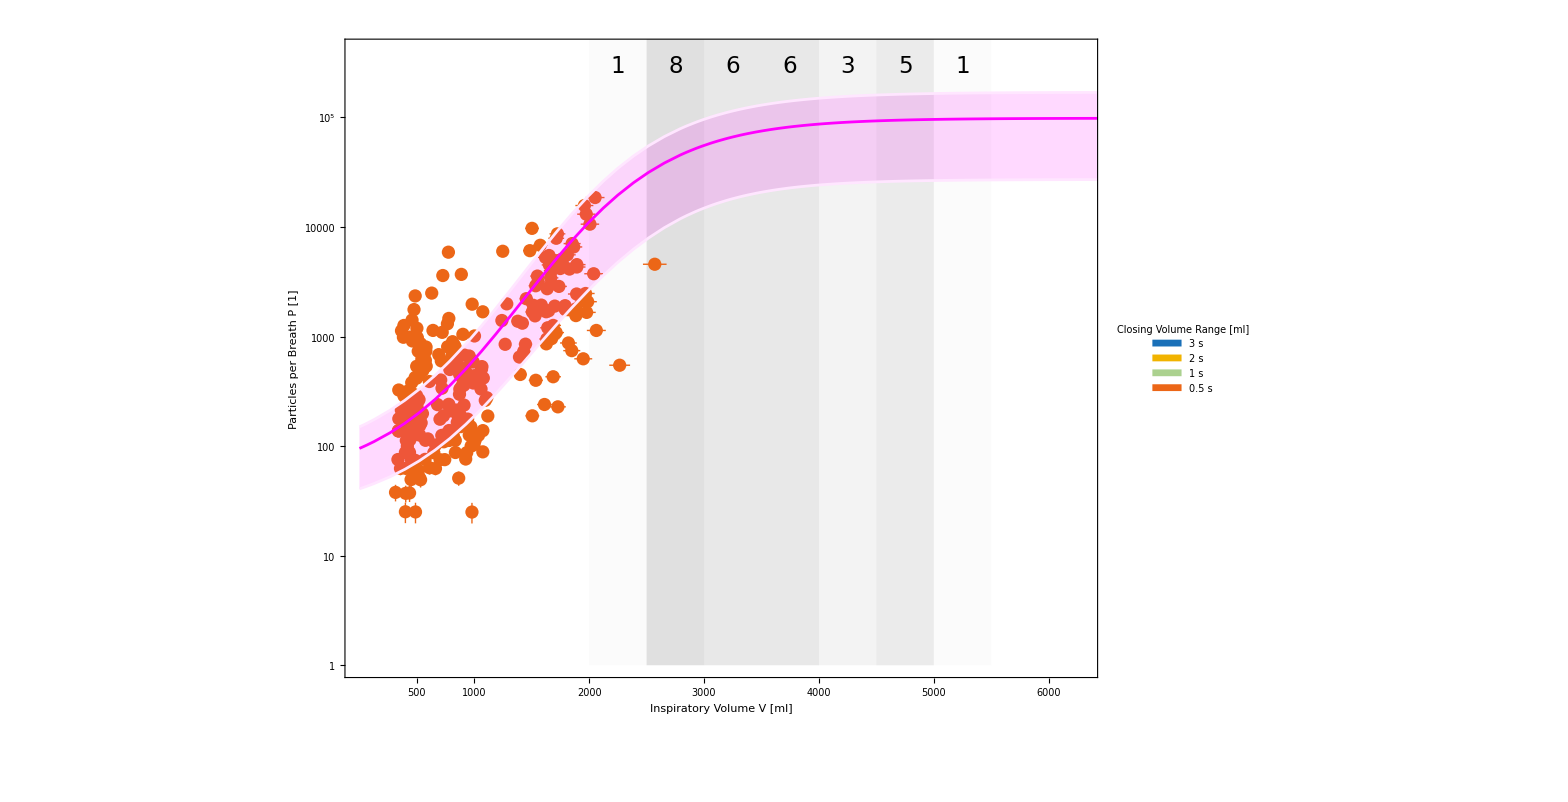
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
overallFit95CIPlots=Table[Show[plotParticlesPerVolumeSubInspDurSingle[[i]],LogPlot[{(firleequation[Vinsp,myPlotColors[[All,1]][[i]]])["Value"],List@@(firleequation[Vinsp,myPlotColors[[All,1]][[i]]])["Interval"]},{Vinsp,0,6500},Filling->{1->{{2},Directive[Opacity[0.15],Magenta]}},PlotStyle->{Magenta,LightMagenta,LightMagenta}]],{i,4}];

overallFit95CIPlotsInGrid=Grid[{overallFit95CIPlots[[1;;2]],overallFit95CIPlots[[3;;4]]},Spacings->{3,2}]
```

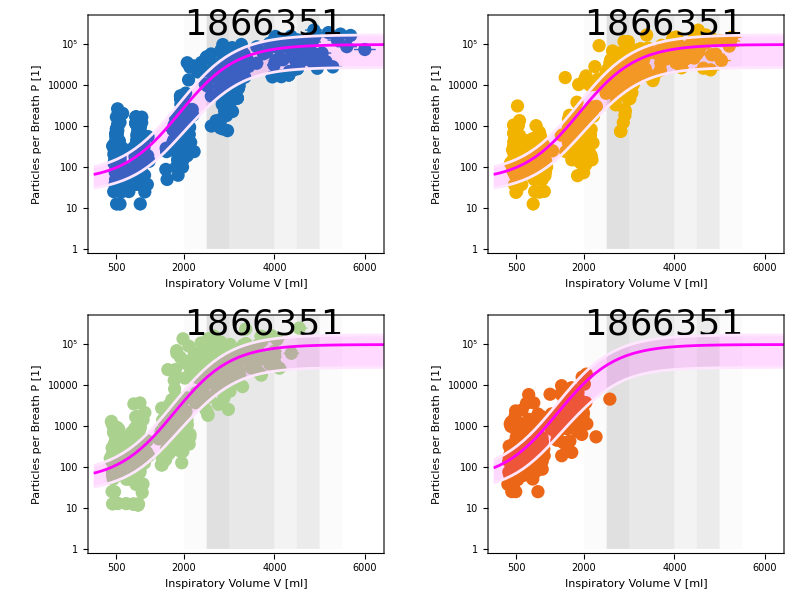

```mathematica
overallFit95CIPlotsRevision=overallFit95CIPlots[[All,1]] /. (FontSize->a__)->(FontSize->35);
overallFit95CIPlotsInGridRevision=Labeled[Grid[{overallFit95CIPlotsRevision[[1;;2]],overallFit95CIPlotsRevision[[3;;4]]},Spacings->{4,5}],Magnify[overallFit95CIPlots[[1,2,1]],2],Right]
```

```mathematica
myExportF[{{overallFit95CIPlotsInGridRevision,"047","overall data fit plots with 95-CI in grid for inspiratory durations",300,False}}]
```

## Particle data referred to respiratory data

```mathematica
plotlegends=StringJoin[ToString@#," s\n"]&/@Flatten[Union/@GatherBy[Flatten[dincl[[All,1,2]],1],#[[6]]&][[All,All,6]]];

preparePlotParRespD=.
preparePlotParRespD[l_List,colResp_Integer,nameResp_String,subset_Symbol:False]:=Module[{particeswithCI,l2,vinsp,plotDataParResp,plotDataParRespKat},
particeswithCI=Map[Around[#[[1]],√((1.0+0.1)#[[1]]+1.0)]&,GatherBy[Flatten[l[[All,1,2]],1],#[[6]]&][[All,All,-1]],{2}];

l2=l;
l2[[All,1,2,All,2]]=((Map[Around[#,flowMeterFlowAccuracyBelow150slm#]&,(l2[[All,1,2,All,2]]/1000),{2}])/l2[[All,-1,2]][[All,colResp]])*100;
vinsp=GatherBy[Flatten[l2[[All,1,2]],1],#[[6]]&][[All,All,2]];

plotDataParResp=Map[Transpose,Transpose[{vinsp,particeswithCI}],{1}];
plotDataParResp=Map[Function[e,Select[e,(#[[2]]=!=0.Null)&]][#]&,plotDataParResp,{1}] (*0 as particle count is invalid and must be removed for log10-transformation*);


{ListPlot[plotDataParResp,myPlotStyle[],PlotLegends->SwatchLegend[myStyle/@plotlegends,LegendMarkerSize->myFontSize,LegendMarkers->"Bubble",LegendLabel->myStyle@"\n\nInspiratory Duration t\n"],ScalingFunctions->"Log",ImageSize->1300,Frame->True,myFrameStyle[],myFrameTickStyle[],FrameLabel->myStyle/@{"Inspiratory Volume per "~~Capitalize[(nameResp/."inspiratory vital capacity"->"vital capacity"),"AllWords"]~~" %","Particles per Breath StyleBox[\"P\",FontSlant->\"Italic\"] [1]"}],
If[subset===True,ListPlot[ReplacePart[plotDataParResp,#],myPlotStyle[],PlotLegends->SwatchLegend[myStyle/@plotlegends,LegendMarkerSize->myFontSize,LegendMarkers->"Bubble",LegendLabel->myStyle@"\n\nInspiratory Duration t\n"],ScalingFunctions->"Log",ImageSize->1300,Frame->True,myFrameStyle[],myFrameTickStyle[],FrameLabel->myStyle/@{"Inspiratory Volume per "~~Capitalize[(nameResp/."inspiratory vital capacity"->"vital capacity"),"AllWords"]~~" %","Particles per Breath StyleBox[\"P\",FontSlant->\"Italic\"] [1]"}]&/@Reverse@Map[#->{Null}&,Subsets[{1,2,3,4},{3}],{2}],Nothing]
,
plotDataParResp}
]

plotAndDataParticlesperRespDataSubInspDur= preparePlotParRespD@@@{{dincl,18,"total lung capacity",False},{dincl,10,"alveolar volume",False},{dincl,21,"inspiratory vital capacity",False},{dincl,22,"expiratory vital capacity",False},{dincl,23,"tidal volume",False}}
```

FittedModel[…]

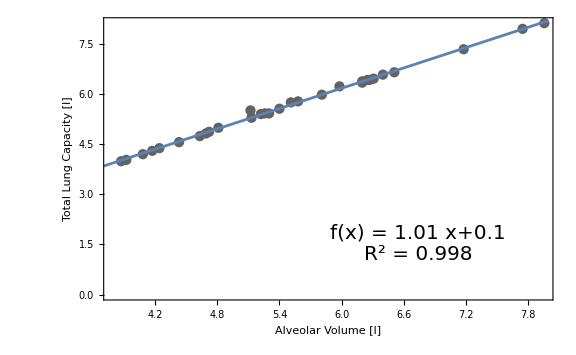

FittedModel[…]

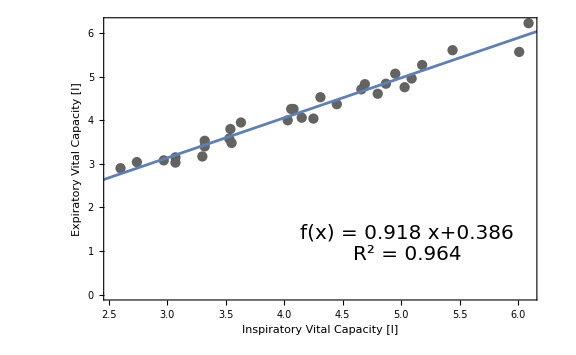

perfect correlation between respiratory parameters

```mathematica
lm=LinearModelFit[dincl[[All,-1]][[All,2]][[All,{10,18}]],x,x]
correlationTlcAv=Show[ListPlot[dincl[[All,-1]][[All,2]][[All,{10,18}]],FrameLabel->{"Alveolar Volume [l]","Total Lung Capacity [l]"},PlotStyle->myBAUAColors[][[-4]],Frame->True,myFrameStyle[],myFrameTickStyle[],ImageSize->Large],Plot[lm[x],{x,0,8}],Epilog->{Inset[Style[Column[{Row[ {"f(x) = ",If[NumberQ[#],Round[#,.01],#]&//@Normal[lm]}],Row[{"R^2 = ",Round[lm["RSquared"],.001]}]},Center],20,FontFamily->myFontStandard],Scaled[{.7,.2}]]}]

lm=LinearModelFit[dincl[[All,-1]][[All,2]][[All,{21,22}]],x,x]
correlationIvcEvc=Show[ListPlot[dincl[[All,-1]][[All,2]][[All,{21,22}]],FrameLabel->{"Inspiratory Vital Capacity [l]","Expiratory Vital Capacity [l]"},PlotStyle->myBAUAColors[][[-4]],Frame->True,myFrameStyle[],myFrameTickStyle[],ImageSize->Large],Plot[lm[x],{x,0,8}],Epilog->{Inset[Style[Column[{Row[ {"f(x) = ",If[NumberQ[#],Round[#,.001],#]&//@Normal[lm]}],Row[{"R^2 = ",Round[lm["RSquared"],.001]}]},Center],20,FontFamily->myFontStandard],Scaled[{.7,.2}]]}]
myStyle["perfect correlation between respiratory parameters"]
```

```mathematica
myExportF[{{correlationIvcEvc,"009","correlation plot inspiratory vital capacity to expiratory vital capacity",600,False},{correlationTlcAv,"010","correlation plot total lung capacity to alveolar volume",600,False}}]
```

#### due to perfect correlation of respiratory data, expiratory and inspiratory vital capacity can be seen as equal and TLC and alveolar volume too. Thus only one of them can be depicted to represent the other’s result too.

#### Fit for inspiratory volume per total lung capacity

```mathematica
(* overallDataFitVperTLC=Get[NotebookDirectory[]<>"overall data fit result with x and y errors with V per TLC in percent.wl"] *)
overallDataFitVperTLC=FittedModel[…];
```

### Attention: long computation process!

```mathematica
tinspValues={3,2,1,.5};
tinspDataXYErrorsVTLC=Join@@MapThread[Transpose[{#1[[All,1]],ConstantArray[#2,Length[#1]],#1[[All,2]]}]&,{plotAndDataParticlesperRespDataSubInspDur[[1,2]],tinspValues}]
```

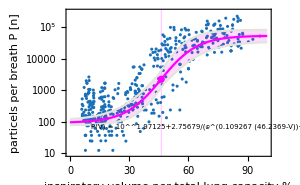
```mathematica
(*If[ChoiceDialog[TextCell["Soll der Datenfit gestartet werden?\n\nDies ist ein rechenintensiver Prozess!"],WindowTitle->"Lange Berechnung starten?"]===True

,*)Print[AbsoluteTiming[overallDataVTLC=NonlinearModelFit[tinspDataXYErrorsVTLC,{10^(b+(L-b)/(1+ⅇ^((-Vinsp+A(1-Exp[-tinsp/τ]))/k))),1.5<b<3.0,4.0<L,6.0<k<25,30<A<60,0.1<τ<2},{{L,4.75},{k,10.},{b,2.2},{A,40},{τ,0.4}},{Vinsp,tinsp}]]]; (*-Graphics-A from manual fit, see DAtenauswertung 21.08.2024 23-35-34, ebenda für k -Graphics-; b und L sind als y-Werte unberührt*)
Print@overallDataVTLC;
Print@overallDataVTLC["ParameterEstimates"];

Save[exPath<>"overall data fit result with x and y errors with V per TLC in percent.wl",overallDataVTLC]
(*]*)
```

```mathematica
overallDataFitVperTLC["ParameterEstimates"]
```

FittedModel::constr: The property values {ParameterEstimates} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-2950.35] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
(* excelExportForWord[[1,2]]=excelExportForWord[[1,2]]/. (#->Nothing&/@excelExportForWord[[1,2]][[55;;61]]); *)
```

```mathematica
appendToExcelExportForWord["overall data fit result with x and y errors for V per TLC"];
excelExportForWord[[1,2]]=Join[excelExportForWord[[1,2]],If[NumberQ[#],Round[#,0.001],#]&//@(Flatten/@(Normal/@Normal[overallDataFitVperTLC["ParameterEstimates"]]/. Rule->List))];
appendToExcelExportForWord[{{"r squared of overall fit result with x and y errors  for V per TLC",Round[#,0.001]&@overallDataFitVperTLC["RSquared"],"estimate of the error variance of overall fit result with x and y errors for V per TLC",Round[#,0.001]&@overallDataFitVperTLC["EstimatedVariance"]}}];

Export[exPath~~"parameters' value output for word.xlsx",excelExportForWord]
```

FittedModel::constr: The property values {ParameterEstimates} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-2950.35] is too small to represent as a normalized machine number; precision may be lost.

FittedModel::constr: The property values {EstimatedVariance} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

D:\Daten\b1464\Desktop\Ausgabe\parameters' value output for word.xlsx

10^((1.50.5)+(3.30.5)/(1+ⅇ^((0.0910.017) (-Vinsp+(1-ⅇ^(tinsp (-1.90.4))) (30.5.)))))

10^((1.50.5)+(3.30.5)/(1+ⅇ^((0.0910.017) (-Vinsp+(1-ⅇ^(tinsp (-1.90.4))) (30.5.)))))

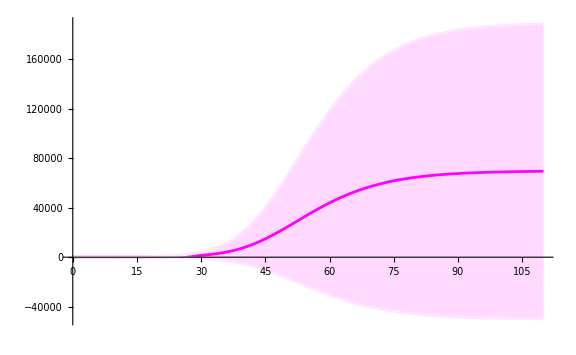
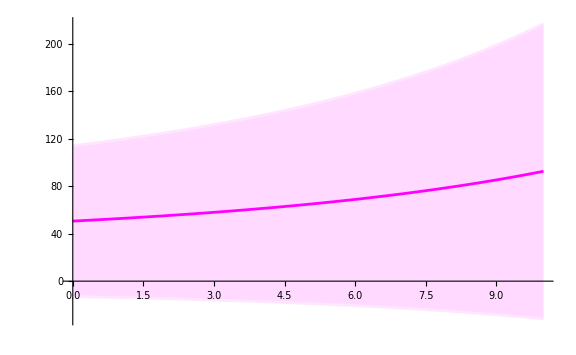
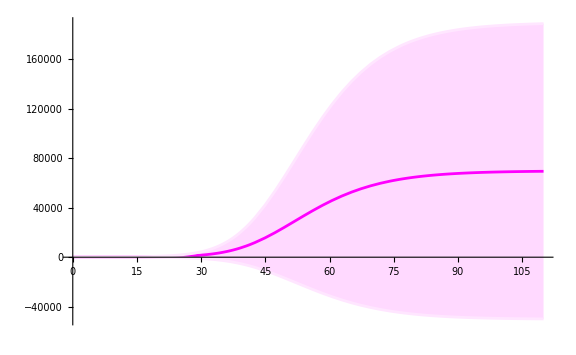
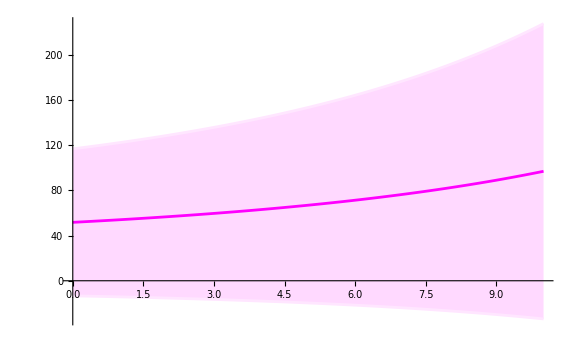
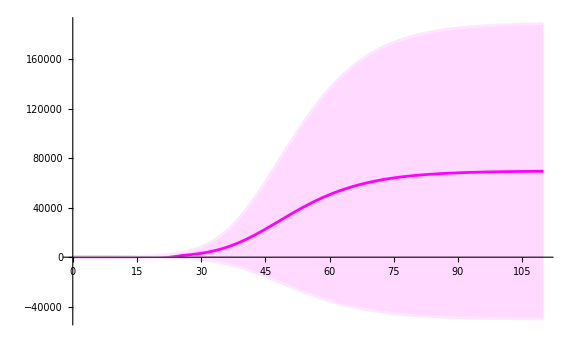
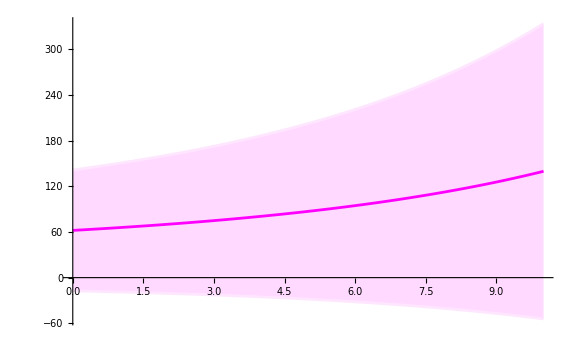
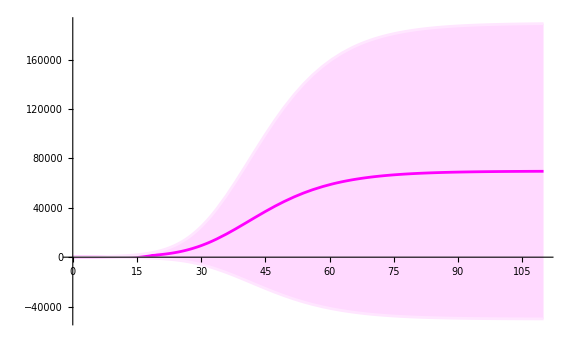
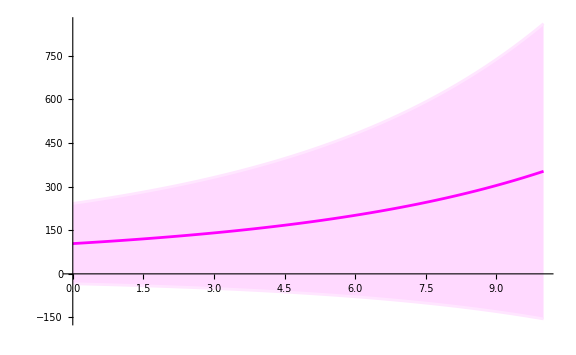

all lower CI bounds are negative

```mathematica
plotParticlesPerVolumeSubInspDurSingleVperTLC=ListPlot[ReplacePart[plotAndDataParticlesperRespDataSubInspDur[[1,2]],#],myPlotStyle[1,myPlotColors[[All,2]]],PlotRange->{{0,110},{1,3*10^5}},PlotLegends->SwatchLegend[myStyle/@plotlegends,LegendMarkerSize->myFontSize,LegendMarkers->"Bubble",LegendLabel->Column[{myStyle[descrInspDur]},Center]],ImageSize->1300,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,None}},myFrameStyle[],myFrameTickStyle[],ScalingFunctions->"Log",FrameLabel->myStyle/@{"Inspiratory Volume StyleBox[\"V\",FontSlant->\"Italic\"] per Total Lung Capacity %",descrPartpB}]&/@Reverse@Map[#->{Null}&,Subsets[{1,2,3,4},{3}],{2}];

masterFormelVperTLC[Vinsp_,tinsp_]=masterFormel@@({A,b,k,L,τ,tinsp,Vinsp}/.MapThread[#1->#2&,{Normal[overallDataFitVperTLC["ParameterEstimates"][All,"Parameter"]],MapThread[Around[#1,#2]&,{Normal[overallDataFitVperTLC["ParameterEstimates"][All,"BestFitValue"]], 2  Normal[overallDataFitVperTLC["ParameterEstimates"][All,"StandardError"]]}]}]) //Quiet
Vinsp=.
tinps=.
myExportEquations[{{Evaluate@masterFormelVperTLC[Vinsp,tinsp],"overall data fit equation with errors for V per TLC"}}];


Table[Table[Plot[{(masterFormelVperTLC[Vinsp,myPlotColors[[All,1]][[i]]])["Value"],List@@(masterFormelVperTLC[Vinsp,myPlotColors[[All,1]][[i]]])["Interval"]},{Vinsp,0,j},Filling->{1->{{2},Directive[Opacity[0.15],Magenta]}},PlotStyle->{Magenta,LightMagenta,LightMagenta},ImageSize->Large],{i,4}]
,{j,{110,10}}]ᵀ
myStyle["all lower CI bounds are negative"]
```

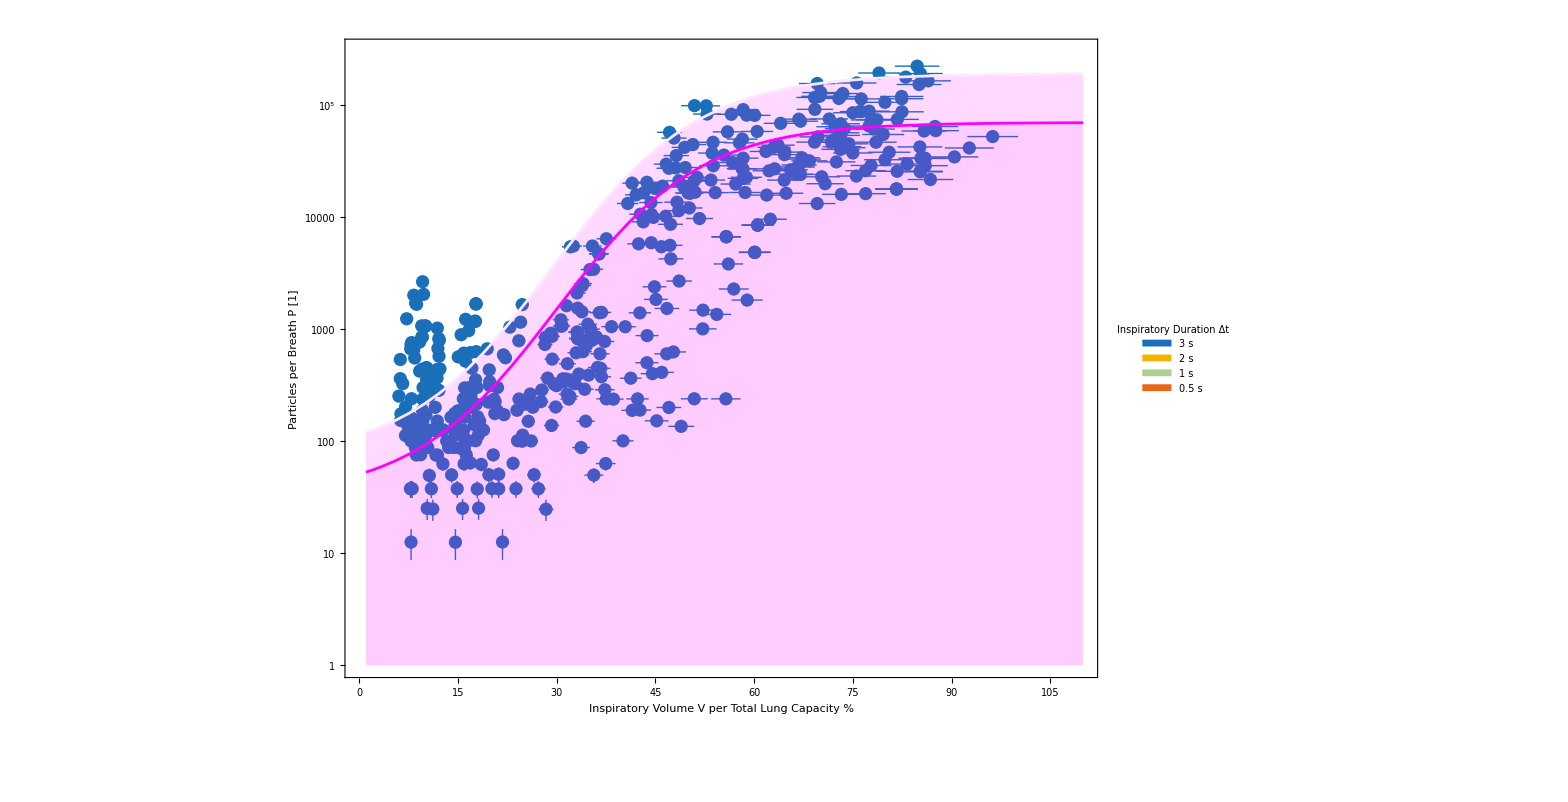
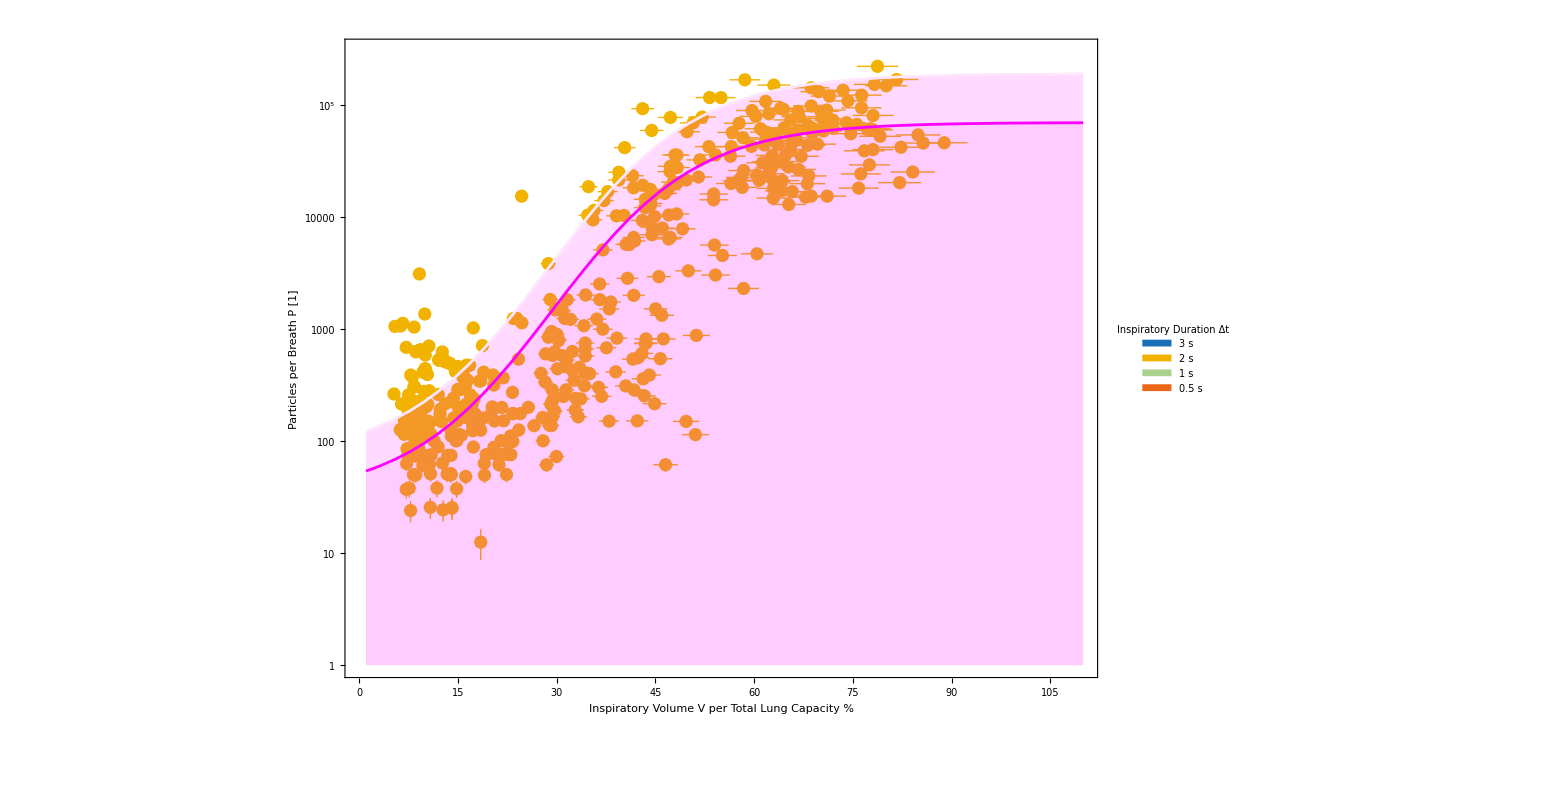
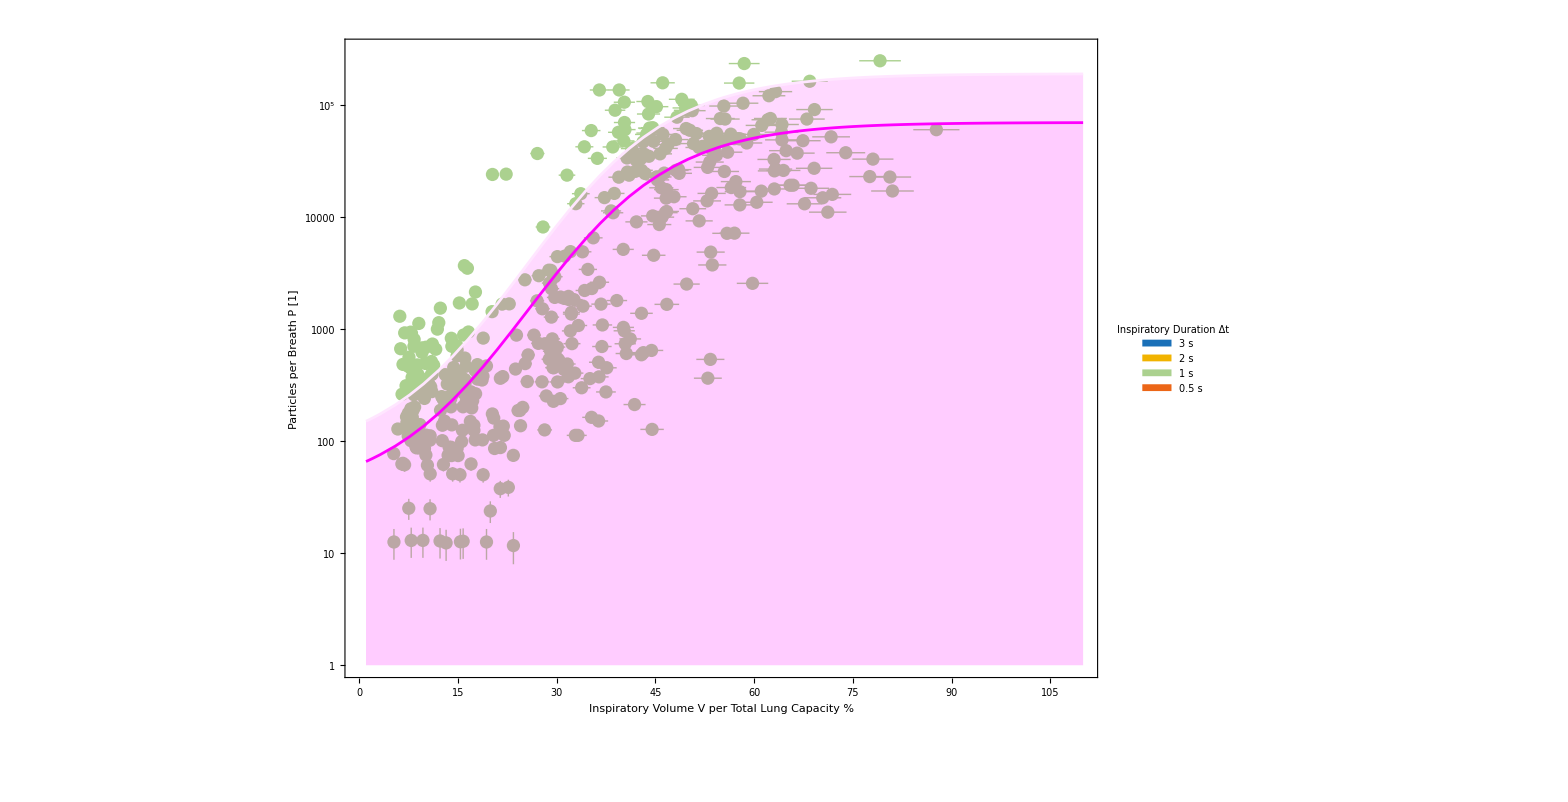
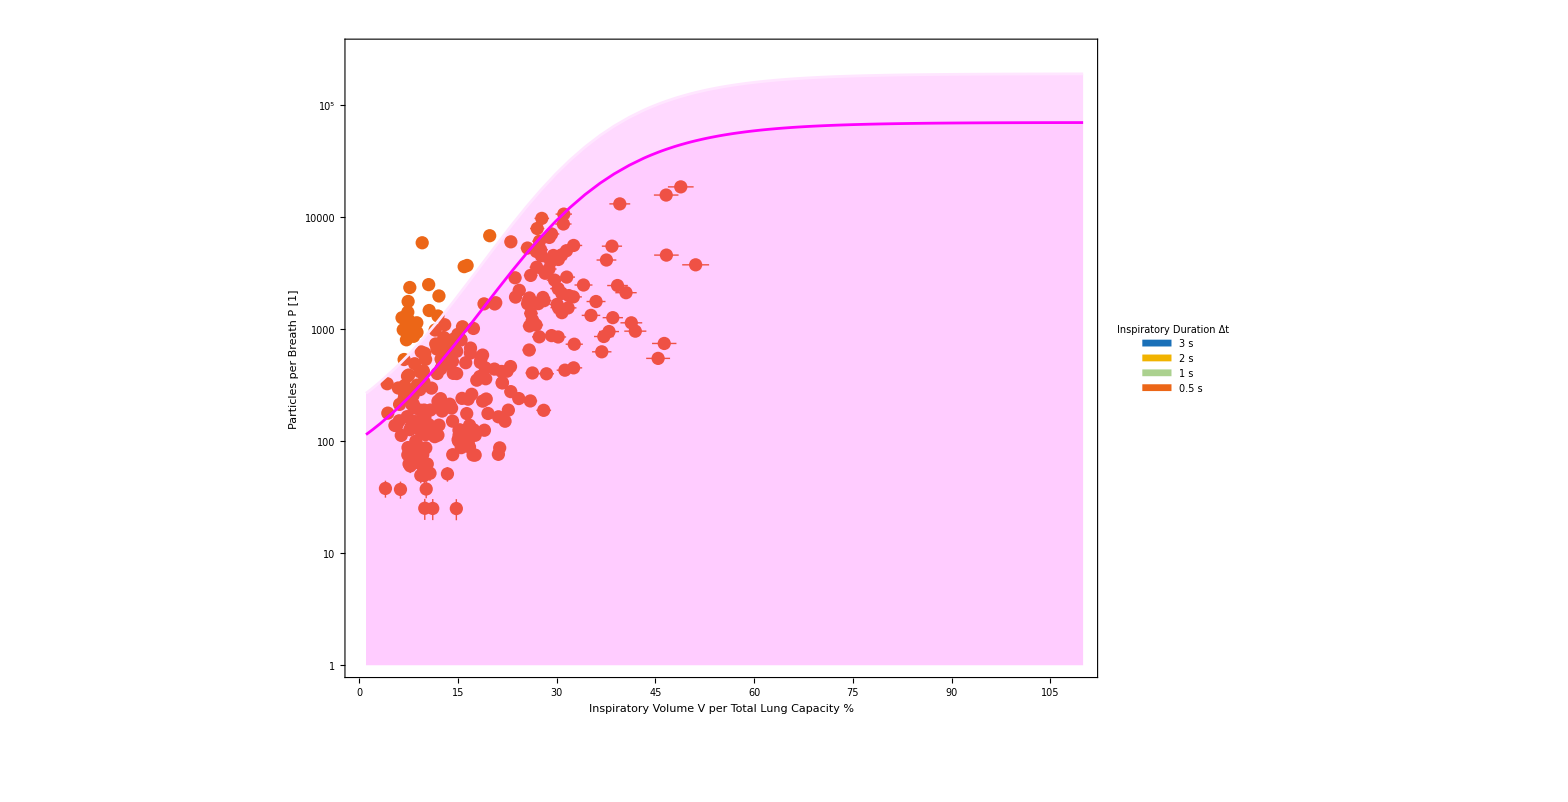

```mathematica
overallFit95CIPlotsVperTLC=Table[Show[plotParticlesPerVolumeSubInspDurSingleVperTLC[[i]],LogPlot[{(masterFormelVperTLC[Vinsp,myPlotColors[[All,1]][[i]]])["Value"],List@@(masterFormelVperTLC[Vinsp,myPlotColors[[All,1]][[i]]])["Interval"]},{Vinsp,1,110},Filling->{1->{{2},Directive[Opacity[0.15],Magenta]},1->1,Directive[Opacity[0.15],Magenta]},PlotStyle->{Magenta,LightMagenta,LightMagenta}]],{i,4}]
```

```mathematica
overallFit95CIPlotsInGridVperTLC=Grid[{overallFit95CIPlotsVperTLC[[1;;2]],overallFit95CIPlotsVperTLC[[3;;4]]},Spacings->{2,2}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
myExportF[{{overallFit95CIPlotsInGridVperTLC,"048","overall data fit plots with 95-CI in grid for inspiratory durations and V per TLC",300,False}}]
```

#### Fit for inspiratory volume per inspiratory capacity

```mathematica
(* overallDataFitVperIC=Get[NotebookDirectory[]<>"overall data fit result with x and y errors with V per IC in percent.wl"] *)
overallDataFitVperIC=FittedModel[…]
```

FittedModel[…]

```mathematica
tinspValues={3,2,1,.5};
tinspDataXYErrorsVIC=Join@@MapThread[Transpose[{#1[[All,1]],ConstantArray[#2,Length[#1]],#1[[All,2]]}]&,{plotAndDataParticlesperRespDataSubInspDur[[3,2]],tinspValues}]

(*If[ChoiceDialog[TextCell["Soll der Datenfit gestartet werden?\n\nDies ist ein rechenintensiver Prozess!"],WindowTitle->"Lange Berechnung starten?"]===True

,*)Print[AbsoluteTiming[overallDataVIC=NonlinearModelFit[tinspDataXYErrorsVIC,{10^(b+(L-b)/(1+ⅇ^((-Vinsp+A(1-Exp[-tinsp/τ]))/k))),1.5<b<3.0,4.0<L,6.0<k<25,30<A<60,0.1<τ<2},{{L,4.75},{k,10.},{b,2.2},{A,40},{τ,0.4}},{Vinsp,tinsp}]]]; 
Print@overallDataVIC;
Print@overallDataVIC["ParameterEstimates"];

Save[exPath<>"overall data fit result with x and y errors with V per IC in percent.wl",overallDataVIC]
(*]*)
```

```mathematica
appendToExcelExportForWord["overall data fit result with x and y errors for V per TLC"];
excelExportForWord[[1,2]]=Join[excelExportForWord[[1,2]],If[NumberQ[#],Round[#,0.001],#]&//@(Flatten/@(Normal/@Normal[overallDataFitVperIC["ParameterEstimates"]]/. Rule->List))];
appendToExcelExportForWord[{{"r squared of overall fit result with x and y errors",Round[#,0.001]&@overallDataFitVperIC["RSquared"],"estimate of the error variance of overall fit result with x and y errors for V per TLC",Round[#,0.001]&@overallDataFitVperIC["EstimatedVariance"]}}];

Export[exPath~~"parameters' value output for word.xlsx",excelExportForWord]
```

FittedModel::constr: The property values {ParameterEstimates} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-3217.45] is too small to represent as a normalized machine number; precision may be lost.

FittedModel::constr: The property values {EstimatedVariance} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

D:\Daten\b1464\Desktop\Ausgabe\parameters' value output for word.xlsx

```mathematica
overallDataFitVperIC["ParameterEstimates"]
```

FittedModel::constr: The property values {ParameterEstimates} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-3217.45] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
(* excelExportForWord[[1,2]]=excelExportForWord[[1,2]]/. (#->Nothing&/@excelExportForWord[[1,2]][[39;;67]]) *)
```

```mathematica
appendToExcelExportForWord["overall data fit result with x and y errors for V per IC"];
excelExportForWord[[1,2]]=Join[excelExportForWord[[1,2]],If[NumberQ[#],Round[#,0.001],#]&//@(Flatten/@(Normal/@Normal[overallDataFitVperIC["ParameterEstimates"]]/. Rule->List))];
appendToExcelExportForWord[{{"r squared of overall fit result with x and y errors for V per IC",Round[#,0.001]&@overallDataFitVperIC["RSquared"],"estimate of the error variance of overall fit result with x and y errors for V per IC",Round[#,0.001]&@overallDataFit["EstimatedVariance"]}}];

Export[exPath~~"parameters' value output for word.xlsx",excelExportForWord]
```

FittedModel::constr: The property values {ParameterEstimates} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-3217.45] is too small to represent as a normalized machine number; precision may be lost.

FittedModel::constr: The property values {EstimatedVariance} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

D:\Daten\b1464\Desktop\Ausgabe\parameters' value output for word.xlsx

```mathematica
({overallDataFit[#],overallDataFitVperIC[#],overallDataFitVperTLC[#]}&/@{"EstimatedVariance","ANOVA"})ᵀ
```

FittedModel::constr: The property values {EstimatedVariance} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{{55.9063,},{405.561,},{367.396,}}

10^((1.60.4)+(3.20.5)/(1+ⅇ^((0.0740.014) (-Vinsp+(1-ⅇ^(tinsp (-2.00.5))) (42.7.)))))

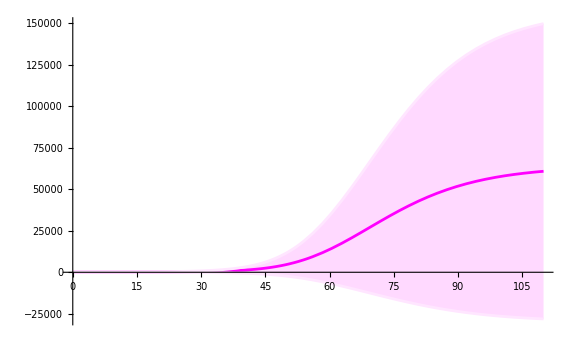
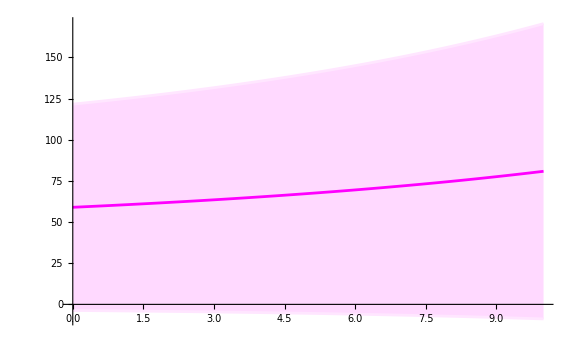
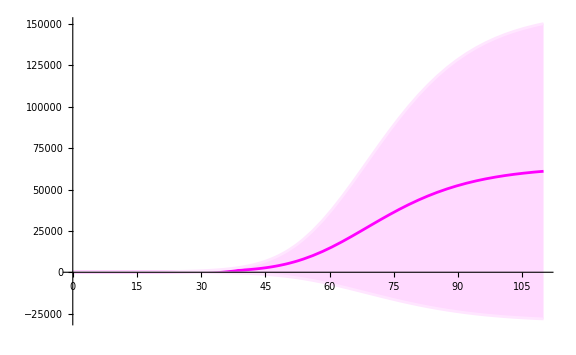
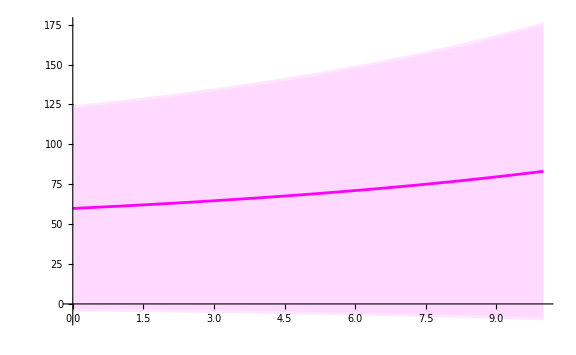
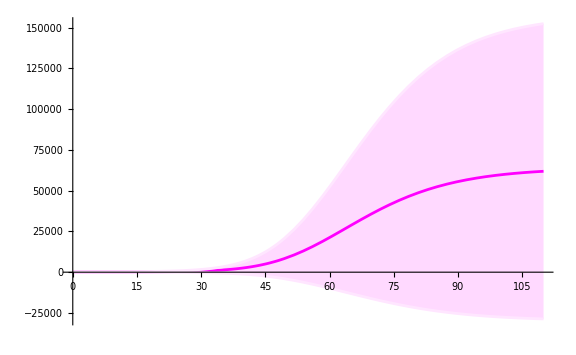
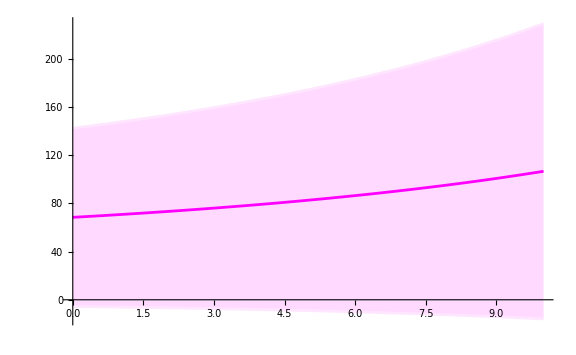
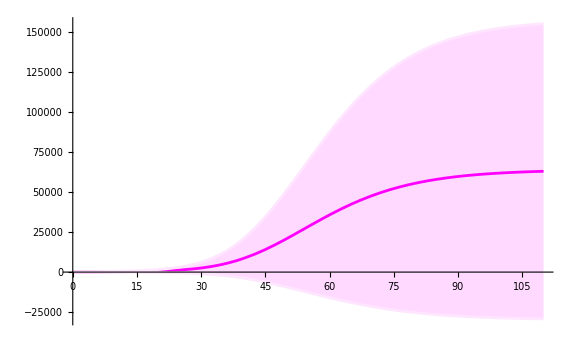
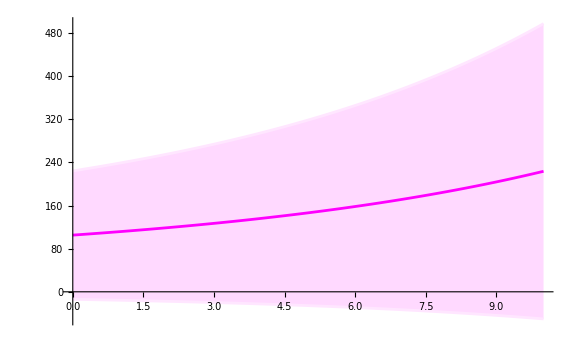

all lower CI bounds are negative

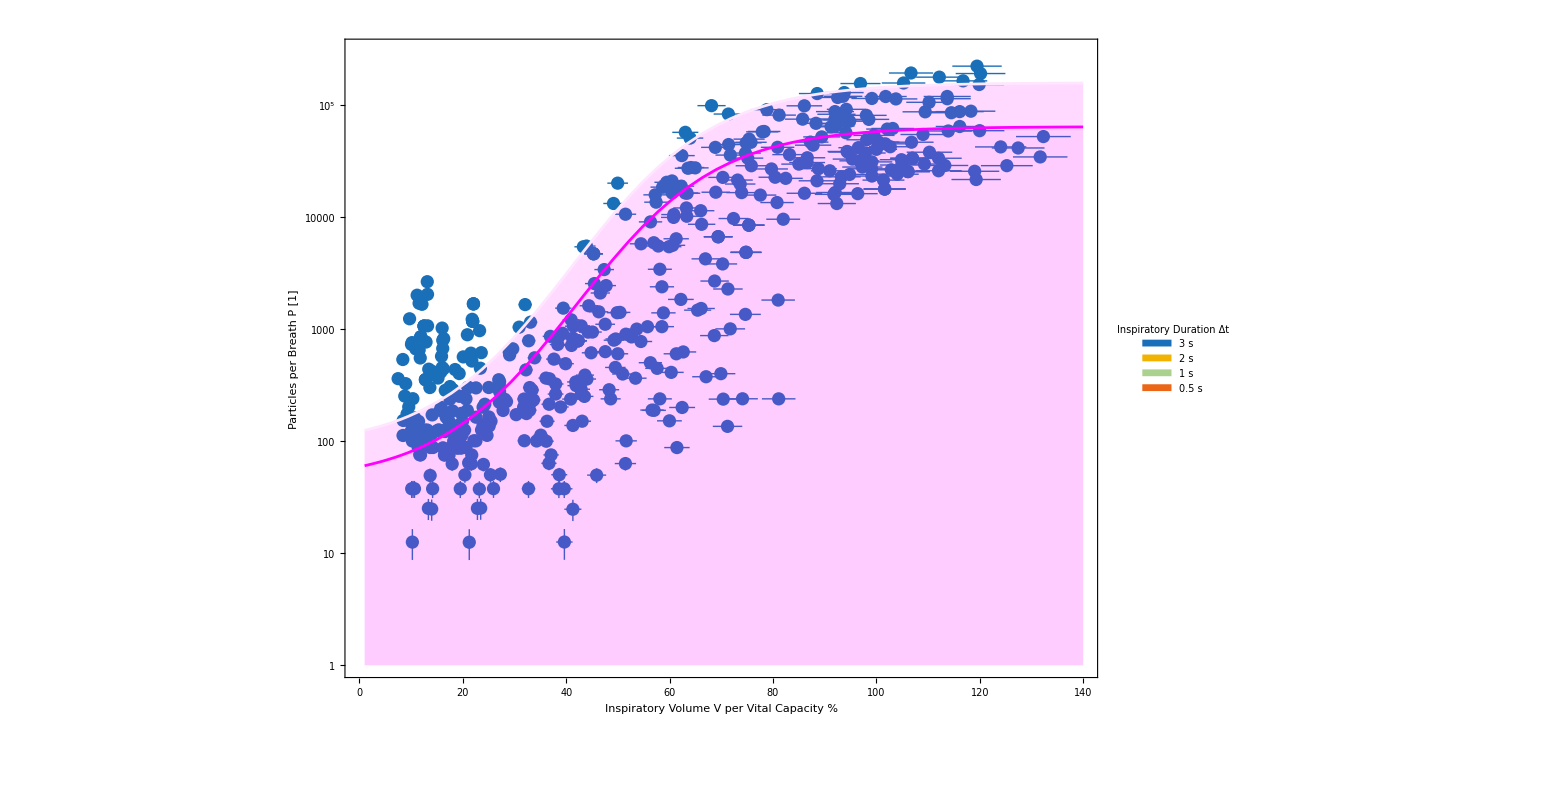
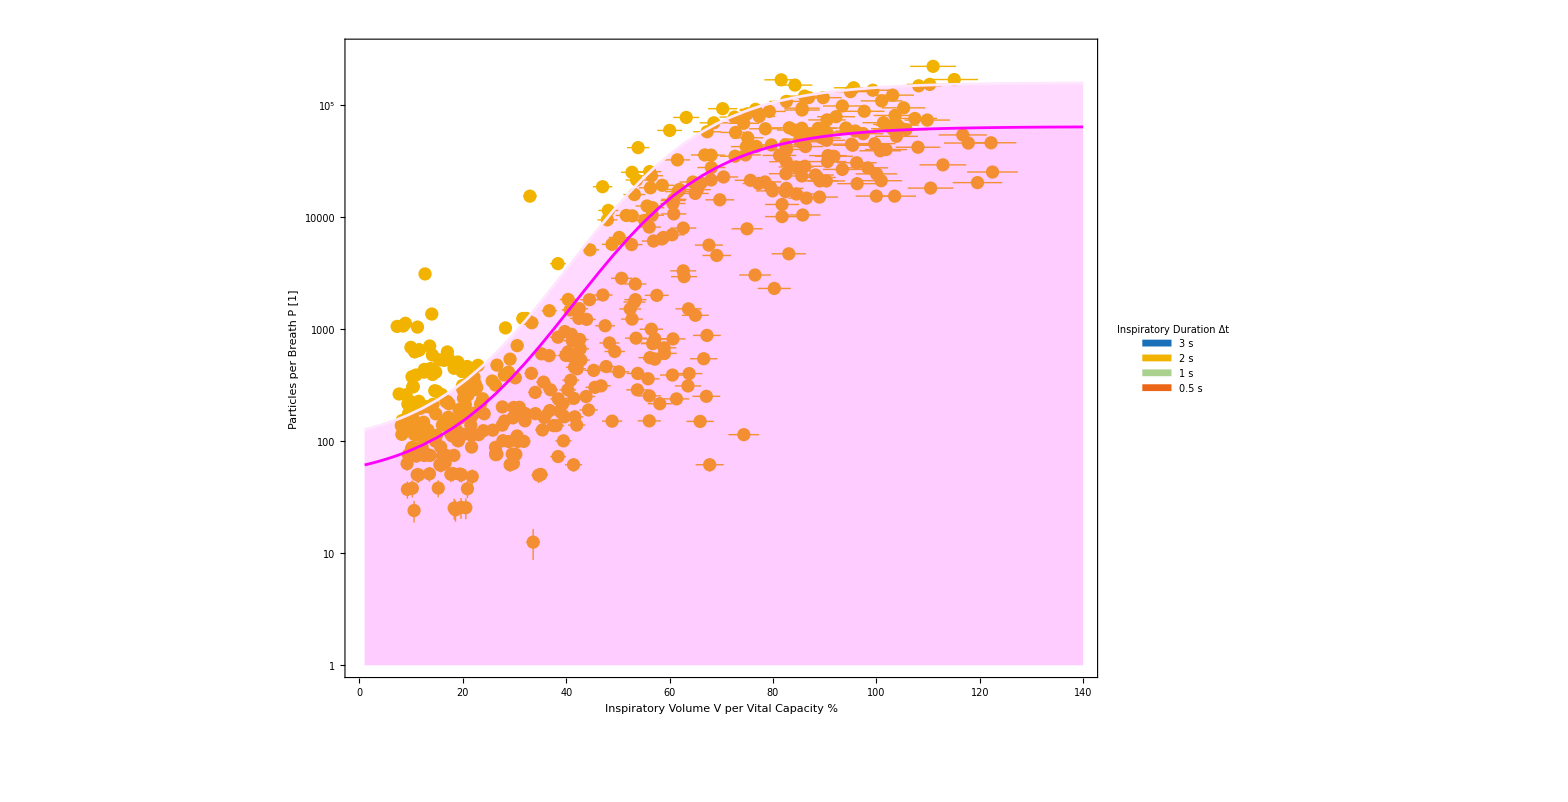
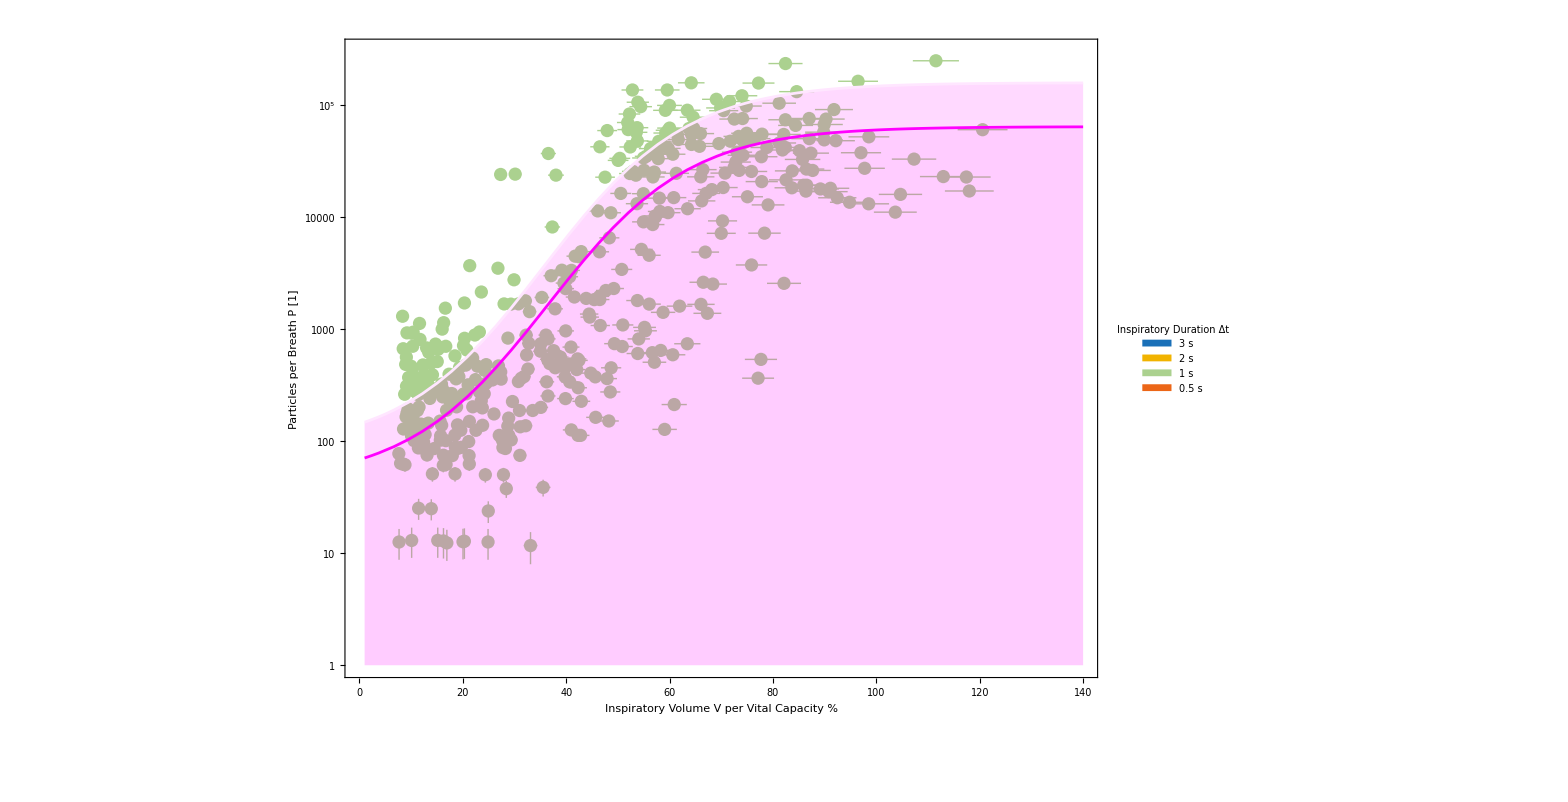
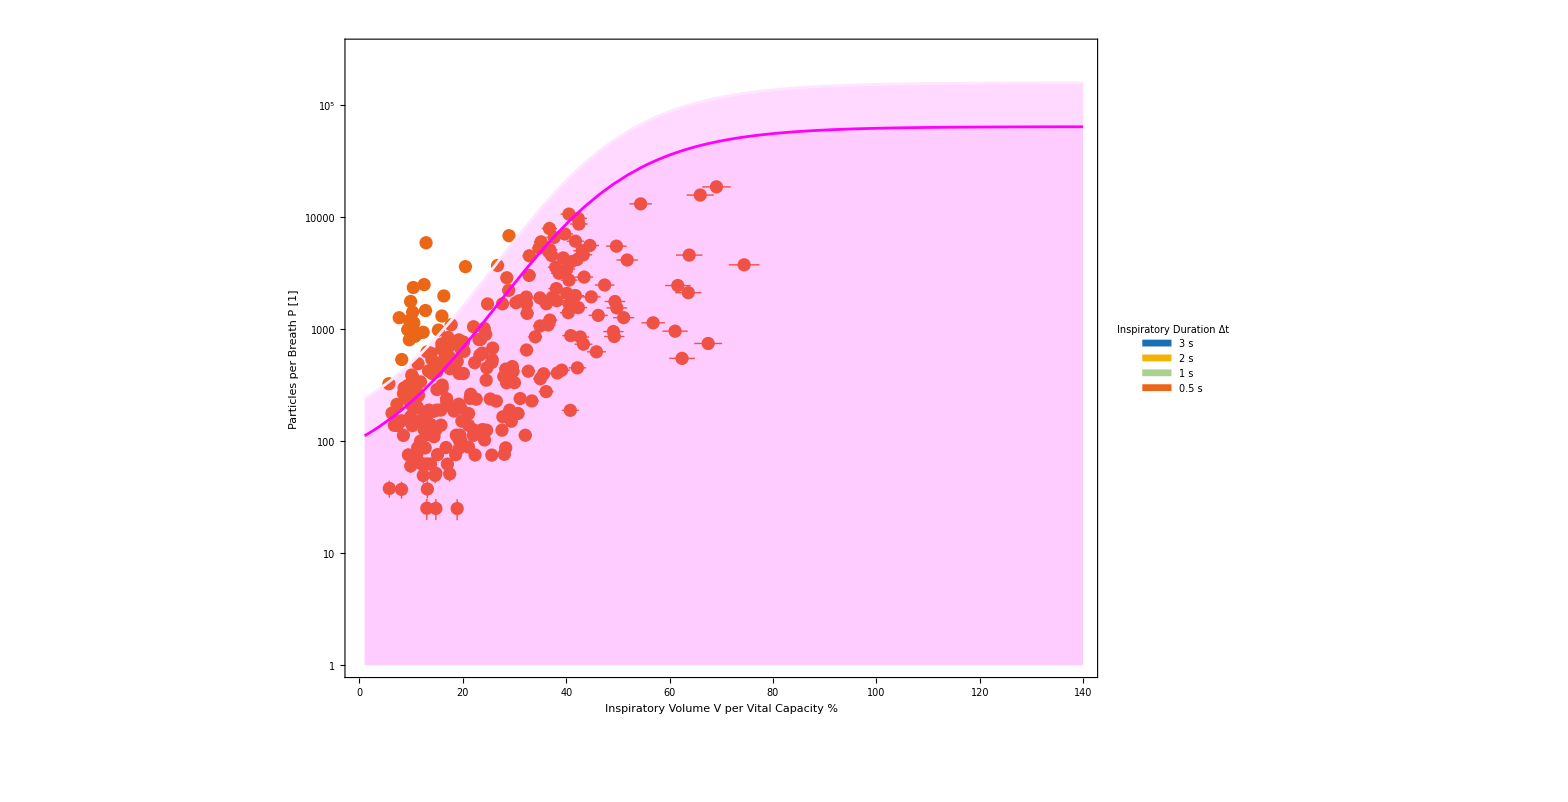
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
plotParticlesPerVolumeSubInspDurSingleVperIC=ListPlot[ReplacePart[plotAndDataParticlesperRespDataSubInspDur[[3,2]],#],myPlotStyle[1,myPlotColors[[All,2]]],PlotRange->{{0,140},{1,3*10^5}},PlotLegends->SwatchLegend[myStyle/@plotlegends,LegendMarkerSize->myFontSize,LegendMarkers->"Bubble",LegendLabel->Column[{myStyle[descrInspDur]},Center]],ImageSize->1300,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,None}},myFrameStyle[],myFrameTickStyle[],ScalingFunctions->"Log",FrameLabel->myStyle/@{"Inspiratory Volume StyleBox[\"V\",FontSlant->\"Italic\"] per Vital Capacity %",descrPartpB}]&/@Reverse@Map[#->{Null}&,Subsets[{1,2,3,4},{3}],{2}];

masterFormelVperIC[Vinsp_,tinsp_]=masterFormel@@({A,b,k,L,τ,tinsp,Vinsp}/.MapThread[#1->#2&,{Normal[overallDataFitVperIC["ParameterEstimates"][All,"Parameter"]],MapThread[Around[#1,#2]&,{Normal[overallDataFitVperIC["ParameterEstimates"][All,"BestFitValue"]], 2  Normal[overallDataFitVperIC["ParameterEstimates"][All,"StandardError"]]}]}]) //Quiet
Vinsp=.
tinps=.
myExportEquations[{{Evaluate@masterFormelVperIC[Vinsp,tinsp],"overall data fit equation with errors for V per IC"}}];

Table[Table[Plot[{(masterFormelVperIC[Vinsp,myPlotColors[[All,1]][[i]]])["Value"],List@@(masterFormelVperIC[Vinsp,myPlotColors[[All,1]][[i]]])["Interval"]},{Vinsp,0,j},Filling->{1->{{2},Directive[Opacity[0.15],Magenta]}},PlotStyle->{Magenta,LightMagenta,LightMagenta},ImageSize->Large],{i,4}]
,{j,{110,10}}]ᵀ
myStyle["all lower CI bounds are negative"]


overallFit95CIPlotsVperIC=Table[Show[plotParticlesPerVolumeSubInspDurSingleVperIC[[i]],LogPlot[{(masterFormelVperIC[Vinsp,myPlotColors[[All,1]][[i]]])["Value"],List@@(masterFormelVperIC[Vinsp,myPlotColors[[All,1]][[i]]])["Interval"]},{Vinsp,1,140},Filling->{1->{{2},Directive[Opacity[0.15],Magenta]},1->1,Directive[Opacity[0.15],Magenta]},PlotStyle->{Magenta,LightMagenta,LightMagenta}]],{i,4}];

overallFit95CIPlotsInGridVperIC=Grid[{overallFit95CIPlotsVperIC[[1;;2]],overallFit95CIPlotsVperIC[[3;;4]]},Spacings->{2,2}]
```

```mathematica
myExportF[{{overallFit95CIPlotsInGridVperIC,"060","overall data fit plots with 95-CI in grid for inspiratory durations and V per VC",300,False}}]
```

## Statistics

### for breathing volumes

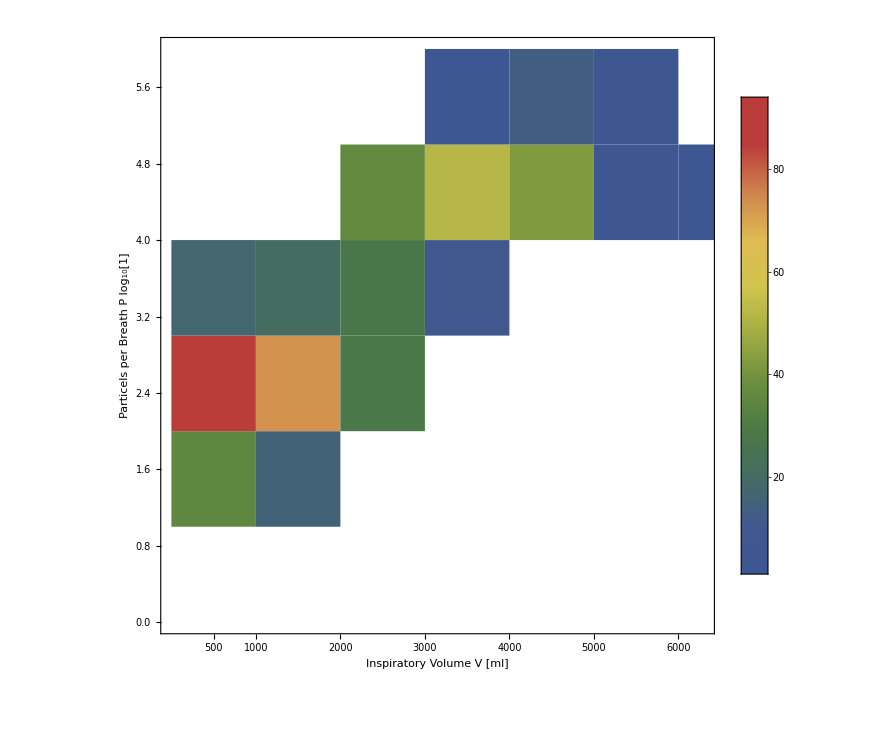
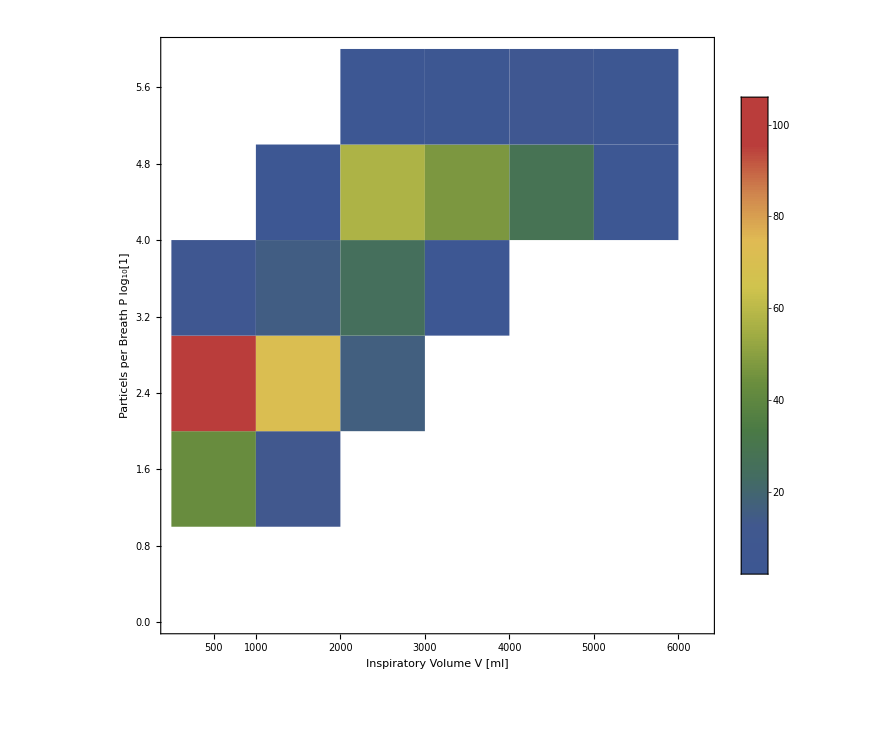
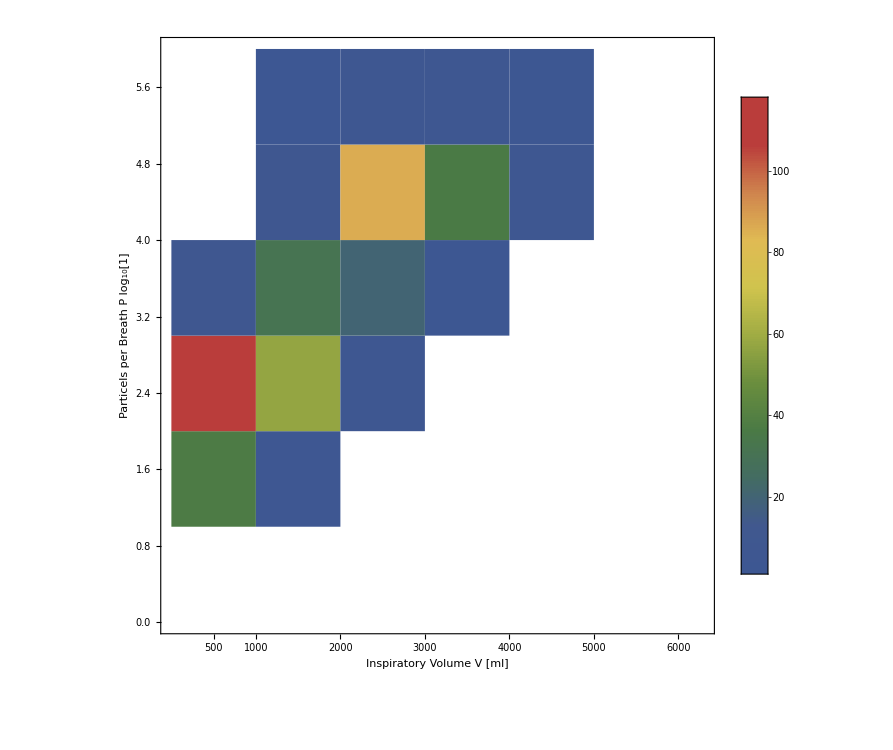
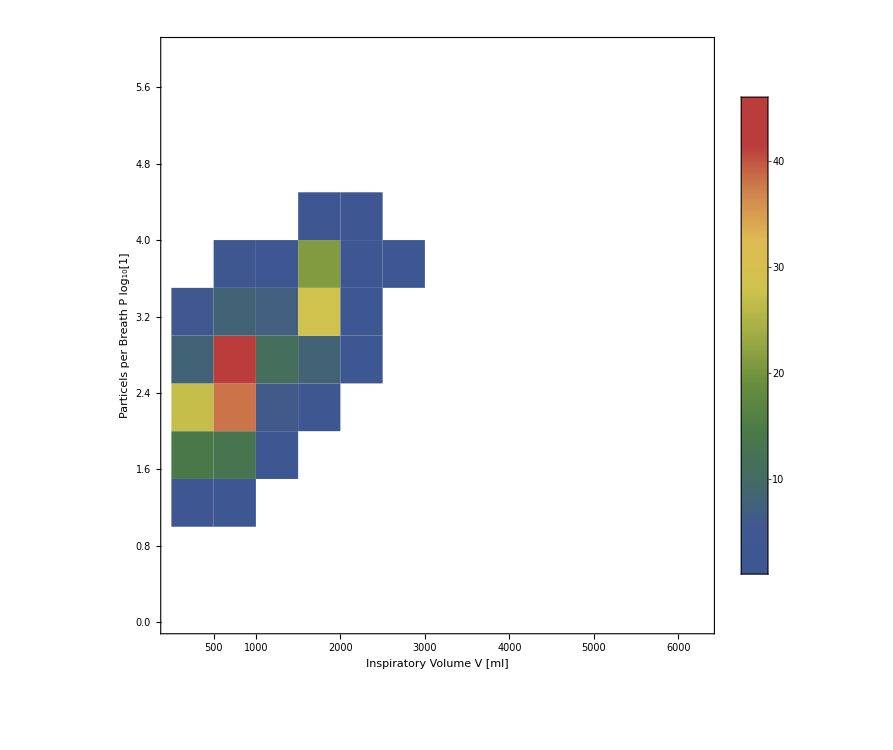
{-Graphics-Inspiratory Duration 3 s,-Graphics-Inspiratory Duration 2 s,-Graphics-Inspiratory Duration 1 s,-Graphics-Inspiratory Duration 0.5 s}

```mathematica
densityPlotsVolumeKat=Labeled[DensityHistogram[Map[{#[[1]],Log10[#[[2]]]}&,#[[1]]],5,FrameTicks->{Automatic,{{500,1000,2000,3000,4000,5000,6000},Automatic}},FrameLabel->myStyle/@{descrInspV,"Particels per Breath P log_10[1]"},ImageSize->750,myFrameStyle[],ChartLegends->Automatic,myFrameTickStyle[],myLabelStyle[],ColorFunction->Function[{height},myColorForGradient[height]],PlotRange->{{0,6300},{0,Log10[ 10^6]},All}],myStyle[#[[2]],Bold],Top]&/@Transpose[{plotDataParV,{"Inspiratory Duration 3 s","Inspiratory Duration 2 s","Inspiratory Duration 1 s","Inspiratory Duration 0.5 s"}}]
densityPlotsVolumeKatSet=Grid[{myTake[densityPlotsVolumeKat,{1;;2}],myTake[densityPlotsVolumeKat,{3;;4}]},Spacings->{1,4}];
```

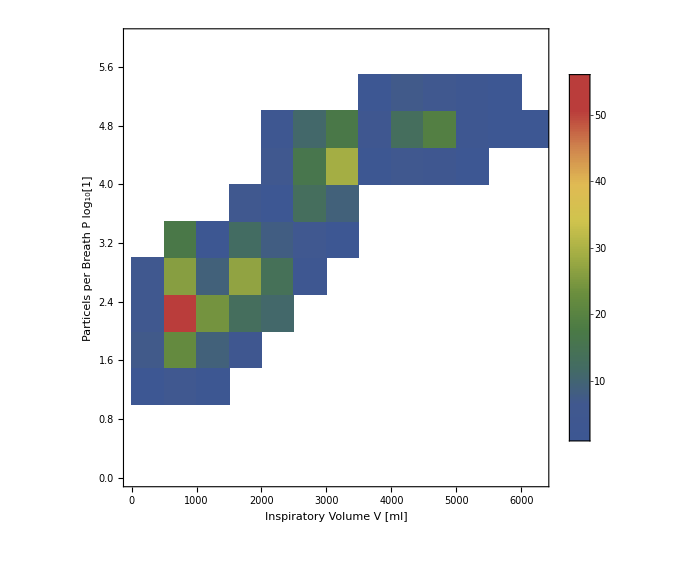
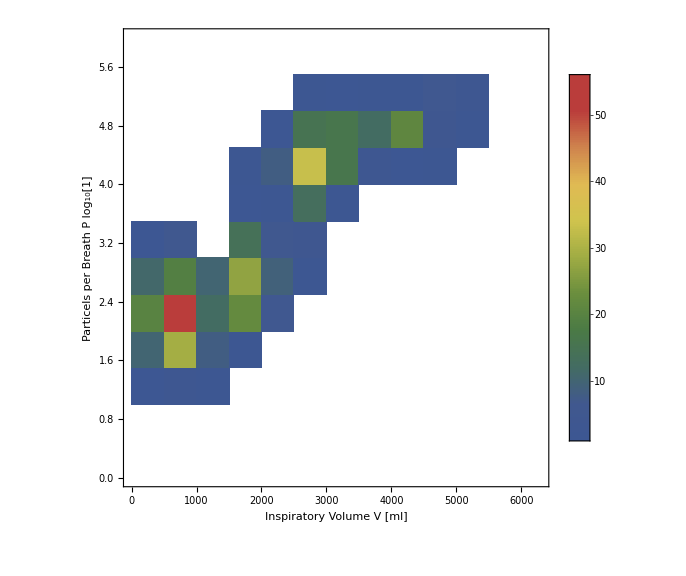
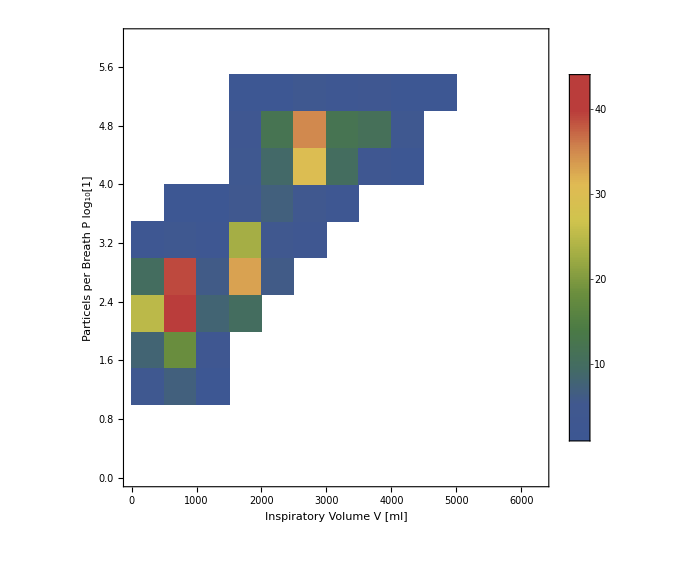
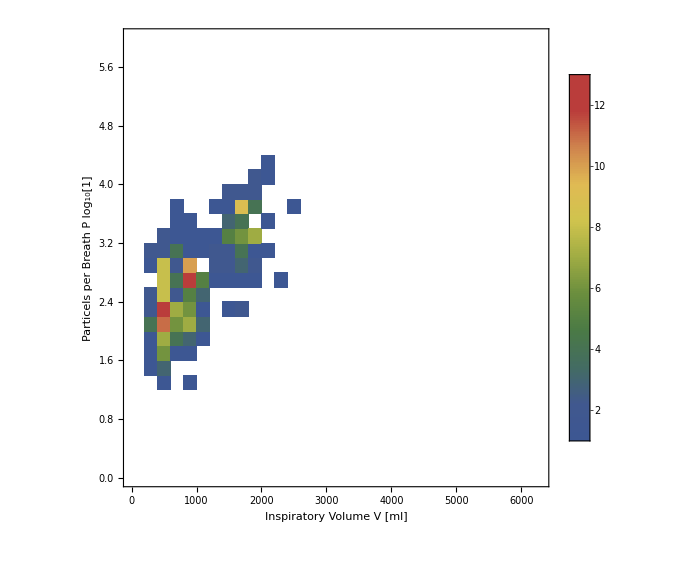
{-Graphics-Inspiratory Duration 3 s,-Graphics-Inspiratory Duration 2 s,-Graphics-Inspiratory Duration 1 s,-Graphics-Inspiratory Duration 0.5 s}

```mathematica
densityPlotsVolume=Labeled[DensityHistogram[Map[{#[[1]],Log10[#[[2]]]}&,#[[1]]],FrameLabel->myStyle/@{descrInspV,"Particels per Breath P log_10[1]"},ImageSize->Large,myFrameStyle[],ChartLegends->Automatic,myFrameTickStyle[],myLabelStyle[],ColorFunction->Function[{height},myColorForGradient[height]],PlotRange->{{0,6300},{0,Log10[ 10^6]},All}],myStyle[#[[2]],Bold],Top]&/@Transpose[{plotDataParV,{"Inspiratory Duration 3 s","Inspiratory Duration 2 s","Inspiratory Duration 1 s","Inspiratory Duration 0.5 s"}}]

densityPlotsVolumeSet=Grid[{myTake[densityPlotsVolume,{1;;2}],myTake[densityPlotsVolume,{3;;4}]},Spacings->{1,4}];
```

```mathematica
myExportF[{{densityPlotsVolumeKatSet,"007","density histogram particles per categorial volume with subgroup inspiratory duration",600,False},{densityPlotsVolumeSet,"008","density histogram particles per volume with subgroup inspiratory duration",600,False}}]
```

Export::noopen: Cannot open D:\Daten\b1464\Desktop\Ausgabe\##1 full names of figure IDs.pdf.

```mathematica
(*Bonferroni correction Subscript[α,lokal]=Subscript[α,global]/k where k is all test*)
        (*inspiratory duration comparison                               volume comparisons*)
k=5+Length[Subsets[Range[4],{2}]]*2+Length[Subsets[Range[3],{2}]]+4+Length[Subsets[Range[5],{2}]]*4+Length[Subsets[Range[3],{2}]]
(*5x Kruskal-Wallis for inspiratory duration comparison 5+
4x Kruskal-Wallis for volume comparison 4+

since only 3 of 5  Kruskal-Wallis-test were significant (not 500 ml and max volume) for inspiratory duration comparison 2*time subsets plus 1* 3000ml-subset were calculated

since all Kruskal-Wallis-test were significant for volume, 4x volume subsets plus 1x max volume subsets were calculated
*)
alocal=.05/k
```

67

0.000746269

Kolmogorov Smirnov Test for raw data

| Statistic | P-Value
Kolmogorov-Smirnov | 0.23565 | 0. |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.250091 | 0. |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.225263 | 0. |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.137087 | 0.000485356 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.13538 | 0.000358192
 | Statistic | P-Value
Kolmogorov-Smirnov | 0.255174 | 0. |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.177435 | 0. |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.340915 | 0. |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.164171 | 2.9813×10^-6 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.13615 | 0.000398782
 | Statistic | P-Value
Kolmogorov-Smirnov | 0.169291 | 0. |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.270455 | 0. |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.276764 | 0. |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.166212 | 7.40888×10^-6 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.154902 | 0.0000561852
 | Statistic | P-Value
Kolmogorov-Smirnov | 0.250675 | 0. |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.239053 | 0. |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.176609 | 0. |  |

Kolmogorov Smirnov Test for log10 transformed data

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0892296 | 0.0790357 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0712844 | 0.302485 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0718344 | 0.299178 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.143728 | 0.000186836 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0529975 | 0.785446
 | Statistic | P-Value
Kolmogorov-Smirnov | 0.0702066 | 0.324843 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0579484 | 0.647206 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0632195 | 0.502934 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.126846 | 0.00182257 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0808846 | 0.170468
 | Statistic | P-Value
Kolmogorov-Smirnov | 0.0919945 | 0.0583746 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0695438 | 0.347346 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0889228 | 0.0777476 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.101698 | 0.0419265 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.061489 | 0.643877
 | Statistic | P-Value
Kolmogorov-Smirnov | 0.0554868 | 0.722043 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0661803 | 0.408866 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0584214 | 0.731124 |  |

none of the data has normal distribution %%, but log10-transformed data has mostly %

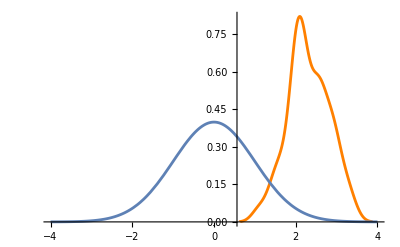
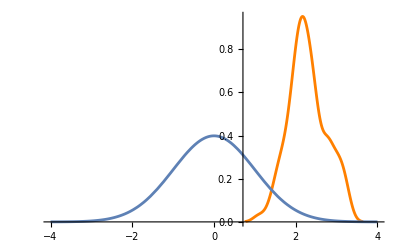
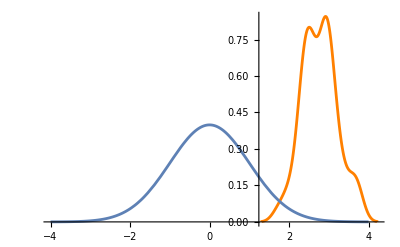
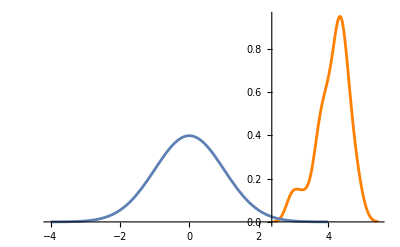
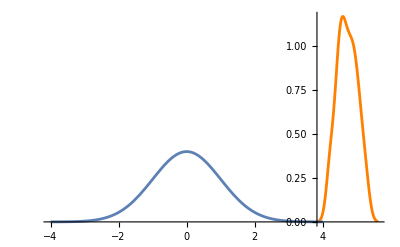
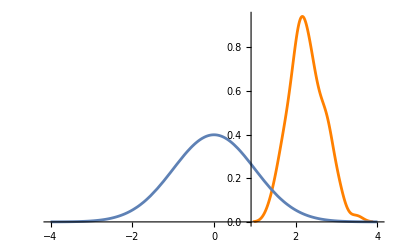
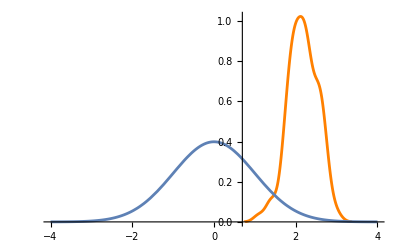
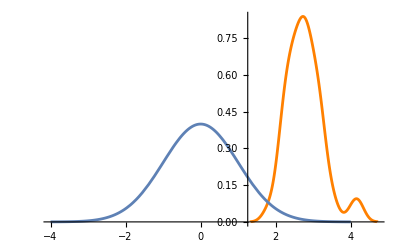

LeveneTest::nortst: At least one of the p-values in {0.160201,0.138457,0.280096,0.00279785,0.420032}, resulting from a test for normality, is below 0.01. The tests in {Levene} require that the data is normally distributed.

LeveneTest::nortst: At least one of the p-values in {0.462005,0.650636,0.167443,0.00241821,0.245547}, resulting from a test for normality, is below 0.01. The tests in {Levene} require that the data is normally distributed.

{0.000206216,0.00193333,0.000581529,0.650155}

except for 0.5 s, there is no homoscedasticity

```mathematica
temp=Values[Map[Flatten[#[[All,All,2,1]]]&,GroupBy[GatherBy[#,First],#[[1,1]]&]]]&/@plotDataParVKat;

myStyle["Kolmogorov Smirnov Test for raw data",myBAUAColors[1][[1]]]
Clear[μ,σ]
TableForm[KolmogorovSmirnovTest[Union[#],NormalDistribution[μ,σ],"TestDataTable"]&/@#&/@temp]

myStyle["Kolmogorov Smirnov Test for log10 transformed data",myBAUAColors[1][[1]]]
TableForm[KolmogorovSmirnovTest[Union[Log10@#],NormalDistribution[μ,σ],"TestDataTable"]&/@#&/@temp]
myStyle["none of the data has normal distribution %%, but log10-transformed data has mostly %",myBAUAColors[1][[1]]]
Show[SmoothHistogram[#,PlotStyle->Orange],Plot[PDF[NormalDistribution[],x],{x,-4,4}]]&/@#&/@Log10/@temp


LeveneTest[#]&/@Log10/@temp
myStyle["except for 0.5 s, there is no homoscedasticity",myBAUAColors[1][[1]]]
```

```mathematica
LocationEquivalenceTest[#,{"TestDataTable",All},SignificanceLevel->alocal]&/@temp
myStyle["in all volume bins per inspiratory duration group are highly significant comparisons",myBAUAColors[1][[1]]];

umwStatV={Function[{lData,lParts},{#,{Median[#],Length[#]}&/@lData[[{#[[1]],#[[2]]}]],MannWhitneyTest[lData[[{#[[1]],#[[2]]}]],0,{"TestData"},SignificanceLevel->alocal]}&/@lParts][#[[1]],#[[2]]]&/@myTranspose[temp[[1;;-2]],Subsets[Range[5],{2}]],Function[{lData,lParts},{#,{Median[#],Length[#]}&/@lData[[{#[[1]],#[[2]]}]],MannWhitneyTest[lData[[{#[[1]],#[[2]]}]],0,{"TestData"},SignificanceLevel->alocal]}&/@lParts][#[[1]],#[[2]]]&/@myTranspose[{temp[[-1]]},Subsets[Range[3],{2}]]};
umwStatV=Catenate[umwStatV];
umwStatV=Map[{{#[[1,1]]->#[[2,1]],#[[1,2]]->#[[2,2]]},Flatten@#[[3]]}&,umwStatV,{2}];
umwStatV=Map[Select[#,#[[2,2]]<.05&]&,umwStatV,{1}];

numberVolumeReplList={1->"500 ml",2->"1000 ml",3->"2000 ml",4->"3000 ml",5->"maximum"};

umwStatVReporting=Map[{"median for breathing volume "~~#[[1,1,1]]~~": "~~ToString[Round[#[[1,1,2,1]],.01]],"median for breathing volume "~~#[[1,2,1]]~~": "~~ToString[Round[#[[1,2,2,1]],.01]],"StyleBox[\"U\",FontSlant->\"Italic\"](StyleBox[StyleBox[\"nsub\",FontSlant->\"Italic\"]]["~~ToString@#[[1,1,1]]~~"]"~~" = "~~ToString[#[[1,1,2,2]]]~~", StyleBox[\"nsub\",FontSlant->\"Italic\"]StyleBox[\"[\",FontSlant->\"Italic\"]"~~ToString@#[[1,2,1]]~~"]"~~" = "~~ToString[#[[1,2,2,2]]]~~") = "~~ToString[Round@#[[2,1]]]~~If[#[[2,2]]>=0.001,", StyleBox[\"p\",FontSlant->\"Italic\"] = "~~ToString[Round[#[[2,2]],0.001]],", StyleBox[\"p\",FontSlant->\"Italic\"] < 0.001"]}&,umwStatV/. numberVolumeReplList,{2}];


umwStatVReportingTXT=StringRiffle[#,"\n"]&@Map[StringRiffle[#,"\n"]&,Map[Prepend[#[[2]],#[[1]]]&,Transpose[{{"3 sec\t\t","2 sec\t\t","1 sec\t\t","0.5 sec\t\t"},Map[StringRiffle[#,"\t"]&,umwStatVReporting,{2}]}],{1}]]

Export[exPath~~"U-Mann-Whitney-Test Reporting for Breathing Volume.rtf",umwStatVReportingTXT]
```

LocationEquivalenceTest::nvldtst: No valid tests were found under the given assumptions. The KruskalWallis test will be used but may produce unreliable results.

General::stop: Further output of LocationEquivalenceTest::nvldtst will be suppressed during this calculation.

{ | Statistic | P-Value
Kruskal-Wallis | 361.777 | 2.78708×10^-146, | Statistic | P-Value
Kruskal-Wallis | 352.111 | 1.42739×10^-147, | Statistic | P-Value
Kruskal-Wallis | 332.838 | 6.13437×10^-137, | Statistic | P-Value
Kruskal-Wallis | 125.016 | 1.65×10^-37}

3 sec		
median for breathing volume 500 ml: 171.33	median for breathing volume 2000 ml: 607.74	U(nsub[500 ml] = 95, nsub[2000 ml] = 96) = 2319, p < 0.001
median for breathing volume 500 ml: 171.33	median for breathing volume 3000 ml: 16517.2	U(nsub[500 ml] = 95, nsub[3000 ml] = 90) = 62, p < 0.001
median for breathing volume 500 ml: 171.33	median for breathing volume maximum: 51806.9	U(nsub[500 ml] = 95, nsub[maximum] = 95) = 0, p < 0.001
median for breathing volume 1000 ml: 172.26	median for breathing volume 2000 ml: 607.74	U(nsub[1000 ml] = 97, nsub[2000 ml] = 96) = 2068, p < 0.001
median for breathing volume 1000 ml: 172.26	median for breathing volume 3000 ml: 16517.2	U(nsub[1000 ml] = 97, nsub[3000 ml] = 90) = 50, p < 0.001
median for breathing volume 1000 ml: 172.26	median for breathing volume maximum: 51806.9	U(nsub[1000 ml] = 97, nsub[maximum] = 95) = 0, p < 0.001
median for breathing volume 2000 ml: 607.74	median for breathing volume 3000 ml: 16517.2	U(nsub[2000 ml] = 96, nsub[3000 ml] = 90) = 228, p < 0.001
median for breathing volume 2000 ml: 607.74	median for breathing volume maximum: 51806.9	U(nsub[2000 ml] = 96, nsub[maximum] = 95) = 0, p < 0.001
median for breathing volume 3000 ml: 16517.2	median for breathing volume maximum: 51806.9	U(nsub[3000 ml] = 90, nsub[maximum] = 95) = 1156, p < 0.001
2 sec		
median for breathing volume 500 ml: 163.31	median for breathing volume 2000 ml: 549.34	U(nsub[500 ml] = 97, nsub[2000 ml] = 90) = 1839, p < 0.001
median for breathing volume 500 ml: 163.31	median for breathing volume 3000 ml: 17796.5	U(nsub[500 ml] = 97, nsub[3000 ml] = 84) = 18, p < 0.001
median for breathing volume 500 ml: 163.31	median for breathing volume maximum: 59640.4	U(nsub[500 ml] = 97, nsub[maximum] = 87) = 0, p < 0.001
median for breathing volume 1000 ml: 151.14	median for breathing volume 2000 ml: 549.34	U(nsub[1000 ml] = 90, nsub[2000 ml] = 90) = 1261, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
median for breathing volume 1000 ml: 151.14	median for breathing volume 3000 ml: 17796.5	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[1000 ml] = 90, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)3000 ml] = 84) = 2, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
median for breathing volume 1000 ml: 151.14	median for breathing volume maximum: 59640.4	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[1000 ml] = 90, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)maximum] = 87) = 0, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
median for breathing volume 2000 ml: 549.34	median for breathing volume 3000 ml: 17796.5	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[2000 ml] = 90, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)3000 ml] = 84) = 227, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
median for breathing volume 2000 ml: 549.34	median for breathing volume maximum: 59640.4	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[2000 ml] = 90, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)maximum] = 87) = 11, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
median for breathing volume 3000 ml: 17796.5	median for breathing volume maximum: 59640.4	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[3000 ml] = 84, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)maximum] = 87) = 790, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
1 sec		
median for breathing volume 500 ml: 239.42	median for breathing volume 2000 ml: 742.94	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[500 ml] = 90, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)2000 ml] = 90) = 1201, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
median for breathing volume 500 ml: 239.42	median for breathing volume 3000 ml: 25168.6	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[500 ml] = 90, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)3000 ml] = 79) = 0, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
median for breathing volume 500 ml: 239.42	median for breathing volume maximum: 47278.3	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[500 ml] = 90, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)maximum] = 80) = 0, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
median for breathing volume 1000 ml: 213.95	median for breathing volume 2000 ml: 742.94	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[1000 ml] = 90, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)2000 ml] = 90) = 1392, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
median for breathing volume 1000 ml: 213.95	median for breathing volume 3000 ml: 25168.6	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[1000 ml] = 90, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)3000 ml] = 79) = 12, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
median for breathing volume 1000 ml: 213.95	median for breathing volume maximum: 47278.3	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[1000 ml] = 90, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)maximum] = 80) = 0, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
median for breathing volume 2000 ml: 742.94	median for breathing volume 3000 ml: 25168.6	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[2000 ml] = 90, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)3000 ml] = 79) = 151, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
median for breathing volume 2000 ml: 742.94	median for breathing volume maximum: 47278.3	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[2000 ml] = 90, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)maximum] = 80) = 8, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
median for breathing volume 3000 ml: 25168.6	median for breathing volume maximum: 47278.3	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[3000 ml] = 79, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)maximum] = 80) = 1682, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
0.5 sec		
median for breathing volume 500 ml: 400.92	median for breathing volume 1000 ml: 187.35	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[500 ml] = 89, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)1000 ml] = 92) = 2923, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
median for breathing volume 500 ml: 400.92	median for breathing volume 2000 ml: 2079.74	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[500 ml] = 89, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)2000 ml] = 79) = 686, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001
median for breathing volume 1000 ml: 187.35	median for breathing volume 2000 ml: 2079.74	\!\(\*StyleBox["U",FontSlant->"Italic"]\)(\!\(\*StyleBox[\(\*StyleBox["nsub",FontSlant->"Italic"]\)]\)[1000 ml] = 92, \!\(\*StyleBox["nsub",FontSlant->"Italic"]\)\!\(\*StyleBox["[",FontSlant->"Italic"]\)2000 ml] = 79) = 401, \!\(\*StyleBox["p",FontSlant->"Italic"]\) < 0.001

D:\Daten\b1464\Desktop\Ausgabe\U-Mann-Whitney-Test Reporting for Breathing Volume.rtf

### for inspiratory durations

```mathematica
particlesByV=GatherBy[Flatten[dinclWO0,1],#[[1]]&][[All,All,-1]][[All,All,1]];
tinsp=GatherBy[Flatten[dinclWO0,1],#[[1]]&][[All,All,{1,6}]];


plotLabels=myStyle["\n"~~If[#===max,"maximal breathing volume",ToString[Round[#]]~~" ml breathing volume"],Bold]&/@Flatten[Union[Union/@tinsp[[All,All,1]]]];

boxWhiskerData=Map[Transpose,Transpose[{tinsp,Map[{#}&,particlesByV,{2}]}],{1}];

boxWhiskerLabels=myStyle[ToString[#]~~" s"]&/@Reverse@(Union/@myFlatten[boxWhiskerData,2][[All,All,2]])[[1]];

boxWhiskerData=Map[GatherBy[#,#[[2]]&]&,myFlatten[boxWhiskerData,2],{1}];
boxWhiskerData=Map[#[[All,-1]]&,boxWhiskerData,{2}];
boxWhiskerData=Map[PadRight[#,4,{{Null}}]&, boxWhiskerData];

(*Statistics*)
myStyle["Statistics: KolmogorovSmirnovTest for normal distribution, Kruskal-Wallis as non-parametric rank test for group differences, U-Mann-Whitney for post-hoc test and inner-group differences, Bonferroni Correction"]

TableForm@Table[If[#[[1]]=!=Null,KolmogorovSmirnovTest[#,NormalDistribution[],"TestDataTable"],Nothing]&/@Union/@boxWhiskerData[[i]],{i,5}]
(*none of the data has normal distribution

error message:

Tied values occur when two are more observations are equal,whether the observations occur in the same sample or in different samples.In theory,nonparametric tests were developed for continuous distributions where the probability of a tie is zero.In practice,however,ties often occur.

-> Union
*)
TableForm@Table[If[#[[1]]=!=Null,KolmogorovSmirnovTest[Log10[#],Automatic,"TestDataTable"],Nothing]&/@Union/@boxWhiskerData[[i]],{i,5}]
(*most of the data has a normal distribution after log10-transformation*)

TableForm@Table[LocationEquivalenceTest[boxWhiskerData[[i]]/. {Null}->Nothing,{"TestDataTable",All},SignificanceLevel->alocal],{i,5}]
(*this test will be reported in the graph*)
TableForm@Table[LocationEquivalenceTest[Log10/@(boxWhiskerData[[i]]/. {Null}->Nothing),{"TestDataTable",All},SignificanceLevel->alocal],{i,5}]
(*log10 yields a fewer error messages but the same result since Kruskal-Walli-test is a rank test*)

(*boxWhiskerChartTime=Labeled[BoxWhiskerChart[#[[1]],ChartStyle->myBAUAColors[3][[1]],myFrameStyle[],myFrameTickStyle[],ScalingFunctions->"Log",ImageSize->Large,ChartLabels->boxWhiskerLabels],#[[2]],Top]&/@Transpose[{boxWhiskerData,plotLabels}];*)

(*I include statistics in the graph*)

(*screening test for in-group differences*)
kruskalWallisTestString=myStyle[#,16]&/@(StringReplace[#,"= <"->"<"]&/@Table["(\n)_(Kruskal - Wallis -)χ^2("~~ToString[#[[2,1,1]]]~~") = "~~ToString[Round[#[[1,1,1]],.01]]~~", StyleBox[\"p\",FontSlant->\"Italic\"] = "~~ToString[Round[#[[1,1,2]],.001]/. 0.-> "< 0.001"]&[LocationEquivalenceTest[boxWhiskerData[[i]]/. {Null}->Nothing,{{"TestData","DegreesOfFreedom"},All},SignificanceLevel->alocal]],{i,5}])//Quiet;

numberTimeReplList={1->"3 s",2->"2 s",3->"1 s",4->"0.5 s"};

(*U-mann-Whitney-Test as Post-hoc test*)
umwStatT={Function[{lData,lParts},{#,{Median[#],Length[#]}&/@lData[[{#[[1]],#[[2]]}]],MannWhitneyTest[lData[[{#[[1]],#[[2]]}]],0,{"TestData"},SignificanceLevel->alocal]}&/@lParts][#[[1]],#[[2]]]&/@myTranspose[boxWhiskerData[[2;;3]],Subsets[Range[4],{2}]]
,{Function[{lData,lParts},{#,{Median[#],Length[#]}&/@lData[[{#[[1]],#[[2]]}]],MannWhitneyTest[lData[[{#[[1]],#[[2]]}]],0,{"TestData"},SignificanceLevel->alocal]}&/@lParts][#[[1]],#[[2]]]&@{boxWhiskerData[[4]],Subsets[Range[3],{2}]}}};


umwStatT=Map[{Reverse@SortBy[{#[[1,1]]->#[[2,1]],#[[1,2]]->#[[2,2]]},#[[2]]&],Flatten@#[[3]]}&,Flatten[umwStatT,1],{2}];

umwStatT=
Map[Select[#,#[[2,2]]<.05&]&,umwStatT,{1}];

umwStatTforPlot=Map[#[[1,1,1]]->Which[#[[2,2]]<0.001,"***"->"to "~~ToString[#[[1,2,1]]/. numberTimeReplList],#[[2,2]]<0.01,"**"->"to "~~ToString[#[[1,2,1]]/. numberTimeReplList],#[[2,2]]<0.05,"*"->"to "~~ToString[#[[1,2,1]]/. numberTimeReplList]]&,umwStatT,{2}];

umwStatTforPlot=umwStatTforPlot2=Map[#[[1]]->#[[2,All,2]]&,Normal[GroupBy[#,First]&/@umwStatTforPlot],{2}];

temp1=Map[GatherBy[#,First]&,umwStatTforPlot[[All,All,2]],{2}];
temp=Map[StringReplace[StringRiffle[#]," to "->", "]&,temp1[[All,All,All,All,2]],{3}];
temp=Map[Transpose,Map[Transpose,Transpose[{myFlatten[Map[Union,temp1[[All,All,All,All,1]],{3}],2],temp}],{1}],{2}];
umwStatTforPlot[[All,All,2]]=Map[#[[1]]->#[[2]]&,temp,{3}];
umwStatTforPlot[[All,All,2,All,1]]=Map[myStyle[#,22,Bold]&,umwStatTforPlot[[All,All,2,All,1]],{3}];
umwStatTforPlot[[All,All,2,All,2]]=Map[myStyle[#,13,Bold]&,umwStatTforPlot[[All,All,2,All,2]],{3}];
umwStatTforPlot[[All,All,2]]=Map[Column[{#[[1,1]],#[[1,2]]},Alignment->Center]&,umwStatTforPlot[[All,All,2]],{2}];
(*Resultst from statistics will be reported once as table, once in graph*)
umwStatTReporting=Map[{"median for inspiratory duration "~~#[[1,1,1]]~~": "~~ToString[Round[#[[1,1,2,1]],.01]],"median for inspiratory duration "~~#[[1,2,1]]~~": "~~ToString[Round[#[[1,2,2,1]],.01]],"StyleBox[\"U\",FontSlant->\"Italic\"](StyleBox[StyleBox[\"nsub\",FontSlant->\"Italic\"]]["~~ToString@#[[1,1,1]]~~"]"~~" = "~~ToString[#[[1,1,2,2]]]~~", StyleBox[\"nsub\",FontSlant->\"Italic\"]StyleBox[\"[\",FontSlant->\"Italic\"]"~~ToString@#[[1,2,1]]~~"]"~~" = "~~ToString[#[[1,2,2,2]]]~~") = "~~ToString[Round@#[[2,1]]]~~If[#[[2,2]]>=0.001,", StyleBox[\"p\",FontSlant->\"Italic\"] = "~~ToString[Round[#[[2,2]],0.001]],", StyleBox[\"p\",FontSlant->\"Italic\"] < 0.001"]}&,umwStatT/. numberTimeReplList,{2}];


umwStatTReportingTXT=StringRiffle[#,"\n"]&@Map[StringRiffle[#,"\n"]&,Map[Prepend[#[[2]],#[[1]]]&,Transpose[{{"1000 ml\t\t","2000 ml\t\t","3000 ml\t\t"},Map[StringRiffle[#,"\t"]&,umwStatTReporting,{2}]}],{1}]]

Export[exPath~~"U-Mann-Whitney-Test Reporting for Inspiratory Duration.rtf",umwStatTReportingTXT]
```

Statistics: KolmogorovSmirnovTest for normal distribution, Kruskal-Wallis as non-parametric rank test for group differences, U-Mann-Whitney for post-hoc test and inner-group differences, Bonferroni Correction

| Statistic | P-Value
Kolmogorov-Smirnov | 1. | 1.00253×10^-79 |  | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 1.77073×10^-81 |  | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 1.33231×10^-80 |  | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 2.35364×10^-82
 | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 1.77073×10^-81 |  | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 1.33231×10^-80 |  | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 1.33231×10^-80 |  | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 1.00253×10^-79
 | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 1.33231×10^-80 |  | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 1.33231×10^-80 |  | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 1.33231×10^-80 |  | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 5.86854×10^-71
 | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 2.42232×10^-75 |  | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 2.42232×10^-75 |  | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 5.86854×10^-71 | 
 | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 1.00253×10^-79 |  | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 5.6783×10^-78 |  | Statistic | P-Value
Kolmogorov-Smirnov | 1. | 7.79062×10^-72 |

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0892296 | 0.0790357 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0702066 | 0.324843 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0919945 | 0.0583746 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0661803 | 0.408866
 | Statistic | P-Value
Kolmogorov-Smirnov | 0.0712844 | 0.302485 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0579484 | 0.647206 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0695438 | 0.347346 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0554868 | 0.722043
 | Statistic | P-Value
Kolmogorov-Smirnov | 0.0718344 | 0.299178 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0632195 | 0.502934 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0889228 | 0.0777476 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0584214 | 0.731124
 | Statistic | P-Value
Kolmogorov-Smirnov | 0.143728 | 0.000186836 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.126846 | 0.00182257 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.101698 | 0.0419265 | 
 | Statistic | P-Value
Kolmogorov-Smirnov | 0.0529975 | 0.785446 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.0808846 | 0.170468 |  | Statistic | P-Value
Kolmogorov-Smirnov | 0.061489 | 0.643877 |

LocationEquivalenceTest::nvldtst: No valid tests were found under the given assumptions. The KruskalWallis test will be used but may produce unreliable results.

| Statistic | P-Value
Kruskal-Wallis | 0.918969 | 0.822064
 | Statistic | P-Value
Kruskal-Wallis | 32.4392 | 2.24899×10^-7
 | Statistic | P-Value
Kruskal-Wallis | 74.6607 | 6.14043×10^-18
 | Statistic | P-Value
Kruskal-Wallis | 10.2941 | 0.00544304
 | Statistic | P-Value
Kruskal-Wallis | 3.27288 | 0.195115

| Statistic | P-Value
Kruskal-Wallis | 0.918969 | 0.822064
K-Sample T | 0.222491 | 0.880757
 | Statistic | P-Value
Kruskal-Wallis | 32.4392 | 2.24899×10^-7
K-Sample T | 10.9509 | 6.70469×10^-7
 | Statistic | P-Value
Kruskal-Wallis | 74.6607 | 6.14043×10^-18
K-Sample T | 29.4872 | 5.0235×10^-17
 | Statistic | P-Value
Kruskal-Wallis | 10.2941 | 0.00544304
K-Sample T | 5.40259 | 0.00504633
 | Statistic | P-Value
Kruskal-Wallis | 3.27288 | 0.195115
K-Sample T | 1.3843 | 0.252347

1000 ml		
median for inspiratory duration 0.5 s: 400.92	median for inspiratory duration 3 s: 172.26	U(nsub[0.5 s] = 89, nsub[3 s] = 97) = 2887, p < 0.001
median for inspiratory duration 1 s: 213.95	median for inspiratory duration 2 s: 151.14	U(nsub[1 s] = 90, nsub[2 s] = 90) = 3305, p = 0.033
median for inspiratory duration 0.5 s: 400.92	median for inspiratory duration 2 s: 151.14	U(nsub[0.5 s] = 89, nsub[2 s] = 90) = 2008, p < 0.001
median for inspiratory duration 0.5 s: 400.92	median for inspiratory duration 1 s: 213.95	U(nsub[0.5 s] = 89, nsub[1 s] = 90) = 2902, p = 0.001
2000 ml		
median for inspiratory duration 1 s: 742.94	median for inspiratory duration 3 s: 607.74	U(nsub[1 s] = 90, nsub[3 s] = 96) = 3325, p = 0.007
median for inspiratory duration 0.5 s: 2079.74	median for inspiratory duration 3 s: 607.74	U(nsub[0.5 s] = 79, nsub[3 s] = 96) = 1303, p < 0.001
median for inspiratory duration 1 s: 742.94	median for inspiratory duration 2 s: 549.34	U(nsub[1 s] = 90, nsub[2 s] = 90) = 3031, p = 0.004
median for inspiratory duration 0.5 s: 2079.74	median for inspiratory duration 2 s: 549.34	U(nsub[0.5 s] = 79, nsub[2 s] = 90) = 1226, p < 0.001
median for inspiratory duration 0.5 s: 2079.74	median for inspiratory duration 1 s: 742.94	U(nsub[0.5 s] = 79, nsub[1 s] = 90) = 1880, p < 0.001
3000 ml		
median for inspiratory duration 1 s: 25168.6	median for inspiratory duration 3 s: 16517.2	U(nsub[1 s] = 79, nsub[3 s] = 90) = 2659, p = 0.005
median for inspiratory duration 1 s: 25168.6	median for inspiratory duration 2 s: 17796.5	U(nsub[1 s] = 79, nsub[2 s] = 84) = 2484, p = 0.006

D:\Daten\b1464\Desktop\Ausgabe\U-Mann-Whitney-Test Reporting for Inspiratory Duration.rtf

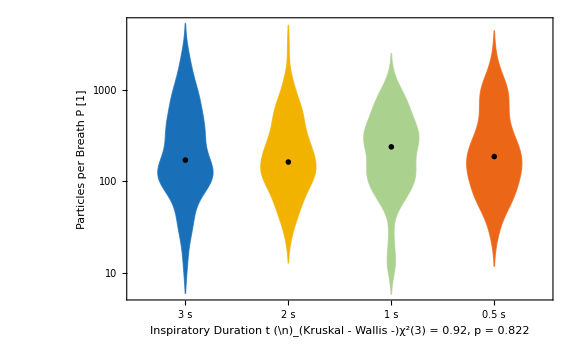
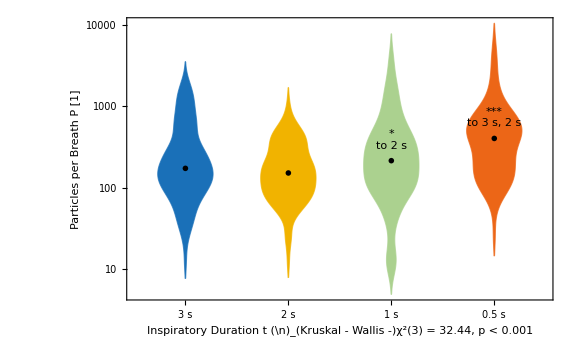
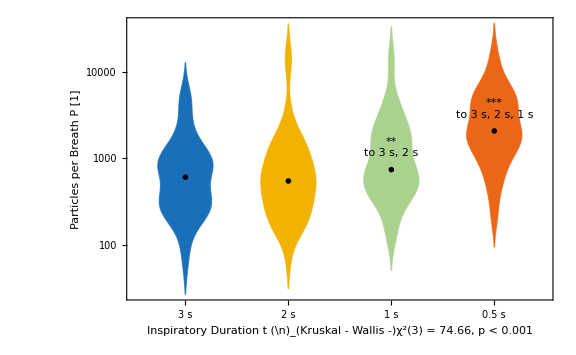
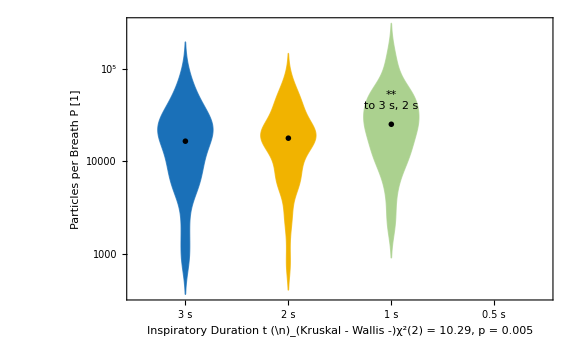
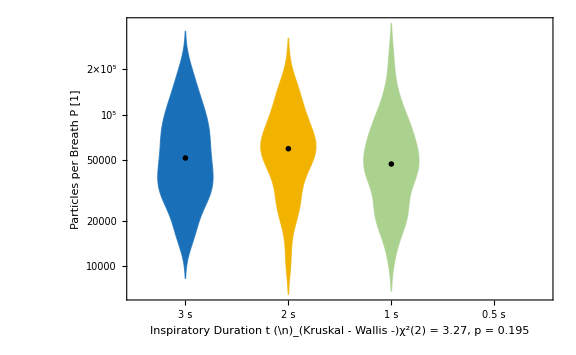
{-Graphics-
	Breathing Volume 500 ml,-Graphics-
	Breathing Volume 1000 ml,-Graphics-
	Breathing Volume 2000 ml,-Graphics-
	Breathing Volume 3000 ml,-Graphics-
	Breathing Volume Maximum}

```mathematica
plotLabels=myStyle["\n"~~If[#===max,"\tBreathing Volume Maximum","\t"~~"Breathing Volume "~~ToString[Round[#]]~~" ml"],Bold]&/@Flatten[Union[Union/@tinsp[[All,All,1]]]];

distributionChartTime=Labeled[Show[DistributionChart[#[[1]],FrameLabel->{Column[{"Inspiratory Duration t",#[[3]]},Spacings->.02],descrPartpB},ChartStyle->{3->RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],2->RGBColor[0.9450980392156862, 0.7019607843137254, 0.],1->RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],.5->RGBColor[0.9254901960784314, 0.4, 0.09019607843137255]}[[All,2]] ,myFrameStyle[],myFrameTickStyle[],ScalingFunctions->"Log",ImageSize->Large,ChartLabels->boxWhiskerLabels],ListPlot[If[Length[#]>2,Median[#],Null]&/@#[[1]],PlotStyle->Black,ScalingFunctions->"Log",PlotMarkers->Graphics[{Black,Thick,Line[{{0,0},{.4,0}}]}]],If[#[[-1]]=!=Null,Graphics[{Inset[#[[1,2]],{#[[1,1]],Log[#[[2]]*1.8]}]}]&/@Function[{marks,data},{#[[1]],Median[Flatten[#[[2]]]]}&/@Transpose[{marks,Map[{data[[#]]}&,marks[[All,1]]]}]][#[[4]],#[[1]]],{Nothing}]],#[[2]],Top]&/@Transpose[{boxWhiskerData,plotLabels,kruskalWallisTestString,Join[{Null},umwStatTforPlot,{Null}]}]
```

```mathematica
distributionChartTimeGrid= Grid[{distributionChartTime[[1;;3]],Prepend[distributionChartTime[[4;;5]],Null]},Spacings->{1,2}]
```

-Graphics-
	Breathing Volume 500 ml | -Graphics-
	Breathing Volume 1000 ml | -Graphics-
	Breathing Volume 2000 ml
 | -Graphics-
	Breathing Volume 3000 ml | -Graphics-
	Breathing Volume Maximum

```mathematica
myExportF[{{distributionChartTimeGrid,"019","violin distribution chart for particles versus inspiratory duration, subgroup breathing volume",400, False}}]
```

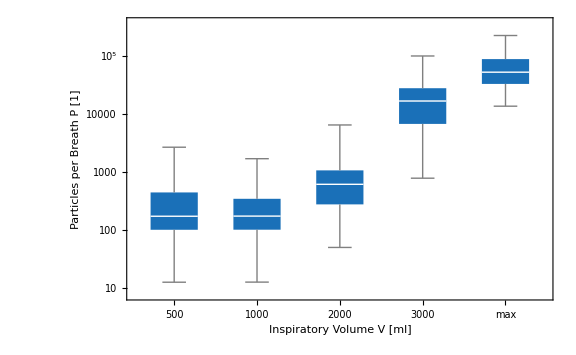
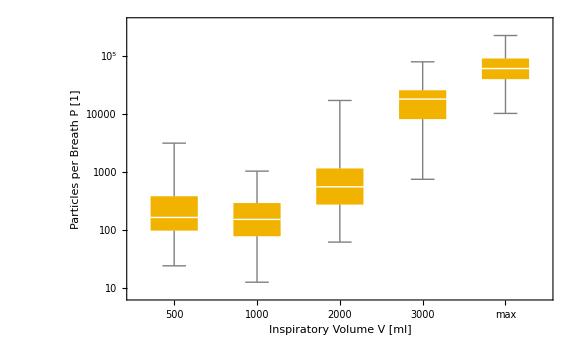
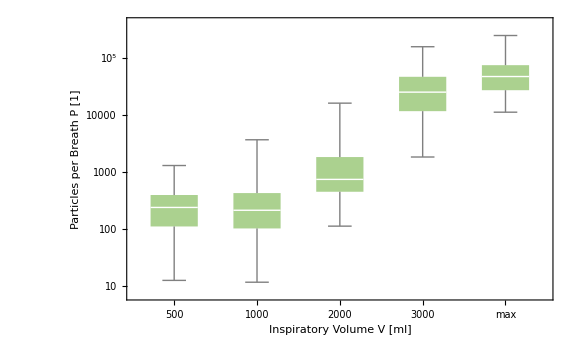
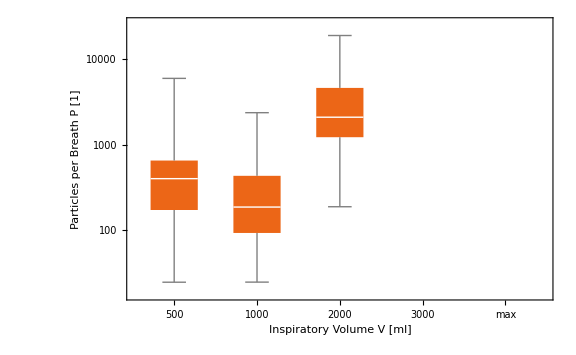
{-Graphics-
	Inspiratory Duration 3 s,-Graphics-
	Inspiratory Duration 2 s,-Graphics-
	Inspiratory Duration 1 s,-Graphics-
	Inspiratory Duration 0.5 s}

```mathematica
timeVolumekatSort=GatherBy[Flatten[dincl[[All,1]][[All,2]][[All,All,{1,6,-1}]],1],#[[2]]&];
timeVolumekatSort=GatherBy[#,#[[1]]&]&/@timeVolumekatSort;
plottitleTime=Flatten[Union/@Flatten/@timeVolumekatSort[[All,All,All,2]]];
timeVolumekatSort=#[[All,All,-1,1]]&/@timeVolumekatSort;
timeVolumekatSort[[-1]]= Join[timeVolumekatSort[[-1]],{Null},{Null}];
BoxWCharttimeVolumekat=Table[Labeled[BoxWhiskerChart[timeVolumekatSort[[i]],ScalingFunctions->"Log",ChartStyle->myPlotColors[[i,2]],ChartLabels->{500,1000,2000,3000,max},FrameLabel->{descrInspV,descrPartpB},ImageSize->Large,myFrameStyle[],myFrameTickStyle[],ImageSize->Large],myStyle["\n\tInspiratory Duration "~~ToString[plottitleTime[[i]]]~~" s",Bold],Top],{i,4}]
```

```mathematica
BoxWCharttimeVolumekatGrid=Grid[{BoxWCharttimeVolumekat[[1;;2]],BoxWCharttimeVolumekat[[3;;4]]},Spacings->{2,2}]
myExportF[{{BoxWCharttimeVolumekatGrid,"020","box-and-whisker chart for particles versus categorial volume with subgroup inspiratory duration",400,False}}]
```

-Graphics-
	Inspiratory Duration 3 s | -Graphics-
	Inspiratory Duration 2 s
-Graphics-
	Inspiratory Duration 1 s | -Graphics-
	Inspiratory Duration 0.5 s

### sex difference

```mathematica
dincl[[All,2,2,6,2]]
```

{1998,1969,1999,1952,1954,1978,1977,1992,1983,1968,1972,1986,1993,1988,1991,1952,1992,1988,1970,1990,1974,1967,1989,1972,1992,1993,1970,2004,1968,1969}

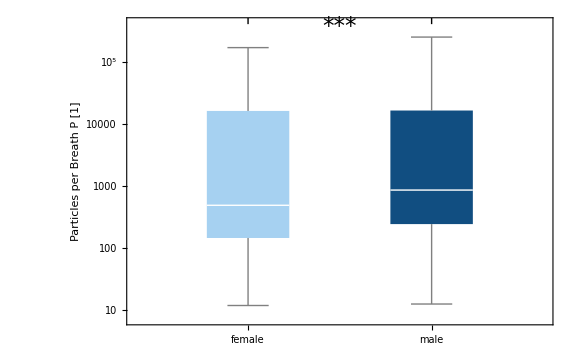

```mathematica
ageSexDataTotalParticleCount=Transpose[{dincl[[All,1,2]][[All,All,-1,1]],dincl[[All,2,2,5,2]],2023-ToExpression/@dincl[[All,2,2,6,2]],dincl[[All,3]][[All,2,{18,21}]]}]; (*total particle emission, sex, age, TLC, vital capacity*)

particlesSexPlot=BoxWhiskerChart[sexParticlesGrouped=Reverse[Flatten[#[[All,1]]]&/@GroupBy[ageSexDataTotalParticleCount,#[[2]]&]],ChartLabels->{"female","male"},FrameLabel->{None,"Particles per Breath StyleBox[\"P\",FontSlant->\"Italic\"] [1]"},ChartStyle->Reverse[myBAUAColors[4][[{-4,-2}]]],myPlotSequence[],ScalingFunctions->"Log"
,Prolog->{Line[{{1,12.9},{1,13.2},{2,13.2},{2,12.9}}],Text[myStyle["***"],{1.5,12.8}]}]
```

```mathematica
KSMTest=.
KSMTest[l_List]:=Module[{μ,σ},KolmogorovSmirnovTest[Union[l],NormalDistribution[μ,σ],"TestDataTable"]]
```

```mathematica
KSMTest/@sexParticlesGrouped
```

<|female→ | Statistic | P-Value
Kolmogorov-Smirnov | 0.330216 | 0.,male→ | Statistic | P-Value
Kolmogorov-Smirnov | 0.314459 | 0.|>

```mathematica
KolmogorovSmirnovTest[Log/@Union[#]/. Indeterminate->Nothing,NormalDistribution[μ,σ],"TestDataTable"]&/@sexParticlesGrouped
```

<|female→ | Statistic | P-Value
Kolmogorov-Smirnov | 0.134405 | 0.,male→ | Statistic | P-Value
Kolmogorov-Smirnov | 0.116018 | 0.|>

neither with log nor with raw values, there is no normal distribution

```mathematica
MWTest=.
MWTest[d1_List,d2_List]:=Module[{},Print[MannWhitneyTest[{d1,d2},0,{"TestData"},SignificanceLevel->alocal]]
;{Median[#],Length[#]}&/@{d1,d2}]
```

```mathematica
MWTest[sexParticlesGrouped[[1]],sexParticlesGrouped[[2]]]
```

{{277153.,0.0000609502}}

{{476.41,661},{847.722,950}}

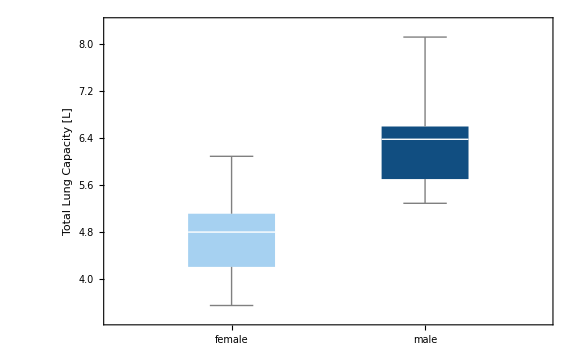
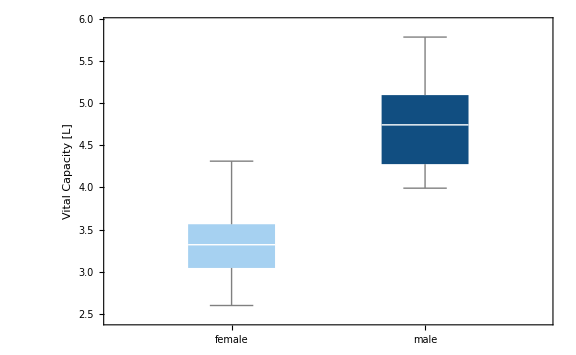

```mathematica
respBySex=GroupBy[ageSexDataTotalParticleCount,#[[2]]&][[All,All,-1]];
respSexPlot=BoxWhiskerChart[Reverse[#[[1]]],ChartLabels->{"female","male"},FrameLabel->{None,#[[2]]},ChartStyle->Reverse[myBAUAColors[4][[{-4,-2}]]],myPlotSequence[]]&/@Transpose[{Transpose/@Values@respBySex,{"Total Lung Capacity [L]", "Vital Capacity [L]"}}]
```

<|male→ | Statistic | P-Value
Kolmogorov-Smirnov | 0.179982 | 0.191188,female→ | Statistic | P-Value
Kolmogorov-Smirnov | 0.126073 | 0.846004|>

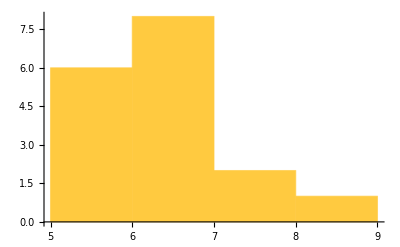
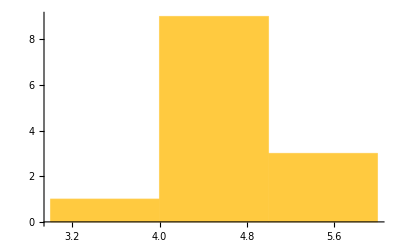
<|male→-Graphics-,female→-Graphics-|>

0.450079

{ | Statistic | P-Value
T | 6.22697 | 9.95849×10^-7,28}

```mathematica
KSMTest/@respBySex[[All,All,1]]
Histogram/@respBySex[[All,All,1]]
LeveneTest[respBySex[[All,All,1]]//Values]
TTest[respBySex[[All,All,1]]//Values,0,{"TestDataTable","DegreesOfFreedom"}]
```

<|male→ | Statistic | P-Value
Kolmogorov-Smirnov | 0.0963832 | 0.951832,female→ | Statistic | P-Value
Kolmogorov-Smirnov | 0.128903 | 0.898591|>

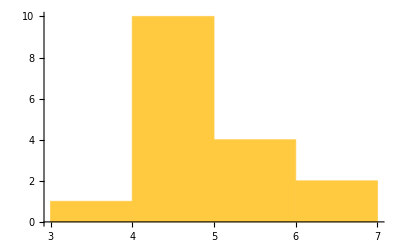
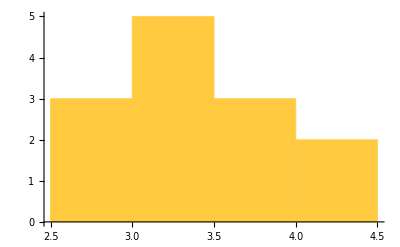
<|male→-Graphics-,female→-Graphics-|>

0.280247

{ | Statistic | P-Value
T | 6.34073 | 7.35289×10^-7,28}

```mathematica
KSMTest/@respBySex[[All,All,2]]
Histogram/@respBySex[[All,All,2]]
LeveneTest[respBySex[[All,All,2]]//Values]
TTest[respBySex[[All,All,2]]//Values,0,{"TestDataTable","DegreesOfFreedom"}]
```

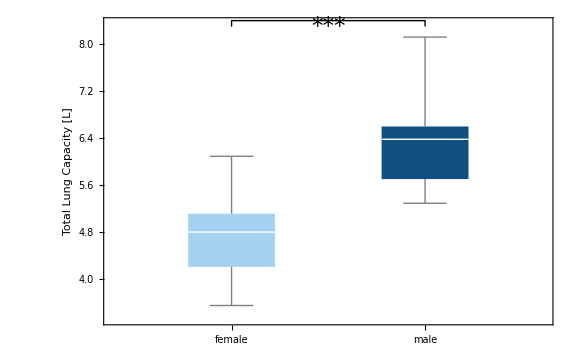

```mathematica
respSexPlot[[1]]=Append[respSexPlot[[1]],Prolog->{Line[{{1,8.3},{1,8.4},{2,8.4},{2,8.3}}],Text[myStyle["***"],{1.5,8.3}]}]
```

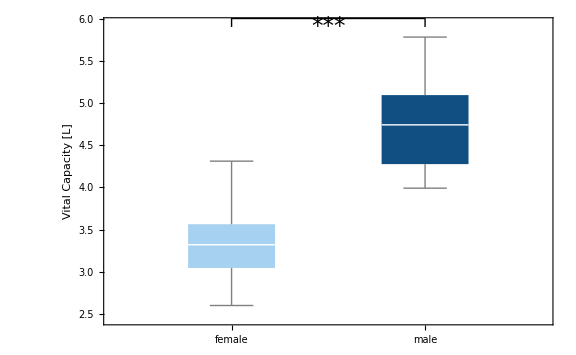

```mathematica
respSexPlot[[2]]=Append[respSexPlot[[2]],Prolog->{Line[{{1,5.9},{1,6},{2,6},{2,5.9}}],Text[myStyle["***"],{1.5,5.9}]}]
```

```mathematica
sexDifferencePlotGrid=Grid[{{Labeled[particlesSexPlot,myStyle["(A)"],{{Left,Top}}],Labeled[respSexPlot[[2]],myStyle["(B)"],{{Left,Top}}]},{SpanFromAbove,Labeled[respSexPlot[[1]],myStyle["(C)"],{{Left,Top}}]}},Alignment->{Center,Center},Spacings->{3,2}]
```

-Graphics-(A) | -Graphics-(B)
 | -Graphics-(C)

```mathematica
myExportF[{{sexDifferencePlotGrid,"067","sex difference in particle emission, TLC and VC",600,False}}]
```

### age differences

```mathematica
ageQuartiles=Flatten[{Min[#],Round/@Quartiles[#] 1.,Max[#]}]&@ageSexDataTotalParticleCount[[All,-2]]
ageQuartiles=Round/@{{#[[1]],#[[2]]-1},{#[[2]],#[[3]]-1},{#[[3]],#[[4]]-1},{#[[4]],#[[5]]}}&@ageQuartiles
```

{19,31.,42.,54.,71}

{{19,30},{31,41},{42,53},{54,71}}

```mathematica
ageData=Which[ageQuartiles[[1,1]]<=#[[-2]]<=ageQuartiles[[1,2]],ReplacePart[#,-2->1]
,ageQuartiles[[2,1]]<=#[[-2]]<=ageQuartiles[[2,2]],ReplacePart[#,-2->2]
,ageQuartiles[[3,1]]<=#[[-2]]<=ageQuartiles[[3,2]],ReplacePart[#,-2->3]
,ageQuartiles[[4,1]]<=#[[-2]]<=ageQuartiles[[4,2]],ReplacePart[#,-2->4]]&/@ageSexDataTotalParticleCount;
```

<|1→{{male,3},{female,2}},2→{{female,6},{male,4}},3→{{male,4},{female,3}},4→{{male,6},{female,2}}|>

<|1→5,2→10,3→7,4→8|>

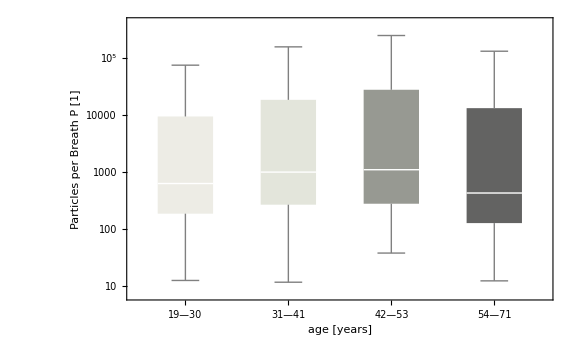

```mathematica
ageParticleData=GroupBy[ageData,#[[-2]]&][[All,All,1]];
KeySort[Tally/@GroupBy[ageData,#[[-2]]&][[All,All,-3]]]
Length/@KeySort@ageParticleData

BoxWhiskerChart[ageParticleDataFlat=myFlatten[Values@ageParticleData,1],ChartLabels->(chartlabels={ToString[#[[1]]]~~"—"~~ToString[#[[2]]]&/@ageQuartiles}),FrameLabel->{"age [years]","Particles per Breath \!\(\*
StyleBox[\"P\",\nFontSlant->\"Italic\"]\) [1]"},ChartStyle->{Darker[RGBColor[0.9568627450980393, 0.9529411764705882, 0.9254901960784314],.03],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],Darker@RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961]},myPlotSequence[],ScalingFunctions->"Log"]
```

```mathematica
KSMTest/@ageParticleDataFlat
KSMTest/@((Log/@ageParticleDataFlat)/. Indeterminate->Nothing)
```

{ | Statistic | P-Value
Kolmogorov-Smirnov | 0.330478 | 0., | Statistic | P-Value
Kolmogorov-Smirnov | 0.306832 | 0., | Statistic | P-Value
Kolmogorov-Smirnov | 0.32603 | 0., | Statistic | P-Value
Kolmogorov-Smirnov | 0.341927 | 0.}

{ | Statistic | P-Value
Kolmogorov-Smirnov | 0.138885 | 0., | Statistic | P-Value
Kolmogorov-Smirnov | 0.105585 | 0., | Statistic | P-Value
Kolmogorov-Smirnov | 0.119929 | 0., | Statistic | P-Value
Kolmogorov-Smirnov | 0.143237 | 0.}

```mathematica
MWTest@@@Subsets[ageParticleDataFlat,{2}]
```

{{52580.,0.00135047}}

{{43535.,0.0000185556}}

{{75425.,0.291534}}

{{71144.,0.12697}}

{{91105.,2.07731×10^-6}}

{{74702.,1.46745×10^-9}}

{{{628.614,295},{996.728,415}},{{628.614,295},{1097.88,366}},{{628.614,295},{427.564,535}},{{996.728,415},{1097.88,366}},{{996.728,415},{427.564,535}},{{1097.88,366},{427.564,535}}}

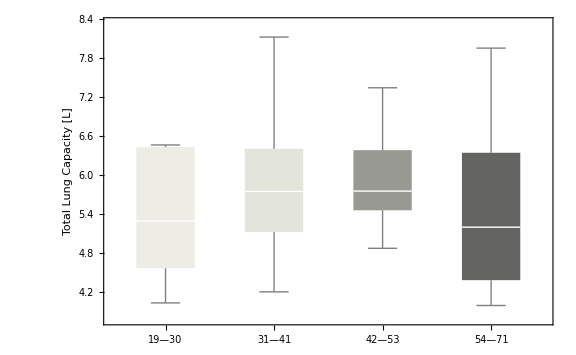
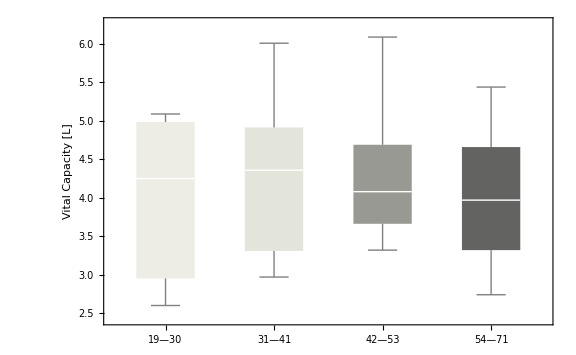

```mathematica
BoxWhiskerChart[#[[1]],FrameLabel->{None,#[[2]]},ChartLabels->chartlabels,ChartStyle->{Darker[RGBColor[0.9568627450980393, 0.9529411764705882, 0.9254901960784314],.03],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],Darker@RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961]},myPlotSequence[]]&/@Transpose[{Transpose[Transpose/@GroupBy[ageData,#[[-2]]&][[All,All,-1]]//Values],{"Total Lung Capacity [L]", "Vital Capacity [L]"}}]
```

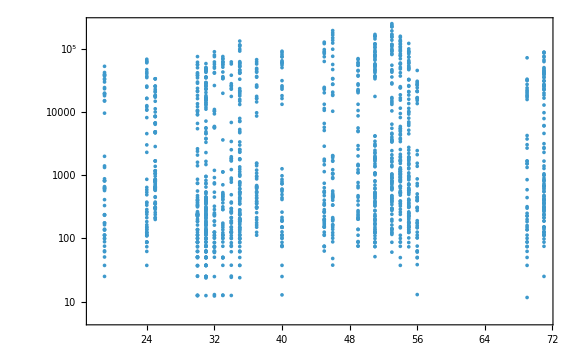

-Graphics-

```mathematica
plotAgeParticles=.
plotAgeParticles[l_List]:=Module[{age,values},age=l[[1]]; values=l[[2]];{age,#}&/@values]
ListPlot[Flatten[plotAgeParticles/@ageSexDataTotalParticleCount[[All,{-2,1}]],1],ScalingFunctions->"Log",myPlotSequence[]]
```

```mathematica
KeySort[<|1->5,4->8,3->7,2->10|>]
```

<|1→5,2→10,3→7,4→8|>

<|1→{{male,3},{female,2}},2→{{female,6},{male,4}},3→{{male,4},{female,3}},4→{{male,6},{female,2}}|>

the age distribution is not uniform and a meaningful analysis with quartiles is not possible.

```mathematica
ageTercile=Flatten[{Min[#],Round/@Quantile[#,{.33,.66,1}] 1.,Max[#]}]&@ageSexDataTotalParticleCount[[All,-2]]
ageTercile=Round/@{{#[[1]],#[[2]]-1},{#[[2]],#[[3]]-1},{#[[3]],#[[4]]-1}}&@ageTercile
```

{19,33.,51.,71.,71}

{{19,32},{33,50},{51,70}}

```mathematica
ageDataTercile=Which[ageTercile[[1,1]]<=#[[-2]]<=ageTercile[[1,2]],ReplacePart[#,-2->1]
,ageTercile[[2,1]]<=#[[-2]]<=ageTercile[[2,2]],ReplacePart[#,-2->2]
,ageTercile[[3,1]]<=#[[-2]],ReplacePart[#,-2->3]
]&/@ageSexDataTotalParticleCount
```

<|1→{{male,4},{female,5}},2→{{male,6},{female,3}},3→{{male,7},{female,5}}|>

<|1→9,2→9,3→12|>

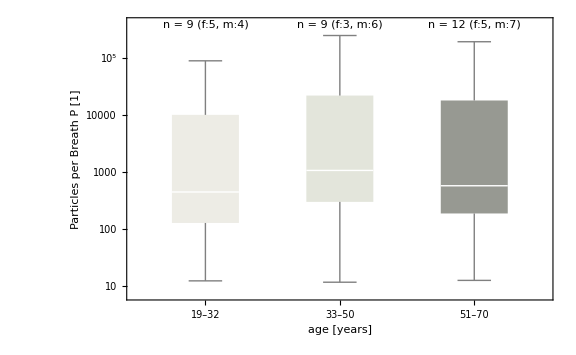

```mathematica
ageParticleDataTercile=GroupBy[ageDataTercile,#[[-2]]&][[All,All,1]];
sexN=KeySort[Tally/@GroupBy[ageDataTercile,#[[-2]]&][[All,All,-3]]]
n=KeySort[Length/@ageParticleDataTercile]
frequencies=Table[Text[myStyle["StyleBox[\"n\",FontSlant->\"Italic\"] = "~~ToString[n[[i]]]~~" (f:"~~ToString[sexN[[i,2,2]]]~~", m:"~~ToString[sexN[[i,1,2]]]~~")"]],{i,3}];
frequenciesProlog=myT[frequencies,{{1,h=12.85},{2,h},{3,h}}];

ageParticleDataTercilePlot=BoxWhiskerChart[ageParticleDataTercileFlat=myFlatten[Values@ageParticleDataTercile,1],ChartLabels->(chartlabels={ToString[#[[1]]]~~"–"~~ToString[#[[2]]]&/@ageTercile}),FrameLabel->{"age [years]","Particles per Breath \!\(\*
StyleBox[\"P\",\nFontSlant->\"Italic\"]\) [1]"},ChartStyle->{Darker[RGBColor[0.9568627450980393, 0.9529411764705882, 0.9254901960784314],.03],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],Darker@RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961]},myPlotSequence[],ScalingFunctions->"Log"
,Prolog->Text@@@frequenciesProlog/. (FontSize->__)-> (FontSize->13)]
```

```mathematica
myExportF[{{ageParticleDataTercilePlot,"068","age differences in particle emission",600,False}}]
```

```mathematica
KSMTest/@ageParticleDataTercileFlat
KSMTest/@((Log/@ageParticleDataTercileFlat)/. Indeterminate->Nothing)
```

{ | Statistic | P-Value
Kolmogorov-Smirnov | 0.332922 | 0., | Statistic | P-Value
Kolmogorov-Smirnov | 0.315183 | 0., | Statistic | P-Value
Kolmogorov-Smirnov | 0.334619 | 0.}

{ | Statistic | P-Value
Kolmogorov-Smirnov | 0.135565 | 0., | Statistic | P-Value
Kolmogorov-Smirnov | 0.112281 | 0., | Statistic | P-Value
Kolmogorov-Smirnov | 0.135672 | 0.}

```mathematica
MWTest@@@Subsets[ageParticleDataTercileFlat,{2}]
```

{{121824.,7.44072×10^-11}}

{{109611.,0.00313445}}

{{131110.,0.000371289}}

{{{445.281,508},{1066.79,619}},{{445.281,508},{574.892,484}},{{1066.79,619},{574.892,484}}}

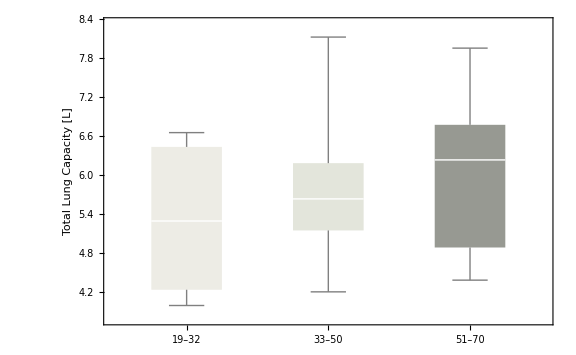
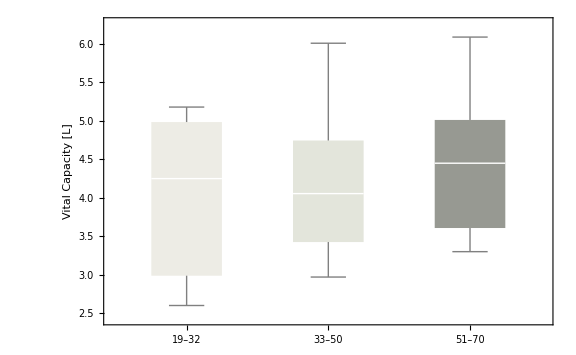

```mathematica
BoxWhiskerChart[#[[1]],FrameLabel->{None,#[[2]]},ChartLabels->chartlabels,ChartStyle->{Darker[RGBColor[0.9568627450980393, 0.9529411764705882, 0.9254901960784314],.03],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],Darker@RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961]},myPlotSequence[]]&/@Transpose[{Transpose[Transpose/@GroupBy[ageDataTercile,#[[-2]]&][[All,All,-1]]//Values],{"Total Lung Capacity [L]", "Vital Capacity [L]"}}]
```

the groups are too heterogenous to draw a meaningful conclusion. There are 3 70-year-olds and 1 18-year olds. There are some peeks between 30-40 and 50-60. A cut-off value is arbitrary. I do not recommend statistical analysis with these small, n=10, subgroups.

## Particle Bin Size Distribution

```mathematica
(*Partikelgrößen in µm Bins des
11D H20 Aerosolspektrometer Firma Grimm

Bin 1 0,309571553
Bin 2 0,3776321
Bin 3 0,452400811
Bin 4 0,555994647
Bin 5 0,70346326
Bin 6 0,943336729
Bin 7 1,149495579
Bin 8 1,277719573
Bin 9 1,375165427
Bin 10 1,46599766
Bin 11 1,566296996
Bin 12 1,692565199
Bin 13 1,885696842
Bin 14 2,158702163
Bin 15 2,51855379
Bin 16 3,422327161
"This means the first bin is between 0,3096 and 0,3776[µm] and bin 16 contains particles larger then 3,4223[mm]." Svante Hojer*)
binRange={"0.309571553","0.3776321","0.452400811","0.555994647","0.70346326","0.943336729","1.149495579","1.277719573","1.375165427","1.46599766","1.566296996","1.692565199","1.885696842","2.158702163","2.51855379","3.422327161"};
binLegend=myStyle[#,18]&/@{"0.31-0.37 µm","0.38-0.44 µm","0.45-0.55 µm","0.56-0.69 µm","0.70-0.93 µm","0.94-1.14 µm","1.15-1.27 µm","1.28-1.37 µm","1.38-1.46 µm","1.47-1.56 µm","1.57-1.68 µm","1.69-1.88 µm","1.89-2.15 µm","2.16-2.51 µm","2.52-3.41 µm","> 3.42 µm"};

binCenter=ToExpression/@{"0.309571553","0.3776321","0.452400811","0.555994647","0.70346326","0.943336729","1.149495579","1.277719573","1.375165427","1.46599766","1.566296996","1.692565199","1.885696842","2.158702163","2.51855379","3.422327161"};
binCenter=#[[1]]+(#[[2]]-#[[1]])/2&/@Partition[binCenter,2,1];
AppendTo[binCenter,3.422327161];

PDistGeoMean=.
PDistGeoMean[count_]:=GeometricMean[Flatten[Table[ConstantArray[binCenter[[i]],If[#===Median[{}],0,Round[10#]]&[Median[count[[i]]/.Null->Nothing]]],{i,Length@binCenter}]]]

plotGeomMean[data_List]:=Module[{geomM},geomM=Table[PDistGeoMean[data[[i,j]]],{i,Length@data},{j,Union[Length/@data][[1]]}]/.GeometricMean[{}]->Nothing;

ListPlot[MapThread[Legended[#1,#2]&,{Reverse@geomM,{"ΔStyleBox[\"t\",FontSlant->\"Italic\"] = 3 s","ΔStyleBox[\"t\",FontSlant->\"Italic\"] = 2 s","ΔStyleBox[\"t\",FontSlant->\"Italic\"] = 1 s","ΔStyleBox[\"t\",FontSlant->\"Italic\"] = 0.5 s"}}],Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->Values[myPlotColors],Frame->True,PlotRange->{{0.5,5.5},Automatic},FrameTicks->{{{1,"500 ml"},{2,"1000 ml"},{3,"2000 ml"},{4,"3000 ml"},{5,"max"}},All},FrameLabel->{"Inspiratory Volume","Geometric Mean Particle Size [µm]"},myPlotStyle[],myLabelStyle[11],myFrameStyle[11]]
]

myPlotColors={3->RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],2->RGBColor[0.9450980392156862, 0.7019607843137254, 0.],1->RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],.5->RGBColor[0.9254901960784314, 0.4, 0.09019607843137255]};


chartPDistData=Map[First/@#[[12;;-2]]&,Map[GroupBy[#,First]&,GatherBy[SortBy[Flatten[dincl[[All,1,2]],1],#[[6]]&],#[[6]]&],{1}],{3}];
(*first sort and gather by insp. time 0.5,1,2,3, then group by volume and take particle bin counts*)
chartPDistData[[1]]=Append[chartPDistData[[1]],{3000->{Table[Null,16]},max->{Table[Null,16]}}];
chartPDistData=Map[Transpose,chartPDistData,{2}];

chartPDistDataChart=Reverse@Table[Labeled[BoxWhiskerChart[chartPDistData[[i]],FrameLabel->{Column[{Grid[{myStyle/@{"500","1000","2000","3000","max"}},FrameStyle->Directive[Thickness[.0015]],Spacings->{{6,{6.7},6},0.5},Frame->All,ItemSize->All],"Inspiratory Volume StyleBox[\"V\",FontSlant->\"Italic\"] [ml]"},Alignment->Center],"Particles per Breath StyleBox[\"P\",FontSlant->\"Italic\"] [1]"}  ,ChartStyle->Table[Darker[SetAlphaChannel[Reverse[myPlotColors][[i,2]],(.25+.75*j/16)],(j-1)/50],{j,16}],ScalingFunctions->"Log",PlotRange->{Automatic,{1,11}},BarSpacing->Small,ChartLegends->binLegend,myFrameStyle[],myFrameTickStyle[],ImageSize->1200],myStyle["\nInspiratory Duration ΔStyleBox[\"t\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"=\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]"~~ToString[{.5,1,2,3}[[i]]]~~" s",Bold],Top],{i,4}]

geomMeanPDistDataChart=plotGeomMean[chartPDistData]
```

{-Graphics-
Inspiratory Duration Δt = 3 s,-Graphics-
Inspiratory Duration Δt = 2 s,-Graphics-
Inspiratory Duration Δt = 1 s,-Graphics-
Inspiratory Duration Δt = 0.5 s}

-Graphics-

```mathematica
chartPDistDataRel=Map[First/@#[[12;;-1]]&,Map[GroupBy[#,First]&,GatherBy[SortBy[Flatten[dincl[[All,1,2]],1],#[[6]]&],#[[6]]&],{1}],{3}];
chartPDistDataRel=Map[If[#[[-1]]!=0,#[[1;;-2]]*100/#[[-1]],Nothing]&,chartPDistDataRel,{3}];

chartPDistDataRel[[1]]=Append[chartPDistDataRel[[1]],{3000->{Table[Null,16]},max->{Table[Null,16]}}];
chartPDistDataRel=Map[Transpose,chartPDistDataRel,{2}];

chartPDistDataRelChart=Reverse@Table[Labeled[BoxWhiskerChart[chartPDistDataRel[[i]],FrameLabel->{Column[{Grid[{myStyle/@{"500","1000","2000","3000","max"}},FrameStyle->Directive[Thickness[.0015]],Spacings->{{6,{6.7},6},0.5},Frame->All,ItemSize->All],"Inspiratory Volume StyleBox[\"V\",FontSlant->\"Italic\"] [ml]"},Alignment->Center],"Portion of Particles per Total Particle Count %"},ChartStyle->Table[Darker[SetAlphaChannel[Reverse[myPlotColors][[i,2]],(.25+.75*j/16)],(j-1)/50],{j,16}],BarSpacing->Small,ChartLegends->binLegend,myFrameStyle[],myFrameTickStyle[],ImageSize->1200],myStyle["\nInspiratory Duration  t = "~~ToString[{.5,1,2,3}[[i]]]~~" s",Bold],Top],{i,4}]

geomMeanPDistDataRelChart=plotGeomMean[chartPDistDataRel]
```

{-Graphics-
Inspiratory Duration  t = 3 s,-Graphics-
Inspiratory Duration  t = 2 s,-Graphics-
Inspiratory Duration  t = 1 s,-Graphics-
Inspiratory Duration  t = 0.5 s}

-Graphics-

### Revision

```mathematica
chartPDistDataRelChartGridRevisionLabel=Column[Row[#,"     "]&/@myT[Framed[myStyle[#,18],ImageSize->{30,30},Alignment->Center]&/@abbrBinSizes,binLegend]];
abbrBinSizes=myStyle[ToUpperCase[#],11]&/@Alphabet[][[1;;Length[binLegend]]];

chartPDistDataRel=Map[First/@#[[12;;-1]]&,Map[GroupBy[#,First]&,GatherBy[SortBy[Flatten[dincl[[All,1,2]],1],#[[6]]&],#[[6]]&],{1}],{3}];
chartPDistDataRel=Map[If[#[[-1]]!=0,#[[1;;-2]]*100/#[[-1]],Nothing]&,chartPDistDataRel,{3}];

chartPDistDataRel[[1]]=Append[chartPDistDataRel[[1]],{3000->{Table[Null,16]},max->{Table[Null,16]}}];
chartPDistDataRel=Map[Transpose,chartPDistDataRel,{2}];

fs=30;

chartPDistDataRelChartRevision=Reverse@Table[Labeled[BoxWhiskerChart[chartPDistDataRel[[i]],FrameLabel->{Column[{Grid[{myStyle[#,fs]&/@{"500","1000","2000","3000","max"}},FrameStyle->Directive[Thickness[.0015]],Spacings->{{5.4,{5.2},5.4},0.5},Frame->All,ItemSize->All],myStyle["Inspiratory Volume StyleBox[\"V\",FontSlant->\"Italic\"] [ml]",fs]}
,Alignment->Center],myStyle["Portion of Particles per Total Particle Count %",fs]}
,ChartLabels->{Placed[abbrBinSizes, Below]}
,ChartStyle->Table[Darker[SetAlphaChannel[Reverse[myPlotColors][[i,2]],(.25+.75*j/16)],(j-1)/50],{j,16}]
,BarSpacing->Small,myFrameStyle[],myFrameTickStyle[fs],ImageSize->1200]
,myStyle["\nInspiratory Duration  ΔStyleBox[\"t\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"=\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]"~~ToString[{.5,1,2,3}[[i]]]~~" s",fs,Bold],Top],{i,4}];

chartPDistDataRelChartGridRevision=Labeled[Grid[{chartPDistDataRelChartRevision[[1;;2]],chartPDistDataRelChartRevision[[3;;4]]},Spacings->{4,5}],Magnify[chartPDistDataRelChartGridRevisionLabel,1.5],Right,Spacings->7];
```

-Graphics-

```mathematica
myExportF[{{Column[chartPDistDataChart,Spacings->2.5],"021","particle size distribution absolute number per volume subset inspiratory duration",300,False},{Column[chartPDistDataRelChart,Spacings->2.5],"022","relative particle size distribution number per volume subset inspiratory duration",300,False},{geomMeanPDistDataChart,"049","geometric mean for particle size distribution",600,False},{geomMeanPDistDataRelChart,"050","geometric mean for relative particle size distribution",600,False}}]
```

```mathematica
myExportF[{{chartPDistDataRelChartGridRevision,"062","relative particle size distribution number per volume subset inspiratory duration",300,False}}]
```

```mathematica
chartPDistDataDur=Map[First/@#[[12;;-2]]&,Map[GroupBy[#,#[[6]]&]&,GatherBy[SortBy[Flatten[dincl[[All,1,2]],1],#[[1]]&],#[[1]]&],{1}],{3}];(*first sort and gather by volume, then group by time and take particle bin counts*)
chartPDistDataDur[[4]]=Append[chartPDistDataDur[[4]],{0.5->{Table[Null,16]}}];
chartPDistDataDur[[5]]=Append[chartPDistDataDur[[5]],{0.5->{Table[Null,16]}}];
chartPDistDataDur=(Reverse@{0.5,1,2,3})/.#&/@chartPDistDataDur (*same order*);
chartPDistDataDur=Map[Transpose,chartPDistDataDur,{2}];

chartPDistDataDurChart=Table[Labeled[BoxWhiskerChart[Flatten[Append[#,{Null}]&/@chartPDistDataDur[[i]],1],FrameLabel->{Column[{Grid[{myStyle/@{"3 s","2 s","1 s","0.5 s"}},FrameStyle->Directive[Thickness[.0015]],Spacings->{{9.5,{9},9.5},0.5},Frame->All,ItemSize->All],"Inspiratory Duration t"},Alignment->Center],"Particles per Breath StyleBox[\"P\",FontSlant->\"Italic\"] [1]"},ChartStyle->Flatten[Append[#,White]&/@(Table[Darker[SetAlphaChannel[myPlotColors[[#,2]],(.25+.75*j/16)],(j-1)/50],{j,16}]&/@{1,2,3,4})],ScalingFunctions->"Log",PlotRange->{Automatic,{1,11}},BarSpacing->Small,ChartLegends->binLegend,myFrameStyle[],myFrameTickStyle[],ImageSize->1200],Append[myStyle["Inspiratory Volume V = "~~ToString[#]~~" ml",Bold]&/@{500,1000,2000,3000},myStyle["Maximal Breathing Volume",Bold]][[i]],Top],{i,5}]
```

{-Graphics-Inspiratory Volume V = 500 ml,-Graphics-Inspiratory Volume V = 1000 ml,-Graphics-Inspiratory Volume V = 2000 ml,-Graphics-Inspiratory Volume V = 3000 ml,-Graphics-Maximal Breathing Volume}

```mathematica
plotGeomMeanInspDur=.
plotGeomMeanInspDur[data_List]:=Module[{geomM},geomM=Table[PDistGeoMean[data[[i,j]]],{i,Length@data},{j,Union[Length/@data][[1]]}]/.GeometricMean[{}]->Nothing;

ListPlot[MapThread[Legended[#1,#2]&,{geomM,{"500 ml", "1000 ml", "2000 ml", "3000 ml", "maximal"}}],Joined->True,PlotMarkers->"OpenMarkers",PlotTheme->"Monochrome",Frame->True,PlotRange->{{0.5,4.5},Automatic},FrameTicks->{{{4,"0.5"},{3,"1"},{2,"2"},{1,"3"}},All},FrameLabel->{"Inspiratory Duration [s]","Geometric Mean Particle Size [µm]"},myPlotStyle[],myLabelStyle[11],myFrameStyle[11]]
]

geomMeanPDistDataDurChart=plotGeomMeanInspDur[chartPDistDataDur]
```

-Graphics-

```mathematica
chartPDistDataDurRel=Map[First/@#[[12;;-1]]&,Map[GroupBy[#,#[[6]]&]&,GatherBy[SortBy[Flatten[dincl[[All,1,2]],1],#[[1]]&],#[[1]]&],{1}],{3}];(*first sort and gather by volume, then group by time and take particle bin counts*)

chartPDistDataDurRel=Map[If[#[[-1]]!=0,#[[1;;-2]]*100/#[[-1]],Nothing]&,chartPDistDataDurRel,{3}];
chartPDistDataDurRel[[4]]=Append[chartPDistDataDurRel[[4]],{0.5->{Table[Null,16]}}];
chartPDistDataDurRel[[5]]=Append[chartPDistDataDurRel[[5]],{0.5->{Table[Null,16]}}];

chartPDistDataDurRel=(Reverse@{0.5,1,2,3})/.#&/@chartPDistDataDurRel (*same order*);
chartPDistDataDurRel=Map[Transpose,chartPDistDataDurRel,{2}];

chartPDistDataDurRelChart=Table[Labeled[BoxWhiskerChart[Flatten[Append[#,{Null}]&/@chartPDistDataDurRel[[i]],1],FrameLabel->{Column[{Grid[{myStyle/@{"3 s","2 s","1 s","0.5 s"}},FrameStyle->Directive[Thickness[.0015]],Spacings->{{9.5,{9},9.5},0.5},Frame->All,ItemSize->All],"Inspiratory Duration t"},Alignment->Center],"Portion of Particles per Total Particle Count %"},ChartStyle->Flatten[Append[#,White]&/@(Table[Darker[SetAlphaChannel[myPlotColors[[#,2]],(.25+.75*j/16)],(j-1)/50],{j,16}]&/@{1,2,3,4})],BarSpacing->Small,ChartLegends->binLegend,myFrameStyle[],myFrameTickStyle[],ImageSize->1200],Append[myStyle["Inspiratory Volume V = "~~ToString[#]~~" ml",Bold]&/@{500,1000,2000,3000},myStyle["Maximal Breathing Volume",Bold]][[i]],Top],{i,5}]

geomMeanPDistDataDurRelChart=plotGeomMeanInspDur[chartPDistDataDurRel]
```

{-Graphics-Inspiratory Volume V = 500 ml,-Graphics-Inspiratory Volume V = 1000 ml,-Graphics-Inspiratory Volume V = 2000 ml,-Graphics-Inspiratory Volume V = 3000 ml,-Graphics-Maximal Breathing Volume}

-Graphics-

```mathematica
myExportF[{{Column[chartPDistDataDurChart,Spacings->2.5],"023","particle size distribution absolute number per time subset inspiratory volume",250,False},{Column[chartPDistDataDurRelChart,Spacings->2.5],"024","relative particle size distribution per time subset inspiratory volume",250,False},{geomMeanPDistDataDurChart,"051","geometric mean for particle size distribution per time subset inspiratory volume",600,False},{geomMeanPDistDataDurRelChart,"052","geometric mean for relative particle size distribution per time subset inspiratory volume",600,False}}]
```

### Revision

```mathematica
chartPDistDataDurRel=Map[First/@#[[12;;-1]]&,Map[GroupBy[#,#[[6]]&]&,GatherBy[SortBy[Flatten[dincl[[All,1,2]],1],#[[1]]&],#[[1]]&],{1}],{3}];(*first sort and gather by volume, then group by time and take particle bin counts*)

chartPDistDataRelChartGridRevisionLabel=Column[Row[#,"     "]&/@myT[Framed[myStyle[#,18],ImageSize->{30,30},Alignment->Center]&/@abbrBinSizes,binLegend]];
abbrBinSizes=myStyle[ToUpperCase[#],11]&/@Alphabet[][[1;;Length[binLegend]]];

chartPDistDataDurRel=Map[If[#[[-1]]!=0,#[[1;;-2]]*100/#[[-1]],Nothing]&,chartPDistDataDurRel,{3}];
chartPDistDataDurRel[[4]]=Append[chartPDistDataDurRel[[4]],{0.5->{Table[Null,16]}}];
chartPDistDataDurRel[[5]]=Append[chartPDistDataDurRel[[5]],{0.5->{Table[Null,16]}}];

chartPDistDataDurRel=(Reverse@{0.5,1,2,3})/.#&/@chartPDistDataDurRel (*same order*);
chartPDistDataDurRel=Map[Transpose,chartPDistDataDurRel,{2}];

fs=30;

chartPDistDataDurRelChartRevision=
Table[
Labeled[
BoxWhiskerChart[
Flatten[Append[#,{Null}]&/@chartPDistDataDurRel[[i]],1],FrameLabel->{Column[{Grid[{myStyle[#,fs]&/@{"3 s","2 s","1 s","0.5 s"}},FrameStyle->Directive[Thickness[.0015]],Spacings->{{8,{7.7},8},0.5},Frame->All,ItemSize->All],myStyle["Inspiratory Duration Δt",fs]},Alignment->Center],myStyle["Portion of Particles per Total Particle Count %",fs]}
,ChartLabels->Placed[Flatten[Table[Append[abbrBinSizes," "],4]], Below]
,ChartStyle->Flatten[Append[#,White]&/@(Table[Darker[SetAlphaChannel[myPlotColors[[#,2]],(.25+.75*j/16)],(j-1)/50],{j,16}]&/@{1,2,3,4})],BarSpacing->Small
,myFrameStyle[],myFrameTickStyle[],ImageSize->1200]

,Append[myStyle["Inspiratory Volume V = "~~ToString[#]~~" ml",fs,Bold]&/@{500,1000,2000,3000},myStyle["Maximal Breathing Volume",fs,Bold]][[i]],Top]

,{i,5}];

chartPDistDataRelChartGridRevision=Grid[{chartPDistDataDurRelChartRevision[[1;;2]],chartPDistDataDurRelChartRevision[[3;;4]],{chartPDistDataDurRelChartRevision[[5]],Magnify[chartPDistDataRelChartGridRevisionLabel,1.5]}},Spacings->{5,5}];
```

```mathematica
Export[exPath~~"063.svg",chartPDistDataRelChartGridRevision]
```

Downloads\063.svg

```mathematica
myExportFSVG[{{chartPDistDataRelChartGridRevision,"063"}}];
myExportFPNG[{{chartPDistDataRelChartGridRevision,"063",150}}]
```

{{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\output\063 150 dpi.png}}

```mathematica
myExportF[{{chartPDistDataRelChartGridRevision,"06.083","relative particle size distribution number per volume subset inspiratory duration",300,False}}]
```

Export::noopen: Cannot open C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\output\png 72 dpi\06b3 _ 72 dpi.png.

Export::noopen: Cannot open C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\output\png 150 dpi\06b3 _ 150 dpi.png.

$Aborted

## Validity

```mathematica
(*Messgenauigkeit*)

equD=Select[#,#[[2]]==0&]&/@dincl[[All,1]][[All,2,All,{4,10,1,6}]];
accVD=Select[#,#[[2]]==0&]&/@dincl[[All,1]][[All,2,All,{5,10,1,6}]];

equDFlat=Transpose[Flatten[equD,1]][[1]];
accVDFlat=Transpose[Flatten[accVD,1]][[1]];

accVDHisto=Histogram[accVDFlat,FrameLabel->{"Accuracy Error %"},FrameTicks->{{Automatic,None},{Range[0,42,4],None}},ImageSize->Large,Frame->True,myFrameStyle[],myFrameTickStyle[],ChartStyle->Darker@myBAUAColors[4][[4]]]
equDHisto=Histogram[equDFlat,FrameLabel->{"Equality %"},ImageSize->Large,Frame->True,myFrameStyle[],myFrameTickStyle[],ChartStyle->Darker@myBAUAColors[4][[4]]]

percentToValue={6,8,9,10,11,12,14,20,30,40};
TableForm[Join[{{"%","0.5 l","1 l","2 l","3 l"}},myFlatten[Transpose[{percentToValue,Table[t/100*{0.5,1,2,3}*1000//N,{t,percentToValue}]}],1]]]
subGroupsValidityequD={GatherBy[#,#[[-2]]&],Reverse[GatherBy[#,#[[-1]]&]]}&@Flatten[equD,1];
subGroupsValidityaccVD={GatherBy[#,#[[-2]]&],Reverse[GatherBy[#,#[[-1]]&]]}&@Flatten[accVD,1];

equDVolPlot=BoxWhiskerChart[subGroupsValidityequD[[1,All,All,1]],ChartLabels->myStyle/@Union[Flatten[subGroupsValidityequD[[1,All,All,-2]]]],FrameLabel->{"Volume [ml]","Equality %"},ChartStyle->Darker@myBAUAColors[4][[4]],ImageSize->Large,myFrameStyle[],myFrameTickStyle[]]

equDDurPlot=BoxWhiskerChart[subGroupsValidityequD[[2,All,All,1]],ChartLabels->myStyle/@(ToString@#~~" s"&/@Union[Flatten[subGroupsValidityequD[[2,All,All,-1]]]]),FrameLabel->{"Inspiratory Duration Δt","Equality %"},ChartStyle->Darker@myBAUAColors[4][[4]],ImageSize->Large,myFrameStyle[],myFrameTickStyle[]]


accVDVolPlot=BoxWhiskerChart[subGroupsValidityaccVD[[1,All,All,1]],ChartLabels->myStyle/@Union[Flatten[subGroupsValidityaccVD[[1,All,All,-2]]]],FrameLabel->{"Volume [ml]","Accuracy Error %"},ChartStyle->Darker@myBAUAColors[4][[4]],ImageSize->Large,myFrameStyle[],myFrameTickStyle[]]

accVDDurPlot=BoxWhiskerChart[subGroupsValidityaccVD[[2,All,All,1]],ChartLabels->myStyle/@(ToString@#~~" s"&/@Union[Flatten[subGroupsValidityequD[[2,All,All,-1]]]]),FrameLabel->{"Inspiratory Duration","Accuracy Error %"},ChartStyle->Darker@myBAUAColors[4][[4]],ImageSize->Large,myFrameStyle[],myFrameTickStyle[]]
```

-Graphics-

-Graphics-

% | 0.5 l | 1 l | 2 l | 3 l
6 | 30. | 60. | 120. | 180.
8 | 40. | 80. | 160. | 240.
9 | 45. | 90. | 180. | 270.
10 | 50. | 100. | 200. | 300.
11 | 55. | 110. | 220. | 330.
12 | 60. | 120. | 240. | 360.
14 | 70. | 140. | 280. | 420.
20 | 100. | 200. | 400. | 600.
30 | 150. | 300. | 600. | 900.
40 | 200. | 400. | 800. | 1200.

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
myExportF[{{equDHisto,"025","equality histogram",600,False},{accVDHisto,"026","accuracy variance histogram",600,False},{equDVolPlot,"027","equality boxplot per volume",600,False},{equDDurPlot,"028","equality boxplot per inspiratory time",600,False},{accVDVolPlot,"029","accuracy variance boxplot per volume",600,False},{accVDDurPlot, "030","accuracy variance boxplot per inspiratory time",600,False}}]
```

## Respiratory Data

```mathematica
respdataPerPre=Select[Transpose[drespimport],StringContainsQ[#[[1]],"Percent Predicted"]&];
Clear[µ,σ];
respdataHistograms={Labeled[Histogram[Rest[#],ChartStyle->myBAUAColors[4][[2]],FrameLabel->{"%",None},ImageSize->Large,Frame->True,myFrameStyle[],myFrameTickStyle[]],myStyle[StringReplace[#[[1]],{"RVTLC"->"RV/TLC","Alveolar Volume"->"AV","IC"->"VC","Percent Predicted"->"percent predicted"}]],Top],StringReplace[#[[1]],{"Percent Predicted"->"percent predicted","Alveolar Volume"->"alveolar volume","RVTLC"->"RV/TLC","IC"->"VC"}],KolmogorovSmirnovTest[Rest[#],NormalDistribution[μ,σ],"TestDataTable"],If[KolmogorovSmirnovTest[Rest[#]]<0.05,{"median (range)", ToString@ Round@Median[Rest@#]~~" ("~~ToString@#[[1]]~~", "~~ToString@#[[2]]~~")"&@Round@MinMax[Rest@#]},{"mean (standard deviation)",ToString@Round@Mean[Rest@#]~~" ("~~ToString@Round@StandardDeviation[Rest@#]~~")"} ]}&/@respdataPerPre;
respdataHistograms=myFlatten[Transpose@{respdataHistograms,{#}&/@(IntegerString[#,10,3]&/@Range[35,35+Length[Rest@respdataPerPre]])},1]
```

{{-Graphics-FEV1 percent predicted,FEV1 percent predicted, | Statistic | P-Value
Kolmogorov-Smirnov | 0.128325 | 0.215874,mean (standard deviation),94 (11),035},{-Graphics-FVC percent predicted,FVC percent predicted, | Statistic | P-Value
Kolmogorov-Smirnov | 0.159521 | 0.0442628,median (range),125 (80, 125),036},{-Graphics-FEV1/FVC percent predicted,FEV1/FVC percent predicted, | Statistic | P-Value
Kolmogorov-Smirnov | 0.10009 | 0.595881,mean (standard deviation),98 (7),037},{-Graphics-TLCO percent predicted,TLCO percent predicted, | Statistic | P-Value
Kolmogorov-Smirnov | 0.0781131 | 0.906799,mean (standard deviation),90 (14),038},{-Graphics-AV percent predicted,alveolar volume percent predicted, | Statistic | P-Value
Kolmogorov-Smirnov | 0.165675 | 0.0307908,median (range),121 (76, 121),039},{-Graphics-FRC percent predicted,FRC percent predicted, | Statistic | P-Value
Kolmogorov-Smirnov | 0.112437 | 0.404091,mean (standard deviation),106 (23),040},{-Graphics-TLC percent predicted,TLC percent predicted, | Statistic | P-Value
Kolmogorov-Smirnov | 0.188173 | 0.00716093,median (range),115 (74, 115),041},{-Graphics-RV percent predicted,RV percent predicted, | Statistic | P-Value
Kolmogorov-Smirnov | 0.239699 | 0.000109176,median (range),219 (69, 219),042},{-Graphics-RV/TLC percent predicted,RV/TLC percent predicted, | Statistic | P-Value
Kolmogorov-Smirnov | 0.229148 | 0.000293418,median (range),255 (88, 255),043},{-Graphics-ERV percent predicted,ERV percent predicted, | Statistic | P-Value
Kolmogorov-Smirnov | 0.0790323 | 0.897699,mean (standard deviation),115 (38),044},{-Graphics-VC percent predicted,VC percent predicted, | Statistic | P-Value
Kolmogorov-Smirnov | 0.0721015 | 0.9547,mean (standard deviation),126 (13),045}}

```mathematica
myExportF[{respdataHistograms[[All,1]],respdataHistograms[[All,-1]],"histogram "~~#&/@respdataHistograms[[All,2]],ConstantArray[600,Length@respdataHistograms],ConstantArray[False,Length@respdataHistograms]}ᵀ]
```

```mathematica
desciptiveRespData=Flatten@{#[[1]],{{"minimum","1. quartile","median","3. quartile","maximum","mean","standard deviation"},Flatten[Round/@{Min[#],Quartiles[#],Max[#],Mean[#],StandardDeviation[#]}&@Rest[#]]}ᵀ}&/@respdataPerPre
```

{{FEV1 Percent Predicted,minimum,71,1. quartile,86,median,93,3. quartile,99,maximum,122,mean,94,standard deviation,11},{FVC Percent Predicted,minimum,80,1. quartile,90,median,94,3. quartile,101,maximum,125,mean,96,standard deviation,11},{FEV1/FVC Percent Predicted,minimum,83,1. quartile,92,median,98,3. quartile,101,maximum,109,mean,98,standard deviation,7},{TLCO Percent Predicted,minimum,66,1. quartile,82,median,88,3. quartile,98,maximum,130,mean,90,standard deviation,14},{Alveolar Volume Percent Predicted,minimum,76,1. quartile,84,median,91,3. quartile,97,maximum,121,mean,92,standard deviation,10},{FRC Percent Predicted,minimum,66,1. quartile,89,median,104,3. quartile,118,maximum,155,mean,106,standard deviation,23},{TLC Percent Predicted,minimum,74,1. quartile,81,median,85,3. quartile,94,maximum,115,mean,88,standard deviation,10},{RV Percent Predicted,minimum,69,1. quartile,89,median,101,3. quartile,111,maximum,219,mean,109,standard deviation,34},{RVTLC Percent Predicted,minimum,88,1. quartile,106,median,116,3. quartile,132,maximum,255,mean,125,standard deviation,36},{ERV Percent Predicted,minimum,42,1. quartile,87,median,111,3. quartile,146,maximum,209,mean,115,standard deviation,38},{IC Percent Predicted,minimum,102,1. quartile,118,median,125,3. quartile,135,maximum,153,mean,126,standard deviation,13}}

## Room Conditions

```mathematica
evalfiles = Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/url-evaluation-files.m"];
```

```mathematica
roomCondData=StringSplit[Import[#[[3]]],"\n"]&/@evalfiles;
roomCondData=StringSplit[Flatten@roomCondData[[All,19;;21]],"  "]/.""->Nothing;
roomConditionPlots=Histogram[ToExpression/@#[[1]],FrameLabel->{#[[2]],"Number of Measurements"},ChartStyle->myBAUAColors[4][[4]],Frame->True,myPlotSequence[]]&/@Transpose[{myFlatten[Transpose[Partition[StringCases[roomCondData[[All,2]],DigitCharacter..],3]],1],{"Air Pressure [hPa]","Temperature [°Celsius]","Room Humidity [%]"}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
myExportF[{{roomConditionPlots[[1]],"064","histogram of air pressure for all measurements",False,300},{roomConditionPlots[[2]],"065","histogram of temperature for all measurements",False,300},{roomConditionPlots[[3]],"066","histogram of room humidity for all measurements",False,300}}]
```

## Descriptive Data

```mathematica
descript=dincl[[All,2]][[All,2,5;;8,2]]

sexdistributionPieChart=PieChart[(Tally@descript[[All,1]])[[All,2]],ChartLabels->myStyle/@Flatten@({#[[1]]~~"  n = "~~ToString@#[[2]]}&/@Tally@descript[[All,1]]),ChartStyle->{myBAUAColors[4][[3]],White}]

ages=(2023-ToExpression@#)&/@descript[[All,2]];
ageHisto=Histogram[ages,10,FrameTicks->{Automatic,{Range[20,80,10],Automatic}},FrameLabel->myStyle/@{"Age [years]"},ChartStyle->myBAUAColors[4][[3]],ImageSize->Large,Frame->True,myFrameStyle[],myFrameTickStyle[]]

weightHeightListPlot=ListPlot[ToExpression/@descript[[All,3;;4]],FrameLabel->{"Height [cm]","Weight [kg]"},PlotStyle->myBAUAColors[4][[2]],ImageSize->Large,Frame->True,myFrameStyle[],myFrameTickStyle[]]
bmi=N[#[[2]]/((#[[1]]/100)^2)&/@(ToExpression/@descript[[All,3;;4]]),3];
bmiHisto=Histogram[bmi,{2},FrameTicks->{Automatic,{Range[18,36,2],Automatic}},FrameLabel->{"Body Mass Index [kg/m^2]"},ChartStyle->myBAUAColors[4][[3]],ImageSize->Large,Frame->True,myFrameStyle[],myFrameTickStyle[]]
```

{{male,1998,177,73},{male,1969,191,70},{male,1999,182,79},{male,1952,179,91},{female,1954,163,53},{male,1978,183,72},{male,1977,187,83},{female,1992,166,56},{female,1983,168,64},{male,1968,183,86},{female,1972,182,88},{male,1986,180,110},{female,1993,162,52},{male,1988,171,62},{male,1991,175,62},{male,1952,170,75},{female,1992,170,81},{female,1988,175,80},{female,1970,156,54},{female,1990,160,58},{male,1974,169,74},{female,1967,169,58},{male,1989,182,90},{female,1972,170,67},{female,1992,165,58},{male,1993,182,70},{male,1970,177,110},{female,2004,166,50},{male,1968,182,78},{male,1969,181,70}}

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
myExportF[{{sexdistributionPieChart,"031","sex distribution pie chart",600,False},{ageHisto,"032","age histogram",600,False},{weightHeightListPlot,"033","weight to height list plot",600,False},{bmiHisto,"034","bmi histogram",600,False}}]
```

```mathematica
Tally@descript[[All,1]]
```

{{male,17},{female,13}}

```mathematica
Union[Round/@Rest[Prepend[ages,"age [years]"]]]
```

{19,24,25,30,31,32,33,34,35,37,40,45,46,49,51,53,54,55,56,69,71}

```mathematica
Clear[µ,σ];
descriptReport=Flatten@{#[[1]],Flatten[{{"minimum","1. quartile","median","3. quartile","maximum","mean","standard deviation"},Flatten@{Round/@{Min[#],Quartiles[#],Max[#],Mean[#],StandardDeviation[#]}}}ᵀ]&@Rest[#],"Kolmogorov Smirnov Test Statistics and p-value",Round[#,.001]&/@KolmogorovSmirnovTest[Union[Round/@Rest[#]],NormalDistribution[µ,σ],"TestData"]}&/@{Prepend[ages,"age [years]"],Prepend[bmi,"BMI [kg/m^2]"],Prepend[ToExpression/@descript[[All,3]],"height [cm]"],Prepend[ToExpression/@descript[[All,4]],"weight [kg]"]}
AppendTo[descriptReport,Flatten[Tally@descript[[All,1]]]]
```

{{age [years],minimum,19,1. quartile,31,median,42,3. quartile,54,maximum,71,mean,43,standard deviation,14,Kolmogorov Smirnov Test Statistics and p-value,0.129,0.483},{BMI [kg/m^2],minimum,18,1. quartile,21,median,23,3. quartile,26,maximum,35,mean,24,standard deviation,4,Kolmogorov Smirnov Test Statistics and p-value,0.14,0.769},{height [cm],minimum,156,1. quartile,168,median,175,3. quartile,182,maximum,191,mean,174,standard deviation,9,Kolmogorov Smirnov Test Statistics and p-value,0.108,0.818},{weight [kg],minimum,50,1. quartile,58,median,71,3. quartile,81,maximum,110,mean,72,standard deviation,16,Kolmogorov Smirnov Test Statistics and p-value,0.093,0.86}}

{{age [years],minimum,19,1. quartile,31,median,42,3. quartile,54,maximum,71,mean,43,standard deviation,14,Kolmogorov Smirnov Test Statistics and p-value,0.129,0.483},{BMI [kg/m^2],minimum,18,1. quartile,21,median,23,3. quartile,26,maximum,35,mean,24,standard deviation,4,Kolmogorov Smirnov Test Statistics and p-value,0.14,0.769},{height [cm],minimum,156,1. quartile,168,median,175,3. quartile,182,maximum,191,mean,174,standard deviation,9,Kolmogorov Smirnov Test Statistics and p-value,0.108,0.818},{weight [kg],minimum,50,1. quartile,58,median,71,3. quartile,81,maximum,110,mean,72,standard deviation,16,Kolmogorov Smirnov Test Statistics and p-value,0.093,0.86},{male,17,female,13}}

```mathematica
Export[exPath~~"descriptive data of participants.xlsx",{#[[1]]->#[[2;;-1]]}&@Prepend[Join[descriptReport,desciptiveRespData],"desciptive data participants"]]
```

D:\Daten\b1464\Desktop\Ausgabe\descriptive data of participants.xlsx